# Notebook for : Introduction to General Relativity and Cosmology by Plebanski and Krasinski

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
April 25, 2022

```mathematica
(* 
be careful.. k appears in the frlw metric and then you've got a vector k defined somewhere... maybe use different notation? 
*)
```

```mathematica
(* 
Rename nonzero ricci and nozero einstein to match numbered equations
*)
```

```mathematica
(* This first integral is not immediately obvious but can be done in a few lines of algebra.  See page 297 of "Introduction to General Relativity and Cosmology" by Plebanski and Krasinski" *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book and Related

```mathematica
Hyperlink["Structures in the Universe by Exact Methods Formation Evolution Interactions by Bolejko Celerier Krasinski Hellaby and Celerier","https://www.cambridge.org/us/academic/subjects/physics/cosmology-relativity-and-gravitation/structures-universe-exact-methods-formation-evolution-interactions?format=HB&isbn=9780521769143"]
```

[Structures in the Universe by Exact Methods Formation Evolution Interactions by Bolejko Celerier Krasinski Hellaby and Celerier](https://www.cambridge.org/us/academic/subjects/physics/cosmology-relativity-and-gravitation/structures-universe-exact-methods-formation-evolution-interactions?format=HB&isbn=9780521769143)

```mathematica
Hyperlink["Inhomogeneous Cosmological Models by Krasinski",
"https://www.cambridge.org/core/books/inhomogeneous-cosmological-models/5262510EFFBD4CD0E23879ED87DE9765"]
```

[Inhomogeneous Cosmological Models by Krasinski](https://www.cambridge.org/core/books/inhomogeneous-cosmological-models/5262510EFFBD4CD0E23879ED87DE9765)

```mathematica
Hyperlink["Inhomogeneous cosmological models -  exact solutions and their applications by Bolejko Celerier and Krasinski",
"https://arxiv.org/abs/1102.1449"]
```

[Inhomogeneous cosmological models -  exact solutions and their applications by Bolejko Celerier and Krasinski](https://arxiv.org/abs/1102.1449)

```mathematica
Hyperlink["An Introduction to General Relativity and Cosmology by Plebanski and Krasinski",
"https://www.cambridge.org/core/books/an-introduction-to-general-relativity-and-cosmology/1902AF0474DA8E6D4C90783E08D88683"]
```

[An Introduction to General Relativity and Cosmology by Plebanski and Krasinski](https://www.cambridge.org/core/books/an-introduction-to-general-relativity-and-cosmology/1902AF0474DA8E6D4C90783E08D88683)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 7286 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,Notation`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[SubPlus[β]] , 
PasteButton[SubPlus[f]] , 
PasteButton[SubMinus[β]] , 
PasteButton[SubMinus[f]] , 
PasteButton[Subscript[Φ,1]],
PasteButton[Subscript[Φ,2]],
PasteButton[Subscript[Φ,3]],
PasteButton[Subscript[Φ,4]],
PasteButton[Subscript[ψ,H]],
PasteButton[Subscript[ψ,X]] , 
PasteButton[Subscript[ψ,c]]
}]
```

chrbs_shm28FrontEndObject[LinkObject["chrbs_shm", 3, 1]]28Untitled-5

```mathematica
Symbolize[β_+]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[f_+]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[β_-]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[f_-]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[Subscript[Φ, 1]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[Subscript[Φ, 2]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[Subscript[Φ, 3]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[Subscript[Φ, 4]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[Subscript[ψ, H]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[Subscript[ψ, X]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Symbolize[Subscript[ψ, c]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz  ,
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[ψ]-> dψ, 
Dt[ζ]-> dζ , 
Dt[𝓇]-> d𝓇 , 
Dt[T]-> dT
} ;
dtReplace // TableForm
```

Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[ψ]→dψ
Dt[ζ]→dζ
Dt[𝓇]→d𝓇
Dt[T]→dT

```mathematica
k/:Dt[k]=0  ; 
a/:Dt[a]=0  ; 
b/:Dt[b]=0  ;  
a0/:Dt[a0]=0  ;
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 17.1: FRLW

```mathematica
Clear[eq17pt1]
eq17pt1 = 
dt^2- R[t]^2/((1+(1/4)k r^2)^2)( dr^2+ r^2( dθ^2+ Sin[θ]^2 dϕ^2))
```

dt^2-(R[t]^2 (dr^2+r^2 (dθ^2+dϕ^2 Sin[θ]^2)))/((1+(k r^2)/4)^2)

```mathematica
Clear[metric17pt1]
metric17pt1 = 
lineToMetric[eq17pt1,{dt,dr,dθ,dϕ}]  ;
metric17pt1 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | -(r^2 R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | -(r^2 R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

## Calculation of Tensors Associated With Metric 17.1: FRLW

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input17pt1] 
input17pt1[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList17pt1];
tensorList17pt1 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList17pt1[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList17pt1[[2]]  = 
ChristoffelSymbol[ tensorList17pt1[[1]] , ActWith-> Simplify] ;
tensorList17pt1[[3]] = 
RiemannTensor[ tensorList17pt1[[1]] , ActWithNested-> Simplify ];
tensorList17pt1[[4]] = 
RicciTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
tensorList17pt1[[5]] = 
RicciScalar[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
 tensorList17pt1[[6]] = 
KretschmannScalar[ tensorList17pt1[[1]] , ActWith-> Simplify] ; 
tensorList17pt1[[7]] = 
EinsteinTensor[ tensorList17pt1[[1]] , ActWith-> Simplify] ;  
tensorList17pt1[[8]] = 
WeylTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
 tensorList17pt1[[9]] = 
CottonTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 11.67 for all tensors  *) 
input17pt1[ "metric17pt1", metric17pt1, "FRLW","g^frlw",{t,r,θ,ϕ}, "Greek"] // Timing
```

{11.8229,Null}

```mathematica
tensorList17pt1
```

{(g^frlw)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList17pt1[[1]] 
TensorName[tensorList17pt1[[1]]] 
TensorValues[tensorList17pt1[[1]]] // MatrixForm // pdConv
```

(g^frlw)_αβ^

FRLW

(1 | 0 | 0 | 0
0 | -(R(t))^2/(((k r^2)/4+1)^2) | 0 | 0
0 | 0 | -(r^2 (R(t))^2)/(((k r^2)/4+1)^2) | 0
0 | 0 | 0 | -(r^2 sin^2(θ) (R(t))^2)/(((k r^2)/4+1)^2))

```mathematica
tensorList17pt1[[2]] 
TensorName[tensorList17pt1[[2]]] 
TensorValues[tensorList17pt1[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolFRLW

((0
0
0
0) | (0
(16 R(t) (∂R(t))/(∂t))/((k r^2+4)^2)
0
0) | (0
0
(16 r^2 R(t) (∂R(t))/(∂t))/((k r^2+4)^2)
0) | (0
0
0
(16 r^2 sin^2(θ) R(t) (∂R(t))/(∂t))/((k r^2+4)^2))
(0
((∂R(t))/(∂t))/(R(t))
0
0) | (((∂R(t))/(∂t))/(R(t))
-(2 k r)/(k r^2+4)
0
0) | (0
0
(r (k r^2-4))/(k r^2+4)
0) | (0
0
0
(r sin^2(θ) (k r^2-4))/(k r^2+4))
(0
0
((∂R(t))/(∂t))/(R(t))
0) | (0
0
(4-k r^2)/(k r^3+4 r)
0) | (((∂R(t))/(∂t))/(R(t))
(4-k r^2)/(k r^3+4 r)
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂R(t))/(∂t))/(R(t))) | (0
0
0
(4-k r^2)/(k r^3+4 r)) | (0
0
0
cot(θ)) | (((∂R(t))/(∂t))/(R(t))
(4-k r^2)/(k r^3+4 r)
cot(θ)
0))

```mathematica
tensorList17pt1[[3]] 
TensorName[tensorList17pt1[[3]]] 
TensorValues[tensorList17pt1[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (16 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0
-(16 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (16 r^2 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0
0 | 0 | 0 | 0
-(16 r^2 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (16 r^2 sin^2(θ) R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(16 r^2 sin^2(θ) R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0)
(0 | -(16 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0
(16 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(256 r^2 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0
0 | (256 r^2 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(256 r^2 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4)
0 | 0 | 0 | 0
0 | (256 r^2 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0 | 0)
(0 | 0 | -(16 r^2 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0
0 | 0 | 0 | 0
(16 r^2 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (256 r^2 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0
0 | -(256 r^2 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(256 r^4 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4)
0 | 0 | (256 r^4 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0)
(0 | 0 | 0 | -(16 r^2 sin^2(θ) R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(16 r^2 sin^2(θ) R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (256 r^2 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4)
0 | 0 | 0 | 0
0 | -(256 r^2 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (256 r^4 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4)
0 | 0 | -(256 r^4 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList17pt1[[4]] 
TensorName[tensorList17pt1[[4]]] 
TensorValues[tensorList17pt1[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorFRLW

(-(3 (∂^2 R(t))/(∂t^2))/(R(t)) | 0 | 0 | 0
0 | (16 (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k r^2+4)^2) | 0 | 0
0 | 0 | (16 r^2 (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k r^2+4)^2) | 0
0 | 0 | 0 | (16 r^2 sin^2(θ) (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k r^2+4)^2))

```mathematica
tensorList17pt1[[5]] 
TensorName[tensorList17pt1[[5]]] 
TensorValues[tensorList17pt1[[5]]] // MatrixForm // pdConv
```

R

RicciScalarFRLW

-(6 (k+R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/(R(t))^2

```mathematica
tensorList17pt1[[6]] 
TensorName[tensorList17pt1[[6]]] 
TensorValues[tensorList17pt1[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarFRLW

(12 (k^2+2 k ((∂R(t))/(∂t))^2+(R(t))^2 ((∂^2 R(t))/(∂t^2))^2+((∂R(t))/(∂t))^4))/(R(t))^4

```mathematica
tensorList17pt1[[7]] 
TensorName[tensorList17pt1[[7]]] 
TensorValues[tensorList17pt1[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorFRLW

((3 (k+((∂R(t))/(∂t))^2))/(R(t))^2 | 0 | 0 | 0
0 | -(16 (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k r^2+4)^2) | 0 | 0
0 | 0 | -(16 r^2 (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k r^2+4)^2) | 0
0 | 0 | 0 | -(16 r^2 sin^2(θ) (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k r^2+4)^2))

```mathematica
tensorList17pt1[[8]] 
TensorName[tensorList17pt1[[8]]] 
TensorValues[tensorList17pt1[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList17pt1[[9]] 
TensorName[tensorList17pt1[[9]]] 
TensorValues[tensorList17pt1[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorFRLW

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

## Construction of Four Velocity u , Stress Energy Tensor 𝒯 of Dust and its Covariant Divergence For Metric 17.1: FRLW

```mathematica
Clear[u]
u = ToTensor["u", tensorList17pt1[[1]], { 1,0,0,0} ]
```

u_^α

```mathematica
u[α] // TensorValues  (* as a check *)
```

{1,0,0,0}

```mathematica
u[α]u[-α]
MergeTensors[u[α]u[-α]]
TensorValues[MergeTensors[u[α]u[-α]]]
```

u_α^ u_^α

(u·u)

1

```mathematica
(* Perfect Fluid Stress Energy Tensor Equation 12.73 Page 142 *) 
(ϵ[t]+p[t])u[-α] u[-β] 
MergeTensors[(ϵ[t]+p[t])u[-α] u[-β]]

Clear[setTermOne]
setTermOne = 
TensorValues[MergeTensors[(ϵ[t]+p[t])u[-α] u[-β]]]  ;
setTermOne// MatrixForm
```

u_α^ u_β^ (p[t]+ϵ[t])

(((p[t])·(u·u))+((ϵ[t])·(u·u)))_αβ^

(p[t]+ϵ[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList17pt1[[1]]

Clear[setTermTwo]
setTermTwo= 
(-p[t])*TensorValues[tensorList17pt1[[1]]]  ;
setTermTwo// MatrixForm
```

(g^frlw)_αβ^

(-p[t] | 0 | 0 | 0
0 | (p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | (r^2 p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | (r^2 p[t] R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

```mathematica
Clear[setValues]
setValues = 
κ*( setTermOne + setTermTwo )  ;
setValues // MatrixForm
```

(κ ϵ[t] | 0 | 0 | 0
0 | (κ p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | (r^2 κ p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | (r^2 κ p[t] R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

```mathematica
Clear[𝒯]
𝒯 = ToTensor["𝒯", tensorList17pt1[[1]], setValues, {-α,-β} ]
```

𝒯_αβ^

```mathematica
(*  Just a check.... *) 
𝒯[-α,-β]
TensorValues[𝒯[-α,-β]] // MatrixForm
```

𝒯_αβ^

(κ ϵ[t] | 0 | 0 | 0
0 | (κ p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | (r^2 κ p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | (r^2 κ p[t] R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

```mathematica
CovariantD[𝒯[α,β],-α]
MergeTensors[CovariantD[𝒯[α,β],-α]]

Clear[bianchiIdentity]
bianchiIdentity = 
TensorValues[MergeTensors[CovariantD[𝒯[α,β],-α]]]  // Expand // Simplify ;
bianchiIdentity // MatrixForm // pdConv
```

𝒯_^γβ Γ_γα^α+𝒯_^αγ Γ_γα^β+(∂𝒯)_α^αβ

(((𝒯·Γ)+(𝒯·Γ))+(∂𝒯))_^β

((κ (3 p(t) (∂R(t))/(∂t)+R(t) (∂ϵ(t))/(∂t)+3 ϵ(t) (∂R(t))/(∂t)))/(R(t))
0
0
0)

```mathematica
bianchiIdentity[[1]] ==0 
bianchiIdentity[[1]][[3]] (* Numerator *)
Expand[R[t]^2* bianchiIdentity[[1]][[3]] ]
```

(κ (3 p[t] R'[t]+3 ϵ[t] R'[t]+R[t] ϵ'[t]))/R[t]==0

3 p[t] R'[t]+3 ϵ[t] R'[t]+R[t] ϵ'[t]

3 p[t] R[t]^2 R'[t]+3 R[t]^2 ϵ[t] R'[t]+R[t]^3 ϵ'[t]

```mathematica
(* Typed in directly from book *) 
Clear[eq17pt26]
eq17pt26 = 
Inactivate[D[ϵ[t] R[t]^3,t] + 3 R[t]^2 D[R[t],t] p[t],D]
```

3 p[t] R[t]^2 InactiveR[t]t+Inactive(R[t]^3 ϵ[t])t

```mathematica
(* Our bianchi identity is equivalent *) 
Expand[R[t]^2* bianchiIdentity[[1]][[3]] ] == Activate[eq17pt26]
```

True

```mathematica
Clear[eq17pt27a]
eq17pt27a = 
eq17pt26 /. p[t]-> 0
```

Inactive(R[t]^3 ϵ[t])t

```mathematica
Clear[eq17pt27b]
eq17pt27b = 
ρ[t] ==  ϵ[t]/c^2
```

ρ[t]==ϵ[t]/c^2

```mathematica
Flatten[Solve[eq17pt27b,ϵ[t]]][[1]]
```

ϵ[t]→c^2 ρ[t]

```mathematica
eq17pt27a[[1]]
eq17pt27a[[1]] /. Flatten[Solve[eq17pt27b,ϵ[t]]][[1]]
eq17pt27a[[1]] /. Flatten[Solve[eq17pt27b,ϵ[t]]][[1]] /. c-> 1
```

R[t]^3 ϵ[t]

c^2 R[t]^3 ρ[t]

R[t]^3 ρ[t]

```mathematica
Clear[eq17pt27]
eq17pt27 = 
(eq17pt27a[[1]] /. Flatten[Solve[eq17pt27b,ϵ[t]]][[1]] /. c-> 1 ) == ( 3 ℳ)/(4π )
```

R[t]^3 ρ[t]==(3 ℳ)/(4 π)

```mathematica
ρ[t] ==  ϵ[t]/c^2
```

ρ[t]==ϵ[t]/c^2

```mathematica
Clear[epsilonReplace]
epsilonReplace = 
Flatten[Solve[Eliminate[{eq17pt27,eq17pt27b },ρ[t]][[1]],ϵ[t]]][[1]]
```

ϵ[t]→(3 c^2 ℳ)/(4 π R[t]^3)

## Derivation of Field Equations for Metric 17.1 FRLW With Perfect Fluid Source 17.24 - 17.25

```mathematica
Clear[efeFRLWperfectFluid]
efeFRLWperfectFluid = 
DeleteCases[Thread[Flatten[TensorValues[tensorList17pt1[[7]][-α,-β]]] == Flatten[TensorValues[𝒯[-α,-β]] ]-Λ*Flatten[TensorValues[tensorList17pt1[[1]][-μ,-ν]]] ],True,Infinity] ;
efeFRLWperfectFluid // TableForm
```

(3 (k+R'[t]^2))/R[t]^2==-Λ+κ ϵ[t]
-(16 (k+R'[t]^2+2 R[t] R''[t]))/((4+k r^2)^2)==(Λ R[t]^2)/((1+(k r^2)/4)^2)+(κ p[t] R[t]^2)/((1+(k r^2)/4)^2)
-(16 r^2 (k+R'[t]^2+2 R[t] R''[t]))/((4+k r^2)^2)==(r^2 Λ R[t]^2)/((1+(k r^2)/4)^2)+(r^2 κ p[t] R[t]^2)/((1+(k r^2)/4)^2)
-(16 r^2 Sin[θ]^2 (k+R'[t]^2+2 R[t] R''[t]))/((4+k r^2)^2)==(r^2 Λ R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2)+(r^2 κ p[t] R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2)

```mathematica
Clear[eq17pt24]
eq17pt24 = 
efeFRLWperfectFluid[[1]] // Expand
```

(3 k)/R[t]^2+(3 R'[t]^2)/R[t]^2==-Λ+κ ϵ[t]

```mathematica
Clear[eq17pt25]
eq17pt25 = 
Expand[Simplify[Expand[Assuming[ ((1+(k r^2)/4)^2)/R[t]^2 != 0 , MultiplySides[ efeFRLWperfectFluid[[2]],((1+(k r^2)/4)^2)/R[t]^2]]] ]]
```

Λ+κ p[t]+k/R[t]^2+R'[t]^2/R[t]^2+(2 R''[t])/R[t]==0

```mathematica
( Flatten[Solve[ ( eq17pt24  /. epsilonReplace  ) , R'[t] ]][[2]] /. Rule-> Equal  )
```

R'[t]==(√(3 c^2 ℳ κ-12 k π R[t]-4 π Λ R[t]^3))/(2 √(3 π) √R[t])

```mathematica
Clear[eq17pt28]
eq17pt28 = 
ApplySides[#^2&,( Flatten[Solve[ ( eq17pt24  /. epsilonReplace  ) , R'[t] ]][[2]] /. Rule-> Equal  ) ]  /. κ-> ( (8 π G)/c^4) // Expand
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])-1/3 Λ R[t]^2

```mathematica
Clear[hubbleConstant]
hubbleConstant = 
D[R[t],t]/R[t] == H[t]/c
```

R'[t]/R[t]==H[t]/c

```mathematica
Flatten[Solve[hubbleConstant,D[R[t],t]]][[1]]
```

R'[t]→(H[t] R[t])/c

```mathematica
eq17pt27
( eq17pt28 /. Λ-> 0  )  /. Flatten[Solve[hubbleConstant,D[R[t],t]]][[1]]
```

R[t]^3 ρ[t]==(3 ℳ)/(4 π)

(H[t]^2 R[t]^2)/c^2==-k+(2 G ℳ)/(c^2 R[t])

```mathematica
Clear[eq17pt29a]
eq17pt29a = 
Flatten[Solve[Eliminate[ {eq17pt27,( ( eq17pt28 /. Λ-> 0  )  /. Flatten[Solve[hubbleConstant,D[R[t],t]]][[1]] )},ℳ][[1]],ρ[t]]][[1]] /. Rule-> Equal // Expand
```

ρ[t]==(3 H[t]^2)/(8 G π)+(3 c^2 k)/(8 G π R[t]^2)

```mathematica
Clear[eq17pt29]
eq17pt29 = 
eq17pt29a /. ( eq17pt29a[[2,2]]  ->(  eq17pt29a[[2,2]]  /. G-> ((κ c^4)/(8π)) )  )
```

ρ[t]==(3 H[t]^2)/(8 G π)+(3 k)/(c^2 κ R[t]^2)

```mathematica
Clear[eq17pt30]
eq17pt30 = 
ρ[t]==(3 H[t]^2)/(8 G π)
```

ρ[t]==(3 H[t]^2)/(8 G π)

```mathematica
Clear[eq17pt31]
eq17pt31 = 
PowerExpand[ApplySides[Sqrt,eq17pt28]]
```

R'[t]==√(-k+(2 G ℳ)/(c^2 R[t])-1/3 Λ R[t]^2)

```mathematica
Clear[mReplace]
mReplace = { 
ℳ ==(α c^2)/G , 
α == (G M)/c^2
}  /. Equal-> Rule ;
mReplace[[1]]
mReplace[[2]]
```

ℳ→(c^2 α)/G

α→(G M)/c^2

```mathematica
Clear[eq17pt32]
eq17pt32 = { 
( eq17pt31 /. Λ-> 0  )  , 
( eq17pt31 /. Λ-> 0  )  /.mReplace[[1]] 
} ;
eq17pt32  // TableForm
```

R'[t]==√(-k+(2 G ℳ)/(c^2 R[t]))
R'[t]==√(-k+(2 α)/R[t])

```mathematica
(* R needs to be R[t]... change this after parameter has been eliminated *) 
(* Should ω be ω[t] ? *) 
Clear[eq17pt33]
eq17pt33 = { 
R == -α/k (Cosh[ω]-1) , 
t -tb == α/(-k)^(3/2)( Sinh[ω] - ω ) 
} ;
eq17pt33  // TableForm
```

R==-(α (-1+Cosh[ω]))/k
t-tb==(α (-ω+Sinh[ω]))/(-k)^(3/2)

```mathematica
Expand[Flatten[Solve[Eliminate[eq17pt33,ω][[1]][[1]] ,t]] ]
Expand[Flatten[Solve[Eliminate[eq17pt33,ω][[2]][[1]],t]]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{t→tb-(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3+(√-k α ArcCosh[(-k R+α)/α])/k^2,t→tb+(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3+(√-k α ArcCosh[(-k R+α)/α])/k^2}

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{t→tb-(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3+(√-k α ArcCosh[(-k R+α)/α])/k^2,t→tb+(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3+(√-k α ArcCosh[(-k R+α)/α])/k^2}

```mathematica
(* R needs to be R[t]... change this after parameter has been eliminated *) 
Clear[eq17pt34]
eq17pt34 = 
R == (9/2(α(t-tb))^2)^(1/3)
```

R==(3^(2/3) ((t-tb)^2 α^2)^(1/3))/2^(1/3)

```mathematica
(* R needs to be R[t]... change this after parameter has been eliminated *) 
(* Should ω be ω[t] ? *) 
Clear[eq17pt35]
eq17pt35 = { 
R == α/k (1-Cos[ω]) , 
t -tb == α/(k)^(3/2)( ω -Sin[ω]  ) 
} ;
eq17pt35  // TableForm
```

R==(α (1-Cos[ω]))/k
t-tb==(α (ω-Sin[ω]))/k^(3/2)

```mathematica
Expand[Flatten[Solve[Eliminate[eq17pt35,ω][[1]][[1]],t]]]
Expand[Flatten[Solve[Eliminate[eq17pt35,ω][[2]][[1]],t]]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{t→tb-(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3-(α ArcCos[(-k R+α)/α])/k^(3/2),t→tb+(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3-(α ArcCos[(-k R+α)/α])/k^(3/2)}

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{t→tb-(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3-(α ArcCos[(-k R+α)/α])/k^(3/2),t→tb+(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3-(α ArcCos[(-k R+α)/α])/k^(3/2)}

## Chapter 17 Calculations: Regroup these later

```mathematica
Clear[eq17pt2]
eq17pt2 = 
r == (2 𝓇)/(1 + √(1-k 𝓇^2))
```

r==(2 𝓇)/(1+√(1-k 𝓇^2))

```mathematica
Clear[eq17pt2a]
eq17pt2a = 
Flatten[Solve[eq17pt2,𝓇]][[1]] /. Rule-> Equal
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

𝓇==(4 r)/(4+k r^2)

```mathematica
Dt[eq17pt2 /. Equal-> Rule  ] /. dtReplace // Expand // Simplify
```

dr→(2 d𝓇)/(1-k 𝓇^2+√(1-k 𝓇^2))

```mathematica
eq17pt1 
eq17pt1  /. (eq17pt2 /. Equal-> Rule)
eq17pt1  /. (eq17pt2 /. Equal-> Rule) /. (Dt[eq17pt2 /. Equal-> Rule  ] /. dtReplace // Expand // Simplify  )
```

dt^2-(R[t]^2 (dr^2+r^2 (dθ^2+dϕ^2 Sin[θ]^2)))/((1+(k r^2)/4)^2)

dt^2-(R[t]^2 (dr^2+(4 𝓇^2 (dθ^2+dϕ^2 Sin[θ]^2))/((1+√(1-k 𝓇^2))^2)))/((1+(k 𝓇^2)/((1+√(1-k 𝓇^2))^2))^2)

dt^2-(R[t]^2 ((4 d𝓇^2)/((1-k 𝓇^2+√(1-k 𝓇^2))^2)+(4 𝓇^2 (dθ^2+dϕ^2 Sin[θ]^2))/((1+√(1-k 𝓇^2))^2)))/((1+(k 𝓇^2)/((1+√(1-k 𝓇^2))^2))^2)

```mathematica
Clear[metric17pt3]
metric17pt3 = 
lineToMetric[ (eq17pt1  /. (eq17pt2 /. Equal-> Rule) /. (Dt[eq17pt2 /. Equal-> Rule  ] /. dtReplace // Expand // Simplify  ) ),{dt,d𝓇,dθ,dϕ}] // Expand // FullSimplify  ;
metric17pt3 // MatrixForm
```

(1 | 0 | 0 | 0
0 | R[t]^2/(-1+k 𝓇^2) | 0 | 0
0 | 0 | -𝓇^2 R[t]^2 | 0
0 | 0 | 0 | -𝓇^2 R[t]^2 Sin[θ]^2)

```mathematica
Clear[eq17pt3]
eq17pt3 = 
Collect[ ( metricToLine[metric17pt3,{dt,d𝓇,dθ,dϕ}] /. 𝓇-> r /. d𝓇-> dr  ) , R[t]^2]
```

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1+k r^2)-dϕ^2 r^2 Sin[θ]^2)

```mathematica
Clear[eq17pt4]
eq17pt4 = 
r == Sin[ψ]
```

r==Sin[ψ]

```mathematica
Dt[eq17pt4 ] /. dtReplace
```

dr==dψ Cos[ψ]

```mathematica
eq17pt3
eq17pt3 /. k-> 1 
eq17pt3 /. k-> 1  /. (eq17pt4  /. Equal-> Rule )
eq17pt3 /. k-> 1  /. (eq17pt4  /. Equal-> Rule ) /. (Dt[eq17pt4 /. Equal-> Rule  ] /. dtReplace )
```

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1+k r^2)-dϕ^2 r^2 Sin[θ]^2)

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1+r^2)-dϕ^2 r^2 Sin[θ]^2)

dt^2+R[t]^2 (-dθ^2 Sin[ψ]^2-dϕ^2 Sin[θ]^2 Sin[ψ]^2+dr^2/(-1+Sin[ψ]^2))

dt^2+R[t]^2 (-dθ^2 Sin[ψ]^2-dϕ^2 Sin[θ]^2 Sin[ψ]^2+(dψ^2 Cos[ψ]^2)/(-1+Sin[ψ]^2))

```mathematica
Clear[metric17pt5]
metric17pt5 = 
lineToMetric[(eq17pt3 /. k-> 1  /. (eq17pt4  /. Equal-> Rule ) /. (Dt[eq17pt4 /. Equal-> Rule  ] /. dtReplace )),{dt,dψ,dθ,dϕ}] // Expand // FullSimplify  ;
metric17pt5 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2 | 0 | 0
0 | 0 | -R[t]^2 Sin[ψ]^2 | 0
0 | 0 | 0 | -R[t]^2 Sin[θ]^2 Sin[ψ]^2)

```mathematica
Clear[eq17pt5]
eq17pt5 = 
Collect[ metricToLine[metric17pt5 ,{dt,dψ,dθ,dϕ}] ,{ R[t]^2, Sin[ψ]^2}]
```

dt^2+R[t]^2 (-dψ^2+(-dθ^2-dϕ^2 Sin[θ]^2) Sin[ψ]^2)

```mathematica
Clear[eq17pt6]
eq17pt6 = 
r == Sinh[ψ]
```

r==Sinh[ψ]

```mathematica
eq17pt3
eq17pt3 /. k-> -1 
eq17pt3 /. k-> -1  /. (eq17pt6  /. Equal-> Rule )
eq17pt3 /. k-> -1  /. (eq17pt6  /. Equal-> Rule ) /. (Dt[eq17pt6 /. Equal-> Rule  ] /. dtReplace )
```

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1+k r^2)-dϕ^2 r^2 Sin[θ]^2)

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1-r^2)-dϕ^2 r^2 Sin[θ]^2)

dt^2+R[t]^2 (-dθ^2 Sinh[ψ]^2-dϕ^2 Sin[θ]^2 Sinh[ψ]^2+dr^2/(-1-Sinh[ψ]^2))

dt^2+R[t]^2 (-dθ^2 Sinh[ψ]^2-dϕ^2 Sin[θ]^2 Sinh[ψ]^2+(dψ^2 Cosh[ψ]^2)/(-1-Sinh[ψ]^2))

```mathematica
Clear[metric17pt7]
metric17pt7 = 
lineToMetric[( eq17pt3 /. k-> -1  /. (eq17pt6  /. Equal-> Rule ) /. (Dt[eq17pt6 /. Equal-> Rule  ] /. dtReplace )),{dt,dψ,dθ,dϕ}] // Expand // FullSimplify  ;
metric17pt7 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2 | 0 | 0
0 | 0 | -R[t]^2 Sinh[ψ]^2 | 0
0 | 0 | 0 | -R[t]^2 Sin[θ]^2 Sinh[ψ]^2)

```mathematica
Clear[eq17pt7]
eq17pt7 = 
Collect[ metricToLine[metric17pt7,{dt,dψ,dθ,dϕ}] ,{ R[t]^2,Sinh[ψ]^2}]
```

dt^2+R[t]^2 (-dψ^2+(-dθ^2-dϕ^2 Sin[θ]^2) Sinh[ψ]^2)

```mathematica
Clear[eq17pt8]
eq17pt8 = 
( eq17pt1 /. dθ-> 0 /. dϕ-> 0  ) ==0
```

dt^2-(dr^2 R[t]^2)/((1+(k r^2)/4)^2)==0

```mathematica
Clear[eq17pt9]
eq17pt9 =
PowerExpand[Sqrt[eq17pt8[[1]][[1]] /R[t]^2]] == (-1)*PowerExpand[Sqrt[(-1)eq17pt8[[1]][[2]]/R[t]^2]]
```

dt/R[t]==-dr/(1+(k r^2)/4)

```mathematica
Clear[eq17pt55]
eq17pt55 = 
eq17pt28 /. Λ-> (-λ)
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])+1/3 λ R[t]^2

```mathematica
eq17pt55

Clear[kPositive]
kPositive = 
Flatten[Solve[( eq17pt55[[2]]  /. R[t]-> R /. G-> 1 /. ℳ-> 1 /. c-> 1  /. k-> 3  ) == 0  , λ]][[1]] /. Rule-> Equal
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])+1/3 λ R[t]^2

λ==(3 (-2+3 R))/R^3

```mathematica
eq17pt55

Clear[kZero]
kZero = 
Flatten[Solve[( eq17pt55[[2]]  /. R[t]-> R /. G-> 1 /. ℳ-> 1 /. c-> 1  /. k-> 0  ) == 0  , λ]][[1]] /. Rule-> Equal
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])+1/3 λ R[t]^2

λ==-6/R^3

```mathematica
eq17pt55

Clear[kNegative]
kNegative = 
Flatten[Solve[( eq17pt55[[2]]  /. R[t]-> R /. G-> 1 /. ℳ-> 1 /. c-> 1  /. k-> -1  ) == 0  , λ]][[1]] /. Rule-> Equal
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])+1/3 λ R[t]^2

λ==-(3 (2+R))/R^3

```mathematica
Clear[figure17pt2]
figure17pt2 =
Plot[{
Evaluate[kPositive[[2]]]  , 
Evaluate[kZero[[2]]] , 
Evaluate[kNegative[[2]]]
} , {R,0,5},PlotRange-> {-5,4},PlotLabels->{"k > 0 ","k = 0 " , "k < 0 "},PlotLabel->"Fig 17.2"]
```

-Graphics-

```mathematica
(* Not numbered in text.... Where graph crosses λ = 0 *) 
Clear[eq17pt55a]
eq17pt55a = 
Flatten[Solve[( eq17pt55[[2]] /. λ-> 0 /. R[t]-> R    ) ==0 ,R]][[1]]/. Rule-> Equal
```

R==(2 G ℳ)/(c^2 k)

```mathematica
(* This is wrong... fix this... *) 
(* Not numbered in text.... where graph attains maximum *) 
Clear[eq17pt55b]
eq17pt55b = 
Flatten[Solve[D[(  eq17pt55[[2]] /. R[t]-> R ) ,R] == 0 ,λ]][[1]] /. Rule-> Equal
```

λ==(3 G ℳ)/(c^2 R^3)

```mathematica
Clear[eq17pt74]
eq17pt74 = 
dt^2- R[t]^2( dr^2+ f[r]^2 ( dθ^2+ Sin[θ]^2 dϕ^2))
```

dt^2-R[t]^2 (dr^2+f[r]^2 (dθ^2+dϕ^2 Sin[θ]^2))

```mathematica
Clear[metric17pt74]
metric17pt74 = 
lineToMetric[eq17pt74,{dt,dr,dθ,dϕ}]  ;
metric17pt74 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2 | 0 | 0
0 | 0 | -f[r]^2 R[t]^2 | 0
0 | 0 | 0 | -f[r]^2 R[t]^2 Sin[θ]^2)

```mathematica
Clear[eq17pt76]
eq17pt76 = 
dt^2- R[t]^2(dr^2+ (1/k) Sin[√k r]^2 ( dθ^2+ Sin[θ]^2 dϕ^2))
```

dt^2-R[t]^2 (dr^2+(Sin[√k r]^2 (dθ^2+dϕ^2 Sin[θ]^2))/k)

```mathematica
Clear[metric17pt76]
metric17pt76 = 
lineToMetric[eq17pt76,{dt,dr,dθ,dϕ}] ;
metric17pt76  // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2 | 0 | 0
0 | 0 | -(R[t]^2 Sin[√k r]^2)/k | 0
0 | 0 | 0 | -(R[t]^2 Sin[√k r]^2 Sin[θ]^2)/k)

```mathematica
Clear[eq17pt77]
eq17pt77 = 
dt^2- R[t]^2( dx^2+ D[f[x],x]^2 dy^2+ f[x]^2 dz^2)
```

dt^2-R[t]^2 (dx^2+dz^2 f[x]^2+dy^2 f'[x]^2)

## Line Element and Metric 18.1: Spherically Symmetric Inhomogeneous Model

```mathematica
Clear[eq18pt1]
eq18pt1 = 
Exp[𝒞[t,r]] dt^2 - Exp[A[t,r]] dr^2 - R[t,r]^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

-dr^2 ⅇ^A[t,r]+dt^2 ⅇ^𝒞[t,r]-R[t,r]^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric18pt1]
metric18pt1 = 
lineToMetric[eq18pt1,{dt,dr,dθ,dϕ}]  ;
metric18pt1 // MatrixForm
```

(ⅇ^𝒞[t,r] | 0 | 0 | 0
0 | -ⅇ^A[t,r] | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -R[t,r]^2 Sin[θ]^2)

## Calculation of Tensors Associated With Metric 18.1: Spherically Symmetric Inhomogeneous Model

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input18pt1] 
input18pt1[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList18pt1];
tensorList18pt1 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList18pt1[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList18pt1[[2]]  = 
ChristoffelSymbol[ tensorList18pt1[[1]] , ActWith-> Simplify] ;
tensorList18pt1[[3]] = 
RiemannTensor[ tensorList18pt1[[1]] , ActWithNested-> Simplify ];
tensorList18pt1[[4]] = 
RicciTensor[ tensorList18pt1[[1]] , ActWith-> Simplify ] ;
tensorList18pt1[[5]] = 
RicciScalar[ tensorList18pt1[[1]] , ActWith-> Simplify ] ;
 tensorList18pt1[[6]] = 
KretschmannScalar[ tensorList18pt1[[1]] , ActWith-> Simplify] ; 
tensorList18pt1[[7]] = 
EinsteinTensor[ tensorList18pt1[[1]] , ActWith-> Simplify] ;  
tensorList18pt1[[8]] = 
WeylTensor[ tensorList18pt1[[1]] , ActWith-> Simplify ] ;
 tensorList18pt1[[9]] = 
CottonTensor[ tensorList18pt1[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 17.33 for all tensors *) 
input18pt1[ "metric18pt1", metric18pt1, "SphericalInhomogeneous","g^sphi",{t,r,θ,ϕ}, "Greek"] // Timing
```

{16.4239,Null}

```mathematica
tensorList18pt1
```

{(g^sphi)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList18pt1[[1]] 
TensorName[tensorList18pt1[[1]]] 
TensorValues[tensorList18pt1[[1]]] // MatrixForm // pdConv
```

(g^sphi)_αβ^

SphericalInhomogeneous

(ⅇ^(𝒞(t,r)) | 0 | 0 | 0
0 | -ⅇ^(A(t,r)) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | sin^2(θ) (-(R(t,r))^2))

```mathematica
tensorList18pt1[[2]] 
TensorName[tensorList18pt1[[2]]] 
TensorValues[tensorList18pt1[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSphericalInhomogeneous

((1/2 (∂𝒞(t,r))/(∂t)
1/2 (∂𝒞(t,r))/(∂r)
0
0) | (1/2 (∂𝒞(t,r))/(∂r)
1/2 ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t)
0
0) | (0
0
R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t)
0) | (0
0
0
sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t))
(1/2 ⅇ^(𝒞(t,r)-A(t,r)) (∂𝒞(t,r))/(∂r)
1/2 (∂A(t,r))/(∂t)
0
0) | (1/2 (∂A(t,r))/(∂t)
1/2 (∂A(t,r))/(∂r)
0
0) | (0
0
-ⅇ^(-A(t,r)) R(t,r) (∂R(t,r))/(∂r)
0) | (0
0
0
sin^2(θ) (-ⅇ^(-A(t,r))) R(t,r) (∂R(t,r))/(∂r))
(0
0
((∂R(t,r))/(∂t))/(R(t,r))
0) | (0
0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂R(t,r))/(∂t))/(R(t,r))) | (0
0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
0
cot(θ)) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
cot(θ)
0))

```mathematica
tensorList18pt1[[3]] 
TensorName[tensorList18pt1[[3]]] 
TensorValues[tensorList18pt1[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSphericalInhomogeneous

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0
1/4 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 0
0 | 0 | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
-1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/2 sin^2(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | -1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 0
1/2 sin^2(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)) | 1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0)
(0 | 1/4 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0
1/4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
0 | 0 | 1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0
1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | -1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | -1/2 sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))
0 | 0 | 0 | 0
1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 1/2 sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)) | 0 | 0)
(0 | 0 | -1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 0
0 | 0 | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
0 | 0 | -1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0
-1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (R(t,r))^2 (ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2-1)
0 | 0 | -(sin^2(θ) (R(t,r))^2 (ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2-1)) | 0)
(0 | 0 | 0 | 1/2 sin^2(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 0
-1/2 sin^2(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)) | -1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0) | (0 | 0 | 0 | 1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 1/2 sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))
0 | 0 | 0 | 0
-1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | -1/2 sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (R(t,r))^2 (ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2-1))
0 | 0 | sin^2(θ) (R(t,r))^2 (ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2-1) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList18pt1[[4]] 
TensorName[tensorList18pt1[[4]]] 
TensorValues[tensorList18pt1[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSphericalInhomogeneous

((ⅇ^(-A(t,r)) (R(t,r) (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+4 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)))/(4 R(t,r)) | (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | 0 | 0
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | (ⅇ^(-𝒞(t,r)) (-R(t,r) (-ⅇ^(A(t,r)) (2 (∂^2 A(t,r))/(∂t^2)-(∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂A(t,r))/(∂t))^2)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+4 (∂R(t,r))/(∂r))+4 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-8 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)))/(4 R(t,r)) | 0 | 0
0 | 0 | 1/2 ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 1/2 sin^2(θ) ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))

```mathematica
tensorList18pt1[[5]] 
TensorName[tensorList18pt1[[5]]] 
TensorValues[tensorList18pt1[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSphericalInhomogeneous

1/(2 (R(t,r))^2)ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-4 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)

```mathematica
tensorList18pt1[[6]] 
TensorName[tensorList18pt1[[6]]] 
TensorValues[tensorList18pt1[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarSphericalInhomogeneous

1/(4 (R(t,r))^4)ⅇ^(-2 (A(t,r)+𝒞(t,r))) (-16 (R(t,r))^2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))-4 (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))+(∂A(t,r))/(∂r) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)))+8 (R(t,r))^2 (ⅇ^(A(t,r)) (8 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)-8 ⅇ^(𝒞(t,r)) ((∂^2 R(t,r))/(∂t ∂r))^2-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+4 ⅇ^(A(t,r)) ((∂^2 R(t,r))/(∂t^2))^2+ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2 ((∂𝒞(t,r))/(∂t))^2+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2 ((∂R(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂t))^2 ((∂𝒞(t,r))/(∂r))^2)-4 ⅇ^(A(t,r)+𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂r^2)+4 ⅇ^(2 𝒞(t,r)) ((∂^2 R(t,r))/(∂r^2))^2)+(R(t,r))^4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)^2-8 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2 (4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-(R(t,r))^2 (ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2-2 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2))+16 ⅇ^(2 A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))^2+16 ⅇ^(2 𝒞(t,r)) ((∂R(t,r))/(∂r))^4)

```mathematica
tensorList18pt1[[7]] 
TensorName[tensorList18pt1[[7]]] 
TensorValues[tensorList18pt1[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSphericalInhomogeneous

((ⅇ^(-A(t,r)) (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))/(R(t,r))^2 | (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | 0 | 0
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | (-ⅇ^(A(t,r)-𝒞(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+((∂R(t,r))/(∂r))^2)/(R(t,r))^2 | 0 | 0
0 | 0 | 1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 1/4 sin^2(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2))

```mathematica
tensorList18pt1[[8]] 
TensorName[tensorList18pt1[[8]]] 
TensorValues[tensorList18pt1[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSphericalInhomogeneous

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)/(12 (R(t,r))^2) | 0 | 0
((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)/(12 (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/24 ⅇ^(-A(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 0
1/24 ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/24 sin^2(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/24 sin^2(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0 | 0)
(0 | ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)/(12 (R(t,r))^2) | 0 | 0
((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)/(12 (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/24 ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 1/24 ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/24 sin^2(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 0 | 0
0 | -1/24 sin^2(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0)
(0 | 0 | 1/24 ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 0
1/24 ⅇ^(-A(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/24 ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 1/24 ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/12 sin^2(θ) (R(t,r))^2 ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 1/12 sin^2(θ) (R(t,r))^2 ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0)
(0 | 0 | 0 | 1/24 sin^2(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/24 sin^2(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -1/24 sin^2(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 0 | 0
0 | 1/24 sin^2(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/12 sin^2(θ) (R(t,r))^2 ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | -1/12 sin^2(θ) (R(t,r))^2 ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList18pt1[[9]] 
TensorName[tensorList18pt1[[9]]] 
TensorValues[tensorList18pt1[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorSphericalInhomogeneous

((0
(ⅇ^(-A(t,r)) (4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3-4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2-((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) ((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2+2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)+4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))))/(6 (R(t,r))^3)
0
0) | ((ⅇ^(-A(t,r)) (-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3+4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2+((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) (-((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2)-2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)-4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))))/(6 (R(t,r))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
(ⅇ^(-𝒞(t,r)) ((ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)+3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(-3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2-4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)+4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)-6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)-4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2-4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)-4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)))/(6 (R(t,r))^3)
0
0) | ((ⅇ^(-𝒞(t,r)) ((-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)-3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)-3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2+4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)-4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)+6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)+4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)-2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2+4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)+4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)))/(6 (R(t,r))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(ⅇ^(-A(t,r)-𝒞(t,r)) ((-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)-3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)-3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2+4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)-4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)+6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)+4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)-2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2+4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)+4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)))/(12 R(t,r))
0) | (0
0
(ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3+4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2+((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) (-((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2)-2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)-4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))))/(12 R(t,r))
0) | ((ⅇ^(-A(t,r)-𝒞(t,r)) ((ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)+3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(-3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2-4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)+4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)-6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)-4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2-4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)-4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)))/(12 R(t,r))
(ⅇ^(-A(t,r)-𝒞(t,r)) (4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3-4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2-((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) ((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2+2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)+4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))))/(12 R(t,r))
0
0) | (0
0
0
0)
(0
0
0
(ⅇ^(-A(t,r)-𝒞(t,r)) ((-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)-3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)-3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2+4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)-4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)+6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)+4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)-2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2+4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)+4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)) sin^2(θ))/(12 R(t,r))) | (0
0
0
(ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3+4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2+((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) (-((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2)-2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)-4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))) sin^2(θ))/(12 R(t,r))) | (0
0
0
0) | ((ⅇ^(-A(t,r)-𝒞(t,r)) ((ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)+3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(-3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2-4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)+4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)-6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)-4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2-4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)-4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)) sin^2(θ))/(12 R(t,r))
(ⅇ^(-A(t,r)-𝒞(t,r)) (4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3-4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2-((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) ((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2+2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)+4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))) sin^2(θ))/(12 R(t,r))
0
0))

## Derivation of Vacuum Field Equations For Metric 18.1: Spherically Symmetric Inhomogeneous Model (Done As A Check Prior To Defining Stress Energy Tensor)

```mathematica
(* This is with both indices down... which is not used in text *) 
Clear[nonzeroRicci18pt1] 
nonzeroRicci18pt1 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList18pt1[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci18pt1 // TableForm // pdConv
```

(ⅇ^(-A(t,r)) (R(t,r) (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+4 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)))/(4 R(t,r))
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))
(ⅇ^(-𝒞(t,r)) (-R(t,r) (-ⅇ^(A(t,r)) (2 (∂^2 A(t,r))/(∂t^2)-(∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂A(t,r))/(∂t))^2)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+4 (∂R(t,r))/(∂r))+4 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-8 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)))/(4 R(t,r))
1/2 ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
1/2 sin^2(θ) ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)

```mathematica
(* This is with both indices down... which is not used in text *) 
Clear[nonzeroEinstein18pt1] 
nonzeroEinstein18pt1 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList18pt1[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein18pt1 // TableForm // pdConv
```

(ⅇ^(-A(t,r)) (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))/(R(t,r))^2
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))
(-ⅇ^(A(t,r)-𝒞(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+((∂R(t,r))/(∂r))^2)/(R(t,r))^2
1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)
1/4 sin^2(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)

```mathematica
Clear[eq18pt3a]
eq18pt3a = 
Collect[Expand[tensorList18pt1[[7]][t,-t]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}] ;
eq18pt3a  // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2

```mathematica
Clear[eq18pt4a]
eq18pt4a = 
Collect[Expand[tensorList18pt1[[7]][r,-t]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}] ;
eq18pt4a  // pdConv
```

ⅇ^(-A(t,r)) ((2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)))

```mathematica
Clear[eq18pt5a]
eq18pt5a = 
Collect[Expand[tensorList18pt1[[7]][r,-r]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}] ;
eq18pt5a  // pdConv
```

ⅇ^(-A(t,r)) (-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) ((2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2

```mathematica
Clear[eq18pt6b]
eq18pt6b = 
Collect[Expand[tensorList18pt1[[7]][θ,-θ]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}] ;
eq18pt6b  // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(2 R(t,r))+1/4 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-((∂^2 R(t,r))/(∂r^2))/(R(t,r))-1/2 (∂^2 𝒞(t,r))/(∂r^2)-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(2 R(t,r))-1/4 ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(2 R(t,r))+1/2 (∂^2 A(t,r))/(∂t^2)-1/4 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+1/4 ((∂A(t,r))/(∂t))^2+((∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(2 R(t,r)))

```mathematica
(* Not numbered in text as different *) 
Clear[eq18pt6aa]
eq18pt6aa = 
Collect[Expand[tensorList18pt1[[7]][ϕ,-ϕ]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}]  ;
eq18pt6aa// pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(2 R(t,r))+1/4 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-((∂^2 R(t,r))/(∂r^2))/(R(t,r))-1/2 (∂^2 𝒞(t,r))/(∂r^2)-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(2 R(t,r))-1/4 ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(2 R(t,r))+1/2 (∂^2 A(t,r))/(∂t^2)-1/4 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+1/4 ((∂A(t,r))/(∂t))^2+((∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(2 R(t,r)))

```mathematica
eq18pt6a   == eq18pt6aa
```

eq18pt6a==ⅇ^(-A[t,r]) ((A^(0,1)[t,r] R^(0,1)[t,r])/(2 R[t,r])+1/4 A^(0,1)[t,r] 𝒞^(0,1)[t,r]-(R^(0,1)[t,r] 𝒞^(0,1)[t,r])/(2 R[t,r])-1/4 (𝒞^(0,1)[t,r])^2-(R^(0,2)[t,r])/R[t,r]-1/2 𝒞^(0,2)[t,r])+ⅇ^(-𝒞[t,r]) (1/4 (A^(1,0)[t,r])^2+(A^(1,0)[t,r] R^(1,0)[t,r])/(2 R[t,r])-1/4 A^(1,0)[t,r] 𝒞^(1,0)[t,r]-(R^(1,0)[t,r] 𝒞^(1,0)[t,r])/(2 R[t,r])+1/2 A^(2,0)[t,r]+(R^(2,0)[t,r])/R[t,r])

## Construction of Four Velocity u and Stress Energy Tensor 𝒯 of Dust For Metric 18.1 (Equations 18.2 and 12.74) (Change this... ,ϵ,ρ and p should be functions of t and r )

```mathematica
Clear[u]
u = ToTensor["u", tensorList18pt1[[1]], { Exp[-𝒞[t,r]/2],0,0,0} ]
```

u_^α

```mathematica
u[α] // TensorValues  (* as a check *)
```

{ⅇ^(-1/2 𝒞[t,r]),0,0,0}

```mathematica
u[α]u[-α]
MergeTensors[u[α]u[-α]]
TensorValues[MergeTensors[u[α]u[-α]]]
```

u_α^ u_^α

(u·u)

1

```mathematica
(* Perfect Fluid Stress Energy Tensor Equation 12.73 Page 142 *) 
(ϵ[t,r]+p[t,r])u[-α] u[-β] 
MergeTensors[(ϵ[t,r]+p[t,r])u[-α] u[-β]]

Clear[setTermOne]
setTermOne = 
TensorValues[MergeTensors[(ϵ[t,r]+p[t,r])u[-α] u[-β]]]  ;
setTermOne// MatrixForm
```

u_α^ u_β^ (p[t,r]+ϵ[t,r])

(((p[t, r])·(u·u))+((ϵ[t, r])·(u·u)))_αβ^

(ⅇ^𝒞[t,r] p[t,r]+ⅇ^𝒞[t,r] ϵ[t,r] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList18pt1[[1]]

Clear[setTermTwo]
setTermTwo= 
(-p[t,r])*TensorValues[tensorList18pt1[[1]]]  ;
setTermTwo// MatrixForm
```

(g^sphi)_αβ^

(-ⅇ^𝒞[t,r] p[t,r] | 0 | 0 | 0
0 | ⅇ^A[t,r] p[t,r] | 0 | 0
0 | 0 | p[t,r] R[t,r]^2 | 0
0 | 0 | 0 | p[t,r] R[t,r]^2 Sin[θ]^2)

```mathematica
Clear[setValues]
setValues = 
κ*( setTermOne + setTermTwo )  ;
setValues // MatrixForm
```

(ⅇ^𝒞[t,r] κ ϵ[t,r] | 0 | 0 | 0
0 | ⅇ^A[t,r] κ p[t,r] | 0 | 0
0 | 0 | κ p[t,r] R[t,r]^2 | 0
0 | 0 | 0 | κ p[t,r] R[t,r]^2 Sin[θ]^2)

```mathematica
Clear[𝒯]
𝒯 = ToTensor["𝒯", tensorList18pt1[[1]], setValues, {-α,-β} ]
```

𝒯_αβ^

```mathematica
(*  Just a check.... *) 
𝒯[-α,-β]
TensorValues[𝒯[-α,-β]] // MatrixForm
```

𝒯_αβ^

(ⅇ^𝒞[t,r] κ ϵ[t,r] | 0 | 0 | 0
0 | ⅇ^A[t,r] κ p[t,r] | 0 | 0
0 | 0 | κ p[t,r] R[t,r]^2 | 0
0 | 0 | 0 | κ p[t,r] R[t,r]^2 Sin[θ]^2)

```mathematica
CovariantD[𝒯[α,β],-α]
MergeTensors[CovariantD[𝒯[α,β],-α]]

Clear[bianchiIdentity]
bianchiIdentity = 
TensorValues[MergeTensors[CovariantD[𝒯[α,β],-α]]]  // Expand // Simplify ;
bianchiIdentity // MatrixForm // pdConv
```

𝒯_^γβ Γ_γα^α+𝒯_^αγ Γ_γα^β+(∂𝒯)_α^αβ

(((𝒯·Γ)+(𝒯·Γ))+(∂𝒯))_^β

((κ ⅇ^(-𝒞(t,r)) (p(t,r) (R(t,r) (∂A(t,r))/(∂t)+4 (∂R(t,r))/(∂t))+R(t,r) (ϵ(t,r) (∂A(t,r))/(∂t)+2 (∂ϵ(t,r))/(∂t))+4 ϵ(t,r) (∂R(t,r))/(∂t)))/(2 R(t,r))
1/2 κ ⅇ^(-A(t,r)) ((p(t,r)+ϵ(t,r)) (∂𝒞(t,r))/(∂r)+2 (∂p(t,r))/(∂r))
0
0)

```mathematica
bianchiIdentity[[1]]  == 0  // pdConv
bianchiIdentity[[2]]  == 0  // pdConv
```

(κ ⅇ^(-𝒞(t,r)) (p(t,r) (R(t,r) (∂A(t,r))/(∂t)+4 (∂R(t,r))/(∂t))+R(t,r) (ϵ(t,r) (∂A(t,r))/(∂t)+2 (∂ϵ(t,r))/(∂t))+4 ϵ(t,r) (∂R(t,r))/(∂t)))/(2 R(t,r))==0

1/2 κ ⅇ^(-A(t,r)) ((p(t,r)+ϵ(t,r)) (∂𝒞(t,r))/(∂r)+2 (∂p(t,r))/(∂r))==0

## Derivation of Field Equations For Metric 18.1 With A Perfect Fluid Stress Energy Tensor and Cosmological Constant

```mathematica
(* Need these for the Einstein Field Equations see Equation 12.80 Page 144 *) 
tensorList18pt1[[7]][-μ,-ν]
Λ*tensorList18pt1[[1]][-μ,-ν]
𝒯[-μ,-ν]
```

G_μν^

Λ (g^sphi)_μν^

𝒯_μν^

```mathematica
Clear[efeSphericalPerfectFluid]
efeSphericalPerfectFluid = 
DeleteDuplicates[DeleteCases[Thread[Flatten[TensorValues[tensorList18pt1[[7]][-μ,-ν]]]== Flatten[( TensorValues[𝒯[-μ,-ν]]-Λ*TensorValues[tensorList18pt1[[1]][-μ,-ν]] ) ]],True,Infinity]]  ;
efeSphericalPerfectFluid// TableForm // pdConv
```

(ⅇ^(-A(t,r)) (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))/(R(t,r))^2==κ ⅇ^(𝒞(t,r)) ϵ(t,r)-Λ ⅇ^(𝒞(t,r))
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))==0
(-ⅇ^(A(t,r)-𝒞(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+((∂R(t,r))/(∂r))^2)/(R(t,r))^2==κ ⅇ^(A(t,r)) p(t,r)+Λ ⅇ^(A(t,r))
1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)==κ p(t,r) (R(t,r))^2+Λ (R(t,r))^2
1/4 sin^2(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)==κ sin^2(θ) p(t,r) (R(t,r))^2+Λ sin^2(θ) (R(t,r))^2

```mathematica
Clear[eq18pt3]
eq18pt3 = 
Collect[Expand[Assuming[ⅇ^𝒞[t,r] != 0 , DivideSides[Collect[efeSphericalPerfectFluid[[1]],ⅇ^𝒞[t,r]],ⅇ^𝒞[t,r]]] ],{ⅇ^(-𝒞[t,r]),ⅇ^(-A[t,r])}] ;
eq18pt3 // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2==κ ϵ(t,r)-Λ

```mathematica
Clear[eq18pt4]
eq18pt4 = 
MultiplySides[Expand[efeSphericalPerfectFluid[[2]]],(-1)] ;
eq18pt4 // pdConv
```

(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))==0

```mathematica
Clear[eq18pt5]
eq18pt5 = 
Collect[ Expand[Assuming[(-1)*ⅇ^A[t,r]!= 0 , DivideSides[ efeSphericalPerfectFluid[[3]] ,(-1)*ⅇ^A[t,r]]]] ,{ⅇ^(-𝒞[t,r]),ⅇ^(-A[t,r])}]  ;
eq18pt5// pdConv
```

ⅇ^(-A(t,r)) (-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) ((2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2==-κ p(t,r)-Λ

```mathematica
Clear[eq18pt6]
eq18pt6 = 
Collect[ Expand[Assuming[(-1)* R[t,r]^2 != 0 , DivideSides[efeSphericalPerfectFluid[[4]] ,(-1)* R[t,r]^2]]] , {ⅇ^(-𝒞[t,r]),ⅇ^(-A[t,r])}] // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(2 R(t,r))+1/4 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-((∂^2 R(t,r))/(∂r^2))/(R(t,r))-1/2 (∂^2 𝒞(t,r))/(∂r^2)-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(2 R(t,r))-1/4 ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(2 R(t,r))+1/2 (∂^2 A(t,r))/(∂t^2)-1/4 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+1/4 ((∂A(t,r))/(∂t))^2+((∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(2 R(t,r)))==-κ p(t,r)-Λ

## Derivation of Mass and Energy Conservation Equation 18.10: “The time derivative of mass equals volume work”

```mathematica
(* Our Derivation *) 
Clear[eq18pt7a]
eq18pt7a = 
Expand[Assuming[ ( R[t,r]^2*D[R[t,r],r] )  != 0 , MultiplySides[ eq18pt3,( R[t,r]^2*D[R[t,r],r] ) ]]]  ;
eq18pt7a // pdConv
```

-2 ⅇ^(-A(t,r)) R(t,r) (∂^2 R(t,r))/(∂r^2) (∂R(t,r))/(∂r)+R(t,r) ⅇ^(-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t) (∂R(t,r))/(∂r)-ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^3+ⅇ^(-A(t,r)) R(t,r) (∂A(t,r))/(∂r) ((∂R(t,r))/(∂r))^2+ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂R(t,r))/(∂r)+(∂R(t,r))/(∂r)==κ (R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r)-Λ (R(t,r))^2 (∂R(t,r))/(∂r)

```mathematica
(*  Typed in directly from book *) 
Clear[eq18pt7]
eq18pt7 = 
D[( R[t,r] + Exp[-𝒞[t,r]]R[t,r] D[R[t,r],t]^2-Exp[-A[t,r]]R[t,r] D[R[t,r],r]^2+1/3 Λ R[t,r]^3 ) ,r] - R[t,r] D[ ( Exp[-𝒞[t,r]] D[R[t,r],t]^2 ) ,r] +  Exp[-𝒞[t,r]]D[A[t,r],t]R[t,r]D[R[t,r],t]D[R[t,r],r] == κ ϵ[t,r] R[t,r]^2 D[R[t,r],r] ;
eq18pt7 // pdConv
```

2 R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-R(t,r) (2 ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂r))-2 ⅇ^(-A(t,r)) R(t,r) (∂^2 R(t,r))/(∂r^2) (∂R(t,r))/(∂r)+R(t,r) ⅇ^(-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t) (∂R(t,r))/(∂r)-ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^3+ⅇ^(-A(t,r)) R(t,r) (∂A(t,r))/(∂r) ((∂R(t,r))/(∂r))^2+ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂R(t,r))/(∂r)-R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂r)+Λ (R(t,r))^2 (∂R(t,r))/(∂r)+(∂R(t,r))/(∂r)==κ ϵ (R(t,r))^2 (∂R(t,r))/(∂r)

```mathematica
(* This just shows that both forms are equivalent... *) 
( eq18pt7a[[1]]-eq18pt7a[[2]] )  == ( eq18pt7[[1]]-eq18pt7[[2]] )  // Expand // FullSimplify
```

κ R[t,r] (ϵ-ϵ[t,r]) R^(0,1)[t,r]==0

```mathematica
(* "As a consequence of 18.4 the second and third terms of 18.7 on the lhs sum up to zero"*)
Clear[secondAndThird]
secondAndThird = 
(-1)*R[t,r] D[ ( Exp[-𝒞[t,r]] D[R[t,r],t]^2 ) ,r] +  Exp[-𝒞[t,r]]D[A[t,r],t]R[t,r]D[R[t,r],t]D[R[t,r],r] ;
secondAndThird  // pdConv
```

R(t,r) ⅇ^(-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂r) (∂R(t,r))/(∂t)-R(t,r) (2 ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂r))

```mathematica
(* "As a consequence of 18.4 the second and third terms of 18.7 on the lhs sum up to zero""*)
eq18pt4 // pdConv
```

(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))==0

```mathematica
(* "As a consequence of 18.4 the second and third terms of 18.7 on the lhs sum up to zero""*)
Flatten[Solve[ eq18pt4,Derivative[1,1][R][t,r]]][[1]] // pdConv
```

(∂^2 R(t,r))/(∂t ∂r)→1/2 ((∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))

```mathematica
(* "As a consequence of 18.4 the second and third terms of 18.7 on the lhs sum up to zero""*)
secondAndThird  /. Flatten[Solve[ eq18pt4,Derivative[1,1][R][t,r]]][[1]] // Expand // Simplify
```

0

```mathematica
Clear[eq18pt8]
eq18pt8 = 
Inactivate[D[( R[t,r] + Exp[-𝒞[t,r]]R[t,r] D[R[t,r],t]^2-Exp[-A[t,r]]R[t,r] D[R[t,r],r]^2+1/3 Λ R[t,r]^3 ) ,r],D] ==  κ ϵ[t,r] R[t,r]^2 D[R[t,r],r] ;
eq18pt8 // pdConv
```

(∂(-ⅇ^(-A(t,r)) R(t,r) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2+1/3 Λ (R(t,r))^3+R(t,r)))/(∂r)==κ (R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r)

```mathematica
Activate[eq18pt8 ] // pdConv
```

2 R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-2 ⅇ^(-A(t,r)) R(t,r) (∂^2 R(t,r))/(∂r^2) (∂R(t,r))/(∂r)-ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^3+ⅇ^(-A(t,r)) R(t,r) (∂A(t,r))/(∂r) ((∂R(t,r))/(∂r))^2+ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂R(t,r))/(∂r)-R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂r)+Λ (R(t,r))^2 (∂R(t,r))/(∂r)+(∂R(t,r))/(∂r)==κ (R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r)

```mathematica
eq18pt5 // pdConv
```

ⅇ^(-A(t,r)) (-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) ((2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2==-κ p(t,r)-Λ

```mathematica
(* Our Derivation... *) 
Clear[eq18pt9a]
eq18pt9a = 
Expand[Assuming[R[t,r]^2*D[R[t,r],t] != 0 , MultiplySides[ eq18pt5,R[t,r]^2*D[R[t,r],t]]]]  ;
eq18pt9a // pdConv
```

-ⅇ^(-A(t,r)) R(t,r) (∂R(t,r))/(∂r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2 (∂R(t,r))/(∂t)+2 R(t,r) ⅇ^(-𝒞(t,r)) (∂^2 R(t,r))/(∂t^2) (∂R(t,r))/(∂t)+ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^3-R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂t)+(∂R(t,r))/(∂t)==-κ p(t,r) (R(t,r))^2 (∂R(t,r))/(∂t)-Λ (R(t,r))^2 (∂R(t,r))/(∂t)

```mathematica
(* "Then 18.9 can be read as the enery conservation equation:  the time derivative of mass equals volume work" *) 
Clear[eq18pt9]
eq18pt9 = 
Inactivate[D[( R[t,r] + Exp[-𝒞[t,r]]R[t,r] D[R[t,r],t]^2- Exp[-A[t,r]] R[t,r] D[R[t,r],r]^2+1/3 Λ R[t,r]^3 ) ,t],D] == -p[t,r] κ R[t,r]^2 D[R[t,r],t] ;
eq18pt9 // pdConv
```

(∂(-ⅇ^(-A(t,r)) R(t,r) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2+1/3 Λ (R(t,r))^3+R(t,r)))/(∂t)==-κ p(t,r) (R(t,r))^2 (∂R(t,r))/(∂t)

```mathematica
(* Our attempt to show that both forms are equivalent leads to this expression ... *) 
(eq18pt9a[[1]]-eq18pt9a[[2]] ) == ( Activate[eq18pt9][[1]]-Activate[eq18pt9][[2]] )  // Expand // Simplify  // pdConv
```

ⅇ^(-A(t,r)) R(t,r) (∂R(t,r))/(∂r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))==0

```mathematica
(* But from 18.4 we have... *) 
Flatten[Solve[eq18pt4,Derivative[1,1][R][t,r]]][[1]] // pdConv
```

(∂^2 R(t,r))/(∂t ∂r)→1/2 ((∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))

```mathematica
(* And now we have that both forms are equivalent... *) 
((eq18pt9a[[1]]-eq18pt9a[[2]] ) == ( Activate[eq18pt9][[1]]-Activate[eq18pt9][[2]] )  // Expand // Simplify )  /. Flatten[Solve[eq18pt4,Derivative[1,1][R][t,r]]][[1]] // Expand
```

True

```mathematica
(*  Check to make sure that this m is the arbitrary function m[r] and not m[t,r] *) 
(* See page 41 Structures in universe... there m[t,r] *) 
Clear[eq18pt10]
eq18pt10 = 
m[t,r] == ( R[t,r] + Exp[-𝒞[t,r]]R[t,r] D[R[t,r],t]^2- Exp[-A[t,r]] R[t,r] D[R[t,r],r]^2+1/3 Λ R[t,r]^3 )  ;
eq18pt10 // pdConv
```

m(r)==-ⅇ^(-A(t,r)) R(t,r) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2+1/3 Λ (R(t,r))^3+R(t,r)

## Derivation of Evolution Equation 18.14 (With Λ = 0 18.14 is formally identical to the Newtonian equation of radial motion in a Coulumb Potential where M plays roll of mass and ℰ plays roll of energy within shell of radius r )

```mathematica
( eq18pt4[[1]] /. Derivative[0,1][𝒞][t,r]-> 0  )  // pdConv
```

(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))

```mathematica
Clear[eq18pt11a]
eq18pt11a = 
Inactivate[D[Exp[-A[t,r]/2]D[R[t,r],r],t],D]  ;
eq18pt11a // pdConv
```

(∂(ⅇ^(-1/2 A(t,r)) (∂R(t,r))/(∂r)))/(∂t)

```mathematica
(* Expand derivative *) 
Clear[eq18pt11b]
eq18pt11b = 
Collect[Activate[eq18pt11a ] ,ⅇ^(-1/2 A[t,r])]== 0  ;
eq18pt11b  // pdConv
```

ⅇ^(-1/2 A(t,r)) ((∂^2 R(t,r))/(∂t ∂r)-1/2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r))==0

```mathematica
(* Get rid of exponential *) 
Clear[eq18pt11c]
eq18pt11c = 
eq18pt11b[[1]][[2]] == 0  ;
eq18pt11c  // pdConv
```

(∂^2 R(t,r))/(∂t ∂r)-1/2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)==0

```mathematica
Collect[Activate[eq18pt11a],Exp[-1/2 A[t,r]]] // pdConv
```

ⅇ^(-1/2 A(t,r)) ((∂^2 R(t,r))/(∂t ∂r)-1/2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r))

```mathematica
Expand[(2/R[t,r])*Collect[Activate[eq18pt11a],Exp[-1/2 A[t,r]]][[2]] ] // pdConv
```

(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))

```mathematica
(* Both forms are equivalent after setting equal to zero... just get rid of exponential and constant factor... *) 
( eq18pt4[[1]] /. Derivative[0,1][𝒞][t,r]-> 0  ) == Expand[(2/R[t,r])*Collect[Activate[eq18pt11a],Exp[-1/2 A[t,r]]][[2]] ]
```

True

```mathematica
(* √(1+2ℰ[r]) is the arbitrary function of r we get from integration *) 
Activate[Integrate[eq18pt11a,t] ] == √(1+2ℰ[r]) // pdConv
```

ⅇ^(-1/2 A(t,r)) (∂R(t,r))/(∂r)==√(2 ℰ(r)+1)

```mathematica
Clear[eq18pt12a]
eq18pt12a = 
ApplySides[#^2&,Activate[Integrate[eq18pt11a,t] ] == √(1+2ℰ[r])] ;
eq18pt12a // pdConv
```

ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2==2 ℰ(r)+1

```mathematica
Clear[alphaReplace]
alphaReplace = { 
 Exp[-A[t,r]] ->1/ α , 
α->  Exp[A[t,r]]
}  ;
alphaReplace[[1]]
alphaReplace[[2]]
```

ⅇ^(-A[t,r])→1/α

α→ⅇ^A[t,r]

```mathematica
Clear[eq18pt12]
eq18pt12 = 
( Flatten[Solve[ eq18pt12a   /. alphaReplace[[1]]  , α]][[1]] /. alphaReplace[[2]] ) /. Rule-> Equal  ;
eq18pt12 // pdConv
```

ⅇ^(A(t,r))==((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1)

```mathematica
( eq18pt5  /. p[t,r]-> 0 /. 𝒞[t,r]-> 0  /. D[ 𝒞[t,r],t]-> 0   /. D[ 𝒞[t,r],r]-> 0   )   // pdConv
```

-(ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2)/(R(t,r))^2+(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))+1/(R(t,r))^2+((∂R(t,r))/(∂t))^2/(R(t,r))^2==-κ 0(t,r)-Λ

```mathematica
(* No assumptions were put in which is why we're getting the ⅈ and minus signs under square root *) 
Flatten[Solve[ eq18pt12 , D[R[t,r],r]]][[1]] // pdConv
```

(∂R(t,r))/(∂r)→-ⅈ √(-2 ℰ(r)-1) ⅇ^(1/2 A(t,r))

```mathematica
Clear[eq18pt13a]
eq18pt13a = 
( eq18pt5  /. p[t,r]-> 0 /. 𝒞[t,r]-> 0  /. D[ 𝒞[t,r],t]-> 0   /. D[ 𝒞[t,r],r]-> 0   ) /. Flatten[Solve[ eq18pt12 , D[R[t,r],r]]][[1]]  // Expand  ;
eq18pt13a
```

-(2 ℰ[r])/R[t,r]^2+((R^(1,0)[t,r])^2)/R[t,r]^2+(2 R^(2,0)[t,r])/R[t,r]==-Λ-κ 0[t,r]

```mathematica
Clear[eq18pt13]
eq18pt13 = 
( eq18pt13a[[1]]-eq18pt13a[[2]] ) == 0  ;
eq18pt13  // pdConv
```

κ 0(t,r)+(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))-(2 ℰ(r))/(R(t,r))^2+((∂R(t,r))/(∂t))^2/(R(t,r))^2+Λ==0

```mathematica
Clear[eq18pt13Multiplied]
eq18pt13Multiplied = 
Simplify[Expand[Assuming[ R[t,r]^2 D[R[t,r],t] != 0 , MultiplySides[eq18pt13, R[t,r]^2 D[R[t,r],t]]]]  ]  ;
eq18pt13Multiplied // pdConv
```

(∂R(t,r))/(∂t) ((R(t,r))^2 (κ 0(t,r)+Λ)+2 R(t,r) (∂^2 R(t,r))/(∂t^2)+((∂R(t,r))/(∂t))^2-2 ℰ(r))==0

```mathematica
Clear[eq18pt14a]
eq18pt14a = 
Inactivate[D[( R[t,r] D[R[t,r],t]^2 - 2 ℰ[r] R[t,r] + 1/3 Λ R[t,r]^3 ) ,t],D]  ;
eq18pt14a  // pdConv
```

(∂(R(t,r) ((∂R(t,r))/(∂t))^2+1/3 Λ (R(t,r))^3-2 ℰ(r) R(t,r)))/(∂t)

```mathematica
(* The two forms are equivalent... *) 
eq18pt13Multiplied[[1]] == Activate[eq18pt14a ] // Expand // Simplify
```

κ 0[t,r] R[t,r] R^(1,0)[t,r]==0

```mathematica
(*  2 M[r] is our arbitrary function of integration *) 
Clear[eq18pt14b]
eq18pt14b = 
Flatten[Solve[Activate[Integrate[eq18pt14a ,t]] == 2 M[r], Derivative[1,0][R][t,r]]][[2]]/. Rule-> Equal  ;
eq18pt14b // pdConv
```

(∂R(t,r))/(∂t)==(√(-Λ (R(t,r))^3+6 ℰ(r) R(t,r)+6 M(r)))/(√3 √(R(t,r)))

```mathematica
Clear[eq18pt14]
eq18pt14 = 
ApplySides[#^2&,eq18pt14b] // Expand   ;
eq18pt14 // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))-1/3 Λ (R(t,r))^2+2 ℰ(r)

## Derivation of Mass Density Equation 18.15

```mathematica
eq18pt3 /. 𝒞[t,r]-> 0   // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+1/(R(t,r))^2+((∂R(t,r))/(∂t))^2/(R(t,r))^2==κ ϵ(t,r)-Λ

```mathematica
eq18pt14  // pdConv

Clear[lambdaReplace]
lambdaReplace = 
Flatten[Solve[eq18pt14 ,Λ]][[1]] // Expand  ;
lambdaReplace // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))-1/3 Λ (R(t,r))^2+2 ℰ(r)

Λ→(6 M(r))/(R(t,r))^3+(6 ℰ(r))/(R(t,r))^2-(3 ((∂R(t,r))/(∂t))^2)/(R(t,r))^2

```mathematica
eq18pt12 // pdConv

Clear[aReplace]
aReplace = { 
Flatten[Solve[eq18pt12 , A[t,r]]][[1]] /. C[1]-> 0   , 
D[Flatten[Solve[eq18pt12 , A[t,r]]][[1]] /. C[1]-> 0 ,t] , 
D[Flatten[Solve[eq18pt12 , A[t,r]]][[1]] /. C[1]-> 0 ,r] // Expand 
} ;
aReplace  // TableForm // pdConv
```

ⅇ^(A(t,r))==((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1)

A(t,r)→log(((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1))
(∂A(t,r))/(∂t)→(2 (∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
(∂A(t,r))/(∂r)→(4 ℰ(r) (∂^2 R(t,r))/(∂r^2))/((2 ℰ(r)+1) (∂R(t,r))/(∂r))+(2 (∂^2 R(t,r))/(∂r^2))/((2 ℰ(r)+1) (∂R(t,r))/(∂r))-(2 (∂ℰ(r))/(∂r))/(2 ℰ(r)+1)^2-(4 ℰ(r) (∂ℰ(r))/(∂r))/(2 ℰ(r)+1)^2

```mathematica
eq18pt3 // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2==κ ϵ(t,r)-Λ

```mathematica
Clear[eq18pt15a]
eq18pt15a = 
eq18pt3 /. 𝒞[t,r]-> 0    /. aReplace   // Expand    // Simplify  // Expand   ;
eq18pt15a // pdConv
```

(2 (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))/(R(t,r) (∂R(t,r))/(∂r))-(2 ℰ(r))/(R(t,r))^2-(2 (∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2+Λ==κ ϵ(t,r)

```mathematica
Clear[eq18pt15b]
eq18pt15b = 
eq18pt15a   /. Expand[Flatten[Solve[D[eq18pt14,r],Derivative[1,1][R][t,r]]][[1]]]   /. lambdaReplace // Expand  ;
eq18pt15b // pdConv
```

(2 (∂M(r))/(∂r))/((R(t,r))^2 (∂R(t,r))/(∂r))==κ ϵ(t,r)

```mathematica
Clear[eq18pt15]
eq18pt15 = 
eq18pt15b  /. κ-> ((8 π G)/c^4) ;
eq18pt15 // pdConv
```

(2 (∂M(r))/(∂r))/((R(t,r))^2 (∂R(t,r))/(∂r))==(8 π G ϵ(t,r))/c^4

## Line Element and Metric 18.16: Lemaitre Tolman Model

```mathematica
Clear[eq18pt16]
eq18pt16 = 
dt^2- D[R[t,r],r]^2/(1+ 2 ℰ[r])dr^2- R[t,r]^2( dθ^2+ Sin[θ]^2 dϕ^2)  ;
eq18pt16  // pdConv
```

-(R(t,r))^2 (dθ^2+dϕ^2 sin^2(θ))-(dr^2 ((∂R(t,r))/(∂r))^2)/(2 ℰ(r)+1)+dt^2

```mathematica
Clear[metric18pt16]
metric18pt16 = 
lineToMetric[eq18pt16 ,{dt,dr,dθ,dϕ}]  ;
metric18pt16 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -((R^(0,1)[t,r])^2)/(1+2 ℰ[r]) | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -R[t,r]^2 Sin[θ]^2)

## Calculation of Tensors Associated With Metric 18.16: Lemaitre Tolman Model

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input18pt16] 
input18pt16[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList18pt16];
tensorList18pt16 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList18pt16[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList18pt16[[2]]  = 
ChristoffelSymbol[ tensorList18pt16[[1]] , ActWith-> Simplify] ;
tensorList18pt16[[3]] = 
RiemannTensor[ tensorList18pt16[[1]] , ActWithNested-> Simplify ];
tensorList18pt16[[4]] = 
RicciTensor[ tensorList18pt16[[1]] , ActWith-> Simplify ] ;
tensorList18pt16[[5]] = 
RicciScalar[ tensorList18pt16[[1]] , ActWith-> Simplify ] ;
(* tensorList18pt16[[6]] = 
KretschmannScalar[ tensorList18pt16[[1]] , ActWith-> Simplify] ; *) 
tensorList18pt16[[7]] = 
EinsteinTensor[ tensorList18pt16[[1]] , ActWith-> Simplify] ;  
tensorList18pt16[[8]] = 
WeylTensor[ tensorList18pt16[[1]] , ActWith-> Simplify ] ;
(* tensorList18pt16[[9]] = 
CottonTensor[ tensorList18pt16[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input18pt16[ "metric18pt16", metric18pt16, "LemaitreTolman","g^lt",{t,r,θ,ϕ}, "Greek"] // Timing
```

{1.45841,Null}

```mathematica
tensorList18pt16
```

{(g^lt)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric18pt16,G_αβ^,C_αβγδ^,cottonmetric18pt16}

```mathematica
tensorList18pt16[[1]] 
TensorName[tensorList18pt16[[1]]] 
TensorValues[tensorList18pt16[[1]]] // MatrixForm // pdConv
```

(g^lt)_αβ^

LemaitreTolman

(1 | 0 | 0 | 0
0 | -((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | sin^2(θ) (-(R(t,r))^2))

```mathematica
tensorList18pt16[[2]] 
TensorName[tensorList18pt16[[2]]] 
TensorValues[tensorList18pt16[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolLemaitreTolman

((0
0
0
0) | (0
((∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r))/(2 ℰ(r)+1)
0
0) | (0
0
R(t,r) (∂R(t,r))/(∂t)
0) | (0
0
0
sin^2(θ) R(t,r) (∂R(t,r))/(∂t))
(0
((∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
0
0) | (((∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-((∂ℰ(r))/(∂r))/(2 ℰ(r)+1)
0
0) | (0
0
-((2 ℰ(r)+1) R(t,r))/((∂R(t,r))/(∂r))
0) | (0
0
0
-(sin^2(θ) (2 ℰ(r)+1) R(t,r))/((∂R(t,r))/(∂r)))
(0
0
((∂R(t,r))/(∂t))/(R(t,r))
0) | (0
0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂R(t,r))/(∂t))/(R(t,r))) | (0
0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
0
cot(θ)) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
cot(θ)
0))

```mathematica
tensorList18pt16[[3]] 
TensorName[tensorList18pt16[[3]]] 
TensorValues[tensorList18pt16[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorLemaitreTolman

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+1) | 0 | 0
-((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+1) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | R(t,r) (∂^2 R(t,r))/(∂t^2) | 0
0 | 0 | 0 | 0
R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | sin^2(θ) R(t,r) (∂^2 R(t,r))/(∂t^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
sin^2(θ) R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0 | 0 | 0)
(0 | -((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+1) | 0 | 0
((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+1) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0
0 | -(R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1)
0 | 0 | 0 | 0
0 | -(sin^2(θ) R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0 | 0)
(0 | 0 | R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0
0 | 0 | 0 | 0
R(t,r) (∂^2 R(t,r))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0
0 | (R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (R(t,r))^2 (2 ℰ(r)-((∂R(t,r))/(∂t))^2)
0 | 0 | sin^2(θ) (-(R(t,r))^2) (2 ℰ(r)-((∂R(t,r))/(∂t))^2) | 0)
(0 | 0 | 0 | sin^2(θ) R(t,r) (-(∂^2 R(t,r))/(∂t^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
sin^2(θ) R(t,r) (∂^2 R(t,r))/(∂t^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1)
0 | 0 | 0 | 0
0 | (sin^2(θ) R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (-(R(t,r))^2) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)
0 | 0 | sin^2(θ) (R(t,r))^2 (2 ℰ(r)-((∂R(t,r))/(∂t))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList18pt16[[4]] 
TensorName[tensorList18pt16[[4]]] 
TensorValues[tensorList18pt16[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorLemaitreTolman

(-((∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r)) | 0 | 0 | 0
0 | ((∂R(t,r))/(∂r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+2 (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-2 (∂ℰ(r))/(∂r)))/((2 ℰ(r)+1) R(t,r)) | 0 | 0
0 | 0 | (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-2 ℰ(r) | 0
0 | 0 | 0 | sin^2(θ) ((R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-2 ℰ(r)))

```mathematica
tensorList18pt16[[5]] 
TensorName[tensorList18pt16[[5]]] 
TensorValues[tensorList18pt16[[5]]] // MatrixForm // pdConv
```

R

RicciScalarLemaitreTolman

-(2 (R(t,r) (2 (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 (∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-2 (∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/((R(t,r))^2 (∂R(t,r))/(∂r))

```mathematica
(*
tensorList18pt16[[6]] 
TensorName[tensorList18pt16[[6]]] 
TensorValues[tensorList18pt16[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList18pt16[[7]] 
TensorName[tensorList18pt16[[7]]] 
TensorValues[tensorList18pt16[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorLemaitreTolman

((-(2 R(t,r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-2 ℰ(r))/(R(t,r))^2 | 0 | 0 | 0
0 | -(((∂R(t,r))/(∂r))^2 (2 R(t,r) (∂^2 R(t,r))/(∂t^2)+((∂R(t,r))/(∂t))^2-2 ℰ(r)))/((2 ℰ(r)+1) (R(t,r))^2) | 0 | 0
0 | 0 | -(R(t,r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r)) | 0
0 | 0 | 0 | -(sin^2(θ) R(t,r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r)))

```mathematica
tensorList18pt16[[8]] 
TensorName[tensorList18pt16[[8]]] 
TensorValues[tensorList18pt16[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorLemaitreTolman

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (2 ℰ(r)+1) (R(t,r))^2) | 0 | 0
((∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(3 (2 ℰ(r)+1) (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2))/(6 (∂R(t,r))/(∂r)) | 0
0 | 0 | 0 | 0
(R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)))/(6 (∂R(t,r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(6 (∂R(t,r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(6 (∂R(t,r))/(∂r)) | 0 | 0 | 0)
(0 | ((∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(3 (2 ℰ(r)+1) (R(t,r))^2) | 0 | 0
((∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (2 ℰ(r)+1) (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ((∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(12 ℰ(r)+6) | 0
0 | ((∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(12 ℰ(r)+6) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(12 ℰ(r)+6)
0 | 0 | 0 | 0
0 | (sin^2(θ) (∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(12 ℰ(r)+6) | 0 | 0)
(0 | 0 | (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)))/(6 (∂R(t,r))/(∂r)) | 0
0 | 0 | 0 | 0
(R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2))/(6 (∂R(t,r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ((∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(12 ℰ(r)+6) | 0
0 | ((∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(12 ℰ(r)+6) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (R(t,r))^2 (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (∂R(t,r))/(∂r))
0 | 0 | (sin^2(θ) (R(t,r))^2 (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (∂R(t,r))/(∂r)) | 0)
(0 | 0 | 0 | (sin^2(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(6 (∂R(t,r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(6 (∂R(t,r))/(∂r)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(12 ℰ(r)+6)
0 | 0 | 0 | 0
0 | (sin^2(θ) (∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(12 ℰ(r)+6) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (R(t,r))^2 (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (∂R(t,r))/(∂r))
0 | 0 | -(sin^2(θ) (R(t,r))^2 (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (∂R(t,r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList18pt16[[9]] 
TensorName[tensorList18pt16[[9]]] 
TensorValues[tensorList18pt16[[9]]] // MatrixForm // pdConv
*)
```

## Tetrad Components of Riemann Tensor For Metric 18.16: Lemaitre Tolman Model

```mathematica
Sqrt[tensorList18pt16[[1]][-t,-t]]
PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-r,-r]]]
PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-θ,-θ]]]
PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-ϕ,-ϕ]]]
```

1

(R^(0,1)[t,r])/(√(1+2 ℰ[r]))

R[t,r]

R[t,r] Sin[θ]

```mathematica
Clear[ℯ0]
ℯ0 = 
{Sqrt[tensorList18pt16[[1]][-t,-t]],0,0,0}
```

{1,0,0,0}

```mathematica
Clear[ℯ1]
ℯ1 = 
{0,PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-r,-r]]],0,0}  ;
ℯ1  // pdConv
```

{0,((∂R(t,r))/(∂r))/(√(2 ℰ(r)+1)),0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,0,PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-θ,-θ]]],0}
```

{0,0,R[t,r],0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,0,PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-ϕ,-ϕ]]]}
```

{0,0,0,R[t,r] Sin[θ]}

```mathematica
Clear[e0,e1,e2,e3]
e0 =ToTensor[{"NewTensor" , "e0" } ,tensorList18pt16[[1]] , ℯ0 , {-α} ] 
e1 =ToTensor[{"NewTensor" , "e1" } ,tensorList18pt16[[1]] , ℯ1 , {-α} ] 
e2= ToTensor[{"NewTensor" , "e2" } , tensorList18pt16[[1]], ℯ2 , {-α}] 
e3= ToTensor[{"NewTensor" , "e3" } ,tensorList18pt16[[1]], ℯ3 , {-α} ]
```

e0_α^

e1_α^

e2_α^

e3_α^

```mathematica
Clear[ℯ]
ℯ = 
{e0,e1,e2,e3}
```

{e0_α^,e1_α^,e2_α^,e3_α^}

```mathematica
(* (0,1,2,3) corresponds to (t,r,θ,ϕ) which is list indices (1,2,3,4) *)
```

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[1]][γ]ℯ[[2]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]]ℯ[[1]][γ]ℯ[[2]][δ]

Clear[eq18pt101a]
eq18pt101a = 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[1]][γ]ℯ[[2]][δ]]]] ;
eq18pt101a // pdConv
```

e0_^α e0_^γ e1_^β e1_^δ R_αβγδ^

e0_^γ ((e0·e1)·G) e1_^δ

((∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[1]][γ]ℯ[[3]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[1]][α]ℯ[[3]][β]]ℯ[[1]][γ]ℯ[[3]][δ]

Clear[eq18pt101b]
eq18pt101b = 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[1]][γ]ℯ[[3]][δ]]]] ;
eq18pt101b // pdConv
```

e0_^α e0_^γ e2_^β e2_^δ R_αβγδ^

e0_^γ ((e0·e2)·G) e2_^δ

((∂^2 R(t,r))/(∂t^2))/(R(t,r))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[4]][β]ℯ[[1]][γ]ℯ[[4]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[1]][α]ℯ[[4]][β]]ℯ[[1]][γ]ℯ[[4]][δ]

Clear[eq18pt101c]
eq18pt101c= 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[4]][β]ℯ[[1]][γ]ℯ[[4]][δ]]]] ;
eq18pt101c // pdConv
```

e0_^α e0_^γ e3_^β e3_^δ R_αβγδ^

e0_^γ ((e0·e3)·G) e3_^δ

((∂^2 R(t,r))/(∂t^2))/(R(t,r))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[3]][α]ℯ[[4]][β]ℯ[[3]][γ]ℯ[[4]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[3]][α]ℯ[[4]][β]]ℯ[[3]][γ]ℯ[[4]][δ]

Clear[eq18pt101d]
eq18pt101d= 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[3]][α]ℯ[[4]][β]ℯ[[3]][γ]ℯ[[4]][δ]]]] ;
eq18pt101d // pdConv
```

e2_^α e2_^γ e3_^β e3_^δ R_αβγδ^

e2_^γ ((e2·e3)·G) e3_^δ

(2 ℰ(r))/(R(t,r))^2-((∂R(t,r))/(∂t))^2/(R(t,r))^2

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[3]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[2]][α]ℯ[[3]][β]]ℯ[[2]][γ]ℯ[[3]][δ]

Clear[eq18pt101e]
eq18pt101e = 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[3]][δ]]]] ;
eq18pt101e // pdConv
```

e1_^α e1_^γ e2_^β e2_^δ R_αβγδ^

e1_^γ ((e1·e2)·G) e2_^δ

((∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))-((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))/(R(t,r) (∂R(t,r))/(∂r))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[4]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[2]][α]ℯ[[4]][β]]ℯ[[2]][γ]ℯ[[4]][δ]

Clear[eq18pt101f]
eq18pt101f = 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[4]][δ]]]] ;
eq18pt101f // pdConv
```

e1_^α e1_^γ e3_^β e3_^δ R_αβγδ^

e1_^γ ((e1·e3)·G) e3_^δ

((∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))-((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))/(R(t,r) (∂R(t,r))/(∂r))

## Line Element and Metric 19.2: Plane Symmetric

```mathematica
Clear[eq19pt2]
eq19pt2 = 
α[t,r] dt^2+ 2 β[t,r] dt dr + γ[t,r] dr^2+ δ[t,r] (dx^2+ dy^2)
```

dt^2 α[t,r]+2 dr dt β[t,r]+dr^2 γ[t,r]+(dx^2+dy^2) δ[t,r]

```mathematica
Clear[metric19pt2]
metric19pt2 = 
lineToMetric[eq19pt2,{dt,dr,dx,dy}]  ;
metric19pt2 // MatrixForm
```

(α[t,r] | β[t,r] | 0 | 0
β[t,r] | γ[t,r] | 0 | 0
0 | 0 | δ[t,r] | 0
0 | 0 | 0 | δ[t,r])

## Line Element and Metric 19.3: Comoving Synchronous Coordinates

```mathematica
Clear[eq19pt3]
eq19pt3 =
Exp[𝒞[t,r]] dt^2 - Exp[A[t,r]] dr^2 - R[t,r]^2 ( dx^2+dy^2)
```

-dr^2 ⅇ^A[t,r]+dt^2 ⅇ^𝒞[t,r]-(dx^2+dy^2) R[t,r]^2

```mathematica
Clear[metric19pt3]
metric19pt3 = 
lineToMetric[eq19pt3,{dt,dr,dx,dy}]  ;
metric19pt3 // MatrixForm
```

(ⅇ^𝒞[t,r] | 0 | 0 | 0
0 | -ⅇ^A[t,r] | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -R[t,r]^2)

## Line Element and Metric 19.7: Hyperbolically Symmetric

```mathematica
Clear[eq19pt7]
eq19pt7 = 
α[t,r] dt^2+ 2 β[t,r] dt dr + γ[t,r] dr^2+ δ[t,r] (dθ^2+ Sin[θ]^2 dϕ^2)
```

dt^2 α[t,r]+2 dr dt β[t,r]+dr^2 γ[t,r]+(dθ^2+dϕ^2 Sin[θ]^2) δ[t,r]

```mathematica
Clear[metric19pt7]
metric19pt7 = 
lineToMetric[eq19pt7,{dt,dr,dθ,dϕ}] ;
metric19pt7  // MatrixForm
```

(α[t,r] | β[t,r] | 0 | 0
β[t,r] | γ[t,r] | 0 | 0
0 | 0 | δ[t,r] | 0
0 | 0 | 0 | Sin[θ]^2 δ[t,r])

## Line Element and Metric 19.8: Comoving Synchronous Coordinates Zero Rotation

```mathematica
Clear[eq19pt8]
eq19pt8 = 
Exp[𝒞[t,r]] dt^2 - Exp[A[t,r]] dr^2 - R[t,r]^2 ( dθ^2+ Sinh[θ]^2 dϕ^2)
```

-dr^2 ⅇ^A[t,r]+dt^2 ⅇ^𝒞[t,r]-R[t,r]^2 (dθ^2+dϕ^2 Sinh[θ]^2)

```mathematica
Clear[metric19pt8]
metric19pt8 = 
lineToMetric[eq19pt8 ,{dt,dr,dθ,dϕ}]  ;
metric19pt8 // MatrixForm
```

(ⅇ^𝒞[t,r] | 0 | 0 | 0
0 | -ⅇ^A[t,r] | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -R[t,r]^2 Sinh[θ]^2)

## Line Element and Metric 19.10: G3/S2 Symmetric

```mathematica
Clear[eq19pt10]
eq19pt10 = 
α[t,r] dt^2+ 2 β[t,r] dt dr + γ[t,r] dr^2+ δ[t,r] ( dθ^2+ (1/ϵ) Sin[√ϵ θ]^2 dϕ^2)
```

dt^2 α[t,r]+2 dr dt β[t,r]+dr^2 γ[t,r]+(dθ^2+(dϕ^2 Sin[√ϵ θ]^2)/ϵ) δ[t,r]

```mathematica
Clear[metric19pt10]
metric19pt10 = 
lineToMetric[eq19pt10,{dt,dr,dθ,dϕ}]  ;
metric19pt10 // MatrixForm
```

(α[t,r] | β[t,r] | 0 | 0
β[t,r] | γ[t,r] | 0 | 0
0 | 0 | δ[t,r] | 0
0 | 0 | 0 | (Sin[√ϵ θ]^2 δ[t,r])/ϵ)

## Calculation of Tensors Associated With Metric 19.10: G3/S2 Symmetric

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt10] 
input19pt10[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt10];
tensorList19pt10 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt10[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt10[[2]]  = 
ChristoffelSymbol[ tensorList19pt10[[1]] , ActWith-> Simplify] ;
tensorList19pt10[[3]] = 
RiemannTensor[ tensorList19pt10[[1]] , ActWithNested-> Simplify ];
tensorList19pt10[[4]] = 
RicciTensor[ tensorList19pt10[[1]] , ActWith-> Simplify ] ;
tensorList19pt10[[5]] = 
RicciScalar[ tensorList19pt10[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt10[[6]] = 
KretschmannScalar[ tensorList19pt10[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt10[[7]] = 
EinsteinTensor[ tensorList19pt10[[1]] , ActWith-> Simplify] ;  
tensorList19pt10[[8]] = 
WeylTensor[ tensorList19pt10[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt10[[9]] = 
CottonTensor[ tensorList19pt10[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt10[ "metric19pt10", metric19pt10, "G3S2","g^gs",{t,r,θ,ϕ}, "Greek"] // Timing
```

{12.307,Null}

```mathematica
tensorList19pt10
```

{(g^gs)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt10,G_αβ^,C_αβγδ^,cottonmetric19pt10}

```mathematica
tensorList19pt10[[1]] 
TensorName[tensorList19pt10[[1]]] 
TensorValues[tensorList19pt10[[1]]] // MatrixForm // pdConv
```

(g^gs)_αβ^

G3S2

(α(t,r) | β(t,r) | 0 | 0
β(t,r) | γ(t,r) | 0 | 0
0 | 0 | δ(t,r) | 0
0 | 0 | 0 | (sin^2(θ √ϵ) δ(t,r))/ϵ)

```mathematica
tensorList19pt10[[2]] 
TensorName[tensorList19pt10[[2]]] 
TensorValues[tensorList19pt10[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolG3S2

(((β(t,r) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t))+γ(t,r) (∂α(t,r))/(∂t))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
(γ(t,r) (∂α(t,r))/(∂r)-β(t,r) (∂γ(t,r))/(∂t))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
0
0) | ((γ(t,r) (∂α(t,r))/(∂r)-β(t,r) (∂γ(t,r))/(∂t))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
(β(t,r) (∂γ(t,r))/(∂r)+γ(t,r) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(2 ((β(t,r))^2-α(t,r) γ(t,r)))
0
0) | (0
0
(β(t,r) (∂δ(t,r))/(∂r)-γ(t,r) (∂δ(t,r))/(∂t))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
0) | (0
0
0
-(sin^2(θ √ϵ) (β(t,r) (∂δ(t,r))/(∂r)-γ(t,r) (∂δ(t,r))/(∂t)))/(2 ϵ ((β(t,r))^2-α(t,r) γ(t,r))))
((α(t,r) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t))+β(t,r) (∂α(t,r))/(∂t))/(2 ((β(t,r))^2-α(t,r) γ(t,r)))
(β(t,r) (∂α(t,r))/(∂r)-α(t,r) (∂γ(t,r))/(∂t))/(2 (β(t,r))^2-2 α(t,r) γ(t,r))
0
0) | ((β(t,r) (∂α(t,r))/(∂r)-α(t,r) (∂γ(t,r))/(∂t))/(2 (β(t,r))^2-2 α(t,r) γ(t,r))
(α(t,r) (∂γ(t,r))/(∂r)+β(t,r) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
0
0) | (0
0
(α(t,r) (∂δ(t,r))/(∂r)-β(t,r) (∂δ(t,r))/(∂t))/(2 (β(t,r))^2-2 α(t,r) γ(t,r))
0) | (0
0
0
(sin^2(θ √ϵ) (α(t,r) (∂δ(t,r))/(∂r)-β(t,r) (∂δ(t,r))/(∂t)))/(2 ϵ ((β(t,r))^2-α(t,r) γ(t,r))))
(0
0
((∂δ(t,r))/(∂t))/(2 δ(t,r))
0) | (0
0
((∂δ(t,r))/(∂r))/(2 δ(t,r))
0) | (((∂δ(t,r))/(∂t))/(2 δ(t,r))
((∂δ(t,r))/(∂r))/(2 δ(t,r))
0
0) | (0
0
0
-(sin(2 θ √ϵ))/(2 √ϵ))
(0
0
0
((∂δ(t,r))/(∂t))/(2 δ(t,r))) | (0
0
0
((∂δ(t,r))/(∂r))/(2 δ(t,r))) | (0
0
0
√ϵ cot(θ √ϵ)) | (((∂δ(t,r))/(∂t))/(2 δ(t,r))
((∂δ(t,r))/(∂r))/(2 δ(t,r))
√ϵ cot(θ √ϵ)
0))

```mathematica
tensorList19pt10[[3]] 
TensorName[tensorList19pt10[[3]]] 
TensorValues[tensorList19pt10[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorG3S2

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (2 (β(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+γ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+β(t,r) (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+α(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))/(4 α(t,r) γ(t,r)-4 (β(t,r))^2) | 0 | 0
-(2 (β(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+γ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+β(t,r) (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+α(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))/(4 α(t,r) γ(t,r)-4 (β(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
0 | 0 | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
-(α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ √ϵ) (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | 0
-(sin^2(θ √ϵ) (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0)
(0 | -(2 (β(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+γ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+β(t,r) (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+α(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))/(4 α(t,r) γ(t,r)-4 (β(t,r))^2) | 0 | 0
(2 (β(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+γ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+β(t,r) (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+α(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))/(4 α(t,r) γ(t,r)-4 (β(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
0 | 0 | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
-(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | 0
-(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0)
(0 | 0 | -(α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
0 | 0 | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
(α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
0 | 0 | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ √ϵ) (α(t,r) (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))+4 ϵ (β(t,r))^2 δ(t,r)-2 β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+γ(t,r) ((∂δ(t,r))/(∂t))^2))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | -(sin^2(θ √ϵ) (α(t,r) (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))+4 ϵ (β(t,r))^2 δ(t,r)-2 β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+γ(t,r) ((∂δ(t,r))/(∂t))^2))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r))) | 0)
(0 | 0 | 0 | -(sin^2(θ √ϵ) (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | 0
(sin^2(θ √ϵ) (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0) | (0 | 0 | 0 | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | 0
(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ √ϵ) (α(t,r) (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))+4 ϵ (β(t,r))^2 δ(t,r)-2 β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+γ(t,r) ((∂δ(t,r))/(∂t))^2))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | (sin^2(θ √ϵ) (α(t,r) (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))+4 ϵ (β(t,r))^2 δ(t,r)-2 β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+γ(t,r) ((∂δ(t,r))/(∂t))^2))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt10[[4]] 
TensorName[tensorList19pt10[[4]]] 
TensorValues[tensorList19pt10[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorG3S2

(((α(t,r))^2 ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)-2 γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))+2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+α(t,r) (β(t,r) δ(t,r) (δ(t,r) (2 β(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂t)+4 (∂β(t,r))/(∂r) (∂β(t,r))/(∂t))+2 β(t,r) (∂δ(t,r))/(∂r) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))+γ(t,r) (2 β(t,r) δ(t,r) (4 β(t,r) (∂^2 δ(t,r))/(∂t^2)-(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t))+(δ(t,r))^2 ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-4 (β(t,r))^2 ((∂δ(t,r))/(∂t))^2)+2 (γ(t,r))^2 δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (β(t,r))^2 ((β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | (2 (β(t,r))^3 δ(t,r) (δ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+β(t,r) δ(t,r) (γ(t,r) (δ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-2 α(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t)))+α(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))-(β(t,r))^2 (2 δ(t,r) (α(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 α(t,r) γ(t,r) (α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 (β(t,r))^4 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
(2 (β(t,r))^3 δ(t,r) (δ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+β(t,r) δ(t,r) (γ(t,r) (δ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-2 α(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t)))+α(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))-(β(t,r))^2 (2 δ(t,r) (α(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 α(t,r) γ(t,r) (α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 (β(t,r))^4 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | ((γ(t,r))^2 ((δ(t,r))^2 (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-2 α(t,r) δ(t,r) (2 α(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))+2 (α(t,r))^2 ((∂δ(t,r))/(∂r))^2)+γ(t,r) (2 (β(t,r))^2 (δ(t,r) (δ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))-2 α(t,r) (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2)))-β(t,r) δ(t,r) (2 α(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+δ(t,r) ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))+α(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+2 α(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)))+2 (β(t,r))^2 ((β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))-α(t,r) δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | (-β(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))-4 (β(t,r))^3 (∂^2 δ(t,r))/(∂t ∂r)+2 (β(t,r))^2 (α(t,r) ((∂^2 δ(t,r))/(∂r^2)-4 ϵ γ(t,r))+γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)+4 ϵ (γ(t,r))^2)-α(t,r) γ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(γ(t,r))^2 (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)+4 ϵ (β(t,r))^4)/(4 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | 0 | (sin^2(θ √ϵ) (-β(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))-4 (β(t,r))^3 (∂^2 δ(t,r))/(∂t ∂r)+2 (β(t,r))^2 (α(t,r) ((∂^2 δ(t,r))/(∂r^2)-4 ϵ γ(t,r))+γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)+4 ϵ (γ(t,r))^2)-α(t,r) γ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(γ(t,r))^2 (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)+4 ϵ (β(t,r))^4))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2))

```mathematica
tensorList19pt10[[5]] 
TensorName[tensorList19pt10[[5]]] 
TensorValues[tensorList19pt10[[5]]] // MatrixForm // pdConv
```

R

RicciScalarG3S2

1/(2 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2)((β(t,r))^2 (2 (δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))-α(t,r) (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)+8 ϵ γ(t,r) δ(t,r)+((∂δ(t,r))/(∂r))^2)+4 δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)-2 γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)-β(t,r) (2 δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))+2 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 (β(t,r))^3 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+(α(t,r))^2 (γ(t,r) (((∂δ(t,r))/(∂r))^2-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)+2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+2 γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r))

```mathematica
(*
tensorList19pt10[[6]] 
TensorName[tensorList19pt10[[6]]] 
TensorValues[tensorList19pt10[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt10[[7]] 
TensorName[tensorList19pt10[[7]]] 
TensorValues[tensorList19pt10[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorG3S2

(((α(t,r))^2 (2 β(t,r) (δ(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)+8 ϵ γ(t,r) δ(t,r)+((∂δ(t,r))/(∂r))^2)+γ(t,r) (∂δ(t,r))/(∂t) (δ(t,r) (2 (∂γ(t,r))/(∂t)-4 (∂β(t,r))/(∂r))+γ(t,r) (∂δ(t,r))/(∂t)))-α(t,r) β(t,r) (2 (β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) (2 δ(t,r) (-2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)+2 (∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+3 γ(t,r) ((∂δ(t,r))/(∂t))^2)-4 γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)+4 ϵ (β(t,r))^3 δ(t,r))-((α(t,r))^3 (γ(t,r) (((∂δ(t,r))/(∂r))^2-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)+2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)))+2 (β(t,r))^2 ((β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | (2 α(t,r) γ(t,r) (α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+4 (β(t,r))^4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(β(t,r))^3 (α(t,r) (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)+8 ϵ γ(t,r) δ(t,r)+((∂δ(t,r))/(∂r))^2)-2 δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t))^2)-β(t,r) ((α(t,r))^2 (γ(t,r) (((∂δ(t,r))/(∂r))^2-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)+2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+α(t,r) γ(t,r) (4 δ(t,r) (-γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂β(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t))^2)+2 (γ(t,r))^2 δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (β(t,r))^2 (γ(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t))+α(t,r) (δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))-γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)))-4 ϵ (β(t,r))^5 δ(t,r))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
(2 α(t,r) γ(t,r) (α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+4 (β(t,r))^4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(β(t,r))^3 (α(t,r) (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)+8 ϵ γ(t,r) δ(t,r)+((∂δ(t,r))/(∂r))^2)-2 δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t))^2)-β(t,r) ((α(t,r))^2 (γ(t,r) (((∂δ(t,r))/(∂r))^2-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)+2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+α(t,r) γ(t,r) (4 δ(t,r) (-γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂β(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t))^2)+2 (γ(t,r))^2 δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (β(t,r))^2 (γ(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t))+α(t,r) (δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))-γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)))-4 ϵ (β(t,r))^5 δ(t,r))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | (2 β(t,r) γ(t,r) (γ(t,r) (δ(t,r) (-4 α(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t))+α(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 α(t,r) δ(t,r) (∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r))+2 (β(t,r))^3 (δ(t,r) (4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))-γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 (α(t,r) (γ(t,r) (4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)-3 ((∂δ(t,r))/(∂r))^2)+8 ϵ (γ(t,r))^2 δ(t,r)-2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) (γ(t,r) ((∂δ(t,r))/(∂t))^2-2 δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+2 (∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))))+(β(t,r))^4 (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)-4 ϵ γ(t,r) δ(t,r)+2 ((∂δ(t,r))/(∂r))^2)+(γ(t,r))^2 (α(t,r) (2 δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(α(t,r))^2 (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))-2 γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | (-(β(t,r))^2 (2 (δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+2 δ(t,r) (α(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-α(t,r) ((∂δ(t,r))/(∂r))^2)+γ(t,r) (-(δ(t,r))^2 (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+δ(t,r) (α(t,r) (-4 β(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (α(t,r))^2 (∂^2 δ(t,r))/(∂r^2)+β(t,r) (-2 β(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t)))+2 α(t,r) β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+(α(t,r))^2 (-((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 ((∂δ(t,r))/(∂t))^2)+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-2 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))-(γ(t,r))^2 (δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)-2 α(t,r) (∂^2 δ(t,r))/(∂t^2))+α(t,r) ((∂δ(t,r))/(∂t))^2)+β(t,r) δ(t,r) (α(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+δ(t,r) ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))-α(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+α(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | 0 | (sin^2(θ √ϵ) (-(β(t,r))^2 (2 (δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+2 δ(t,r) (α(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-α(t,r) ((∂δ(t,r))/(∂r))^2)+γ(t,r) (-(δ(t,r))^2 (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+δ(t,r) (α(t,r) (-4 β(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (α(t,r))^2 (∂^2 δ(t,r))/(∂r^2)+β(t,r) (-2 β(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t)))+2 α(t,r) β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+(α(t,r))^2 (-((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 ((∂δ(t,r))/(∂t))^2)+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-2 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))-(γ(t,r))^2 (δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)-2 α(t,r) (∂^2 δ(t,r))/(∂t^2))+α(t,r) ((∂δ(t,r))/(∂t))^2)+β(t,r) δ(t,r) (α(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+δ(t,r) ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))-α(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+α(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2))

```mathematica
tensorList19pt10[[8]] 
TensorName[tensorList19pt10[[8]]] 
TensorValues[tensorList19pt10[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorG3S2

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)-α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (-δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))-4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+4 (β(t,r))^3 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+(α(t,r))^2 (2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))-4 ϵ (γ(t,r))^2 δ(t,r)+δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)-δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2))-4 ϵ (β(t,r))^4 δ(t,r))/(12 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
(-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r))/(12 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | -(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
(α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | (β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(sin^2(θ √ϵ) α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | -(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | 0
(sin^2(θ √ϵ) α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | (sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0)
(0 | (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r))/(12 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
(2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)-α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (-δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))-4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+4 (β(t,r))^3 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+(α(t,r))^2 (2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))-4 ϵ (γ(t,r))^2 δ(t,r)+δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)-δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2))-4 ϵ (β(t,r))^4 δ(t,r))/(12 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | -(γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | (γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | -(sin^2(θ √ϵ) γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | 0
(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | (sin^2(θ √ϵ) γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0)
(0 | 0 | (α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | (β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
-(α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | -(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | (γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
-(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | -(γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ √ϵ) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(12 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | -(sin^2(θ √ϵ) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(12 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0)
(0 | 0 | 0 | (sin^2(θ √ϵ) α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | (sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | 0
-(sin^2(θ √ϵ) α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | -(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0) | (0 | 0 | 0 | (sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | (sin^2(θ √ϵ) γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | 0
-(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | -(sin^2(θ √ϵ) γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ √ϵ) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(12 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | (sin^2(θ √ϵ) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(12 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt10[[9]] 
TensorName[tensorList19pt10[[9]]] 
TensorValues[tensorList19pt10[[9]]] // MatrixForm // pdConv
*)
```

## Line Element and Metric 19.11: Comoving Synchronous Coordinates

```mathematica
Clear[eq19pt11]
eq19pt11 = 
Exp[𝒞[t,r]] dt^2- Exp[A[t,r]] dr^2- R[t,r]^2( dθ^2+ f[θ] dϕ^2)
```

-dr^2 ⅇ^A[t,r]+dt^2 ⅇ^𝒞[t,r]-(dθ^2+dϕ^2 f[θ]) R[t,r]^2

```mathematica
Clear[metric19pt11]
metric19pt11 = 
lineToMetric[eq19pt11 ,{dt,dr,dθ,dϕ}] ;
metric19pt11  // MatrixForm
```

(ⅇ^𝒞[t,r] | 0 | 0 | 0
0 | -ⅇ^A[t,r] | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -f[θ] R[t,r]^2)

```mathematica
Clear[eq19pt12]
eq19pt12 = {
f[θ]  ==  Sin[θ]  , 
f[θ] == θ  , 
f[θ] == Sinh[θ]
} /. Equal-> Rule ;
eq19pt12  // TableForm
```

f[θ]→Sin[θ]
f[θ]→θ
f[θ]→Sinh[θ]

```mathematica
Clear[fSpherical]
fSpherical = { 
eq19pt12[[1]] , 
D[eq19pt12[[1]],θ] , 
D[eq19pt12[[1]],{θ,2}]
} ;
fSpherical // TableForm
```

f[θ]→Sin[θ]
f'[θ]→Cos[θ]
f''[θ]→-Sin[θ]

```mathematica
Clear[fPlane]
fPlane = { 
eq19pt12[[2]] , 
D[eq19pt12[[2]],θ] , 
D[eq19pt12[[2]],{θ,2}]
} ;
fPlane // TableForm
```

f[θ]→θ
f'[θ]→1
f''[θ]→0

```mathematica
Clear[fHyperbolic]
fHyperbolic = { 
eq19pt12[[3]] , 
D[eq19pt12[[3]],θ] , 
D[eq19pt12[[3]],{θ,2}]
} ;
fHyperbolic  // TableForm
```

f[θ]→Sinh[θ]
f'[θ]→Cosh[θ]
f''[θ]→Sinh[θ]

## Calculation of Tensors Associated With Metric 19.11: Comoving Synchronous Coordinates

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt11] 
input19pt11[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt11];
tensorList19pt11 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt11[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt11[[2]]  = 
ChristoffelSymbol[ tensorList19pt11[[1]] , ActWith-> Simplify] ;
tensorList19pt11[[3]] = 
RiemannTensor[ tensorList19pt11[[1]] , ActWithNested-> Simplify ];
tensorList19pt11[[4]] = 
RicciTensor[ tensorList19pt11[[1]] , ActWith-> Simplify ] ;
tensorList19pt11[[5]] = 
RicciScalar[ tensorList19pt11[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt11[[6]] = 
KretschmannScalar[ tensorList19pt11[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt11[[7]] = 
EinsteinTensor[ tensorList19pt11[[1]] , ActWith-> Simplify] ;  
tensorList19pt11[[8]] = 
WeylTensor[ tensorList19pt11[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt11[[9]] = 
CottonTensor[ tensorList19pt11[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt11[ "metric19pt11", metric19pt11, "ComovingSynchronous","g^cs",{t,r,θ,ϕ}, "Greek"] // Timing
```

{4.2734,Null}

```mathematica
tensorList19pt11
```

{(g^cs)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt11,G_αβ^,C_αβγδ^,cottonmetric19pt11}

```mathematica
tensorList19pt11[[1]] 
TensorName[tensorList19pt11[[1]]] 
TensorValues[tensorList19pt11[[1]]] // MatrixForm // pdConv
```

(g^cs)_αβ^

ComovingSynchronous

(ⅇ^(𝒞(t,r)) | 0 | 0 | 0
0 | -ⅇ^(A(t,r)) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | -f(θ) (R(t,r))^2)

```mathematica
tensorList19pt11[[2]] 
TensorName[tensorList19pt11[[2]]] 
TensorValues[tensorList19pt11[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolComovingSynchronous

((1/2 (∂𝒞(t,r))/(∂t)
1/2 (∂𝒞(t,r))/(∂r)
0
0) | (1/2 (∂𝒞(t,r))/(∂r)
1/2 ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t)
0
0) | (0
0
R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t)
0) | (0
0
0
f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t))
(1/2 ⅇ^(𝒞(t,r)-A(t,r)) (∂𝒞(t,r))/(∂r)
1/2 (∂A(t,r))/(∂t)
0
0) | (1/2 (∂A(t,r))/(∂t)
1/2 (∂A(t,r))/(∂r)
0
0) | (0
0
-ⅇ^(-A(t,r)) R(t,r) (∂R(t,r))/(∂r)
0) | (0
0
0
f(θ) (-ⅇ^(-A(t,r))) R(t,r) (∂R(t,r))/(∂r))
(0
0
((∂R(t,r))/(∂t))/(R(t,r))
0) | (0
0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
0
-1/2 (∂f(θ))/(∂θ))
(0
0
0
((∂R(t,r))/(∂t))/(R(t,r))) | (0
0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
0
((∂f(θ))/(∂θ))/(2 f(θ))) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
((∂f(θ))/(∂θ))/(2 f(θ))
0))

```mathematica
tensorList19pt11[[3]] 
TensorName[tensorList19pt11[[3]]] 
TensorValues[tensorList19pt11[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorComovingSynchronous

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0
1/4 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 0
0 | 0 | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
-1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/2 f(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | -1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 0
1/2 f(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)) | 1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0)
(0 | 1/4 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0
1/4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
0 | 0 | 1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0
1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | -1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | -1/2 f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))
0 | 0 | 0 | 0
1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 1/2 f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)) | 0 | 0)
(0 | 0 | -1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 0
0 | 0 | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
0 | 0 | -1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0
-1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 (R(t,r))^2 (f(θ) (4 ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-4 ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ)))
0 | 0 | -1/4 (R(t,r))^2 (f(θ) (4 ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-4 ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ))) | 0)
(0 | 0 | 0 | 1/2 f(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 0
-1/2 f(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)) | -1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0) | (0 | 0 | 0 | 1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 1/2 f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))
0 | 0 | 0 | 0
-1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | -1/2 f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/4 (R(t,r))^2 (f(θ) (4 ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-4 ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ)))
0 | 0 | 1/4 (R(t,r))^2 (f(θ) (4 ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-4 ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt11[[4]] 
TensorName[tensorList19pt11[[4]]] 
TensorValues[tensorList19pt11[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorComovingSynchronous

((ⅇ^(-A(t,r)) (R(t,r) (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+4 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)))/(4 R(t,r)) | (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | 0 | 0
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | (ⅇ^(-𝒞(t,r)) (-R(t,r) (-ⅇ^(A(t,r)) (2 (∂^2 A(t,r))/(∂t^2)-(∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂A(t,r))/(∂t))^2)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+4 (∂R(t,r))/(∂r))+4 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-8 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)))/(4 R(t,r)) | 0 | 0
0 | 0 | 1/4 (ⅇ^(-A(t,r)-𝒞(t,r)) (2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-(2 (∂^2 f(θ))/(∂θ^2))/(f(θ))+((∂f(θ))/(∂θ))^2/(f(θ))^2) | 0
0 | 0 | 0 | 1/4 (2 f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2)+((∂f(θ))/(∂θ))^2/(f(θ))))

```mathematica
tensorList19pt11[[5]] 
TensorName[tensorList19pt11[[5]]] 
TensorValues[tensorList19pt11[[5]]] // MatrixForm // pdConv
```

R

RicciScalarComovingSynchronous

1/(2 (f(θ))^2 (R(t,r))^2)ⅇ^(-A(t,r)-𝒞(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))

```mathematica
(*
tensorList19pt11[[6]] 
TensorName[tensorList19pt11[[6]]] 
TensorValues[tensorList19pt11[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt11[[7]] 
TensorName[tensorList19pt11[[7]]] 
TensorValues[tensorList19pt11[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorComovingSynchronous

((ⅇ^(-A(t,r)) (4 (f(θ))^2 (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 f(θ) (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(4 (f(θ))^2 (R(t,r))^2) | (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | 0 | 0
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | (ⅇ^(-𝒞(t,r)) (2 f(θ) (2 f(θ) (-ⅇ^(A(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2)+ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+(∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(4 (f(θ))^2 (R(t,r))^2) | 0 | 0
0 | 0 | 1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 1/4 f(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2))

```mathematica
tensorList19pt11[[8]] 
TensorName[tensorList19pt11[[8]]] 
TensorValues[tensorList19pt11[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorComovingSynchronous

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))/(12 (f(θ))^2 (R(t,r))^2) | 0 | 0
(f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))/(12 (f(θ))^2 (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (ⅇ^(-A(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0
0 | 0 | 0 | 0
(ⅇ^(-A(t,r)) (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/24 (-f(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2) ⅇ^(𝒞(t,r))-(((∂f(θ))/(∂θ))^2 ⅇ^(𝒞(t,r)))/(f(θ)))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/24 (f(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(𝒞(t,r))+(((∂f(θ))/(∂θ))^2 ⅇ^(𝒞(t,r)))/(f(θ))) | 0 | 0 | 0)
(0 | (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))/(12 (f(θ))^2 (R(t,r))^2) | 0 | 0
(f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))/(12 (f(θ))^2 (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (ⅇ^(-𝒞(t,r)) (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0
0 | (ⅇ^(-𝒞(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/24 (f(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r))+(((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)))/(f(θ)))
0 | 0 | 0 | 0
0 | 1/24 (f(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r))-(((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)))/(f(θ))) | 0 | 0)
(0 | 0 | (ⅇ^(-A(t,r)) (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0
0 | 0 | 0 | 0
(ⅇ^(-A(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (ⅇ^(-𝒞(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0
0 | (ⅇ^(-𝒞(t,r)) (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/12 (R(t,r))^2 (f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ)))
0 | 0 | 1/12 (R(t,r))^2 (f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2)+((∂f(θ))/(∂θ))^2/(f(θ))) | 0)
(0 | 0 | 0 | 1/24 (f(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(𝒞(t,r))+(((∂f(θ))/(∂θ))^2 ⅇ^(𝒞(t,r)))/(f(θ)))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/24 (-f(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2) ⅇ^(𝒞(t,r))-(((∂f(θ))/(∂θ))^2 ⅇ^(𝒞(t,r)))/(f(θ))) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/24 (f(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r))-(((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)))/(f(θ)))
0 | 0 | 0 | 0
0 | 1/24 (f(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r))+(((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)))/(f(θ))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/12 (R(t,r))^2 (f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2)+((∂f(θ))/(∂θ))^2/(f(θ)))
0 | 0 | 1/12 (R(t,r))^2 (f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt11[[9]] 
TensorName[tensorList19pt11[[9]]] 
TensorValues[tensorList19pt11[[9]]] // MatrixForm // pdConv
*)
```

## Derivation of Vacuum Field Equations For Metric 19.11: G3/S2 Symmetric (Be careful... there’s ϵ and ε [esc]ce[esc] Figure out how related to f[θ] )

```mathematica
Clear[nonzeroRicci19pt11 ] 
nonzeroRicci19pt11  = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList19pt11 [[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci19pt11  // TableForm // pdConv
```

(ⅇ^(-A(t,r)) (R(t,r) (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+4 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)))/(4 R(t,r))
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))
(ⅇ^(-𝒞(t,r)) (-R(t,r) (-ⅇ^(A(t,r)) (2 (∂^2 A(t,r))/(∂t^2)-(∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂A(t,r))/(∂t))^2)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+4 (∂R(t,r))/(∂r))+4 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-8 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)))/(4 R(t,r))
1/4 (ⅇ^(-A(t,r)-𝒞(t,r)) (2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-(2 (∂^2 f(θ))/(∂θ^2))/(f(θ))+((∂f(θ))/(∂θ))^2/(f(θ))^2)
1/4 (2 f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2)+((∂f(θ))/(∂θ))^2/(f(θ)))

```mathematica
Clear[nonzeroEinstein19pt11 ] 
nonzeroEinstein19pt11  = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList19pt11 [[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein19pt11  // TableForm // pdConv
```

(ⅇ^(-A(t,r)) (4 (f(θ))^2 (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 f(θ) (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(4 (f(θ))^2 (R(t,r))^2)
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))
(ⅇ^(-𝒞(t,r)) (2 f(θ) (2 f(θ) (-ⅇ^(A(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2)+ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+(∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(4 (f(θ))^2 (R(t,r))^2)
1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)
1/4 f(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)

```mathematica
Clear[eq19pt26]
eq19pt26 = 
Collect[ Expand[tensorList19pt11[[7]][-t,-t] ] ,{ Exp[𝒞[t,r]-A[t,r]],Exp[𝒞[t,r]]}]  ;
eq19pt26 // pdConv
```

ⅇ^(𝒞(t,r)-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+ⅇ^(𝒞(t,r)) (((∂f(θ))/(∂θ))^2/(4 (f(θ))^2 (R(t,r))^2)-((∂^2 f(θ))/(∂θ^2))/(2 f(θ) (R(t,r))^2))+((∂R(t,r))/(∂t))^2/(R(t,r))^2

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
eq19pt26[[1]] == (ε Exp[𝒞[t,r]])/R[t,r]^2
```

ⅇ^𝒞[t,r] (f'[θ]^2/(4 f[θ]^2 R[t,r]^2)-f''[θ]/(2 f[θ] R[t,r]^2))==(ⅇ^𝒞[t,r] ε)/R[t,r]^2

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
Clear[fToepsilon]
fToepsilon = 
Flatten[Solve[eq19pt26[[1]] == (ε Exp[𝒞[t,r]])/R[t,r]^2, ε]][[1]] // Expand
```

ε→f'[θ]^2/(4 f[θ]^2)-f''[θ]/(2 f[θ])

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
fToepsilon  /. fHyperbolic // Expand // Simplify 
fToepsilon /. fSpherical// Expand // Simplify 
fToepsilon /. fPlane
```

ε→1/4 (-2+Coth[θ]^2)

ε→1/4 (2+Cot[θ]^2)

ε→1/(4 θ^2)

```mathematica
Clear[eq19pt27]
eq19pt27 = 
tensorList19pt11[[7]][-t,-r] // Expand   ;
eq19pt27 // pdConv
```

-(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))+((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))+((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))

```mathematica
Clear[eq19pt28]
eq19pt28 = 
Collect[ Expand[tensorList19pt11[[7]][-r,-r]],{Exp[A[t,r]-𝒞[t,r]],Exp[A[t,r]]}]   ;
eq19pt28// pdConv
```

ⅇ^(A(t,r)) (((∂^2 f(θ))/(∂θ^2))/(2 f(θ) (R(t,r))^2)-((∂f(θ))/(∂θ))^2/(4 (f(θ))^2 (R(t,r))^2))+ⅇ^(A(t,r)-𝒞(t,r)) (-(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))+((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(R(t,r))-((∂R(t,r))/(∂t))^2/(R(t,r))^2)+((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(R(t,r))+((∂R(t,r))/(∂r))^2/(R(t,r))^2

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
eq19pt28[[1]]   == (-ε Exp[A[t,r]])/R[t,r]^2
```

ⅇ^A[t,r] (-f'[θ]^2/(4 f[θ]^2 R[t,r]^2)+f''[θ]/(2 f[θ] R[t,r]^2))==-(ⅇ^A[t,r] ε)/R[t,r]^2

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
Flatten[Solve[ eq19pt28[[1]]   == (-ε Exp[A[t,r]])/R[t,r]^2 , ε]][[1]]// Expand 
fToepsilon
```

ε→f'[θ]^2/(4 f[θ]^2)-f''[θ]/(2 f[θ])

ε→f'[θ]^2/(4 f[θ]^2)-f''[θ]/(2 f[θ])

```mathematica
Clear[eq19pt29]
eq19pt29 = 
Collect[ Expand[tensorList19pt11[[7]][-θ,-θ] ] , { Exp[𝒞[t,r]] ,Exp[A[t,r]]}]  ;
eq19pt29 // pdConv
```

ⅇ^(-A(t,r)) (-1/4 (R(t,r))^2 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-1/2 R(t,r) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+1/2 (R(t,r))^2 (∂^2 𝒞(t,r))/(∂r^2)+R(t,r) (∂^2 R(t,r))/(∂r^2)+1/4 (R(t,r))^2 ((∂𝒞(t,r))/(∂r))^2+1/2 R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+ⅇ^(-𝒞(t,r)) (-1/2 (R(t,r))^2 (∂^2 A(t,r))/(∂t^2)+1/4 (R(t,r))^2 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-1/4 (R(t,r))^2 ((∂A(t,r))/(∂t))^2-1/2 R(t,r) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-R(t,r) (∂^2 R(t,r))/(∂t^2)+1/2 R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))

```mathematica
Collect[ Expand[tensorList19pt11[[7]][-ϕ,-ϕ] ] , { Exp[𝒞[t,r]] ,Exp[A[t,r]]}]  // pdConv
```

ⅇ^(-A(t,r)) (-1/4 f(θ) (R(t,r))^2 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-1/2 f(θ) R(t,r) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+1/2 f(θ) (R(t,r))^2 (∂^2 𝒞(t,r))/(∂r^2)+f(θ) R(t,r) (∂^2 R(t,r))/(∂r^2)+1/4 f(θ) (R(t,r))^2 ((∂𝒞(t,r))/(∂r))^2+1/2 f(θ) R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+ⅇ^(-𝒞(t,r)) (-1/2 f(θ) (R(t,r))^2 (∂^2 A(t,r))/(∂t^2)+1/4 f(θ) (R(t,r))^2 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-1/4 f(θ) (R(t,r))^2 ((∂A(t,r))/(∂t))^2-1/2 f(θ) R(t,r) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-f(θ) R(t,r) (∂^2 R(t,r))/(∂t^2)+1/2 f(θ) R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))

## Line Element and Metric 19.13: G3/S2 Symmetric Dust With R_r ≠ 0

```mathematica
Clear[eq19pt13]
eq19pt13 = 
dt^2-D[R[t,r],r]^2/(ϵ + 2 ℰ[r]) dr^2 - R[t,r]^2 ( dθ^2+ f[θ]^2 dϕ^2) ;
eq19pt13  // pdConv
```

-(R(t,r))^2 (dθ^2+dϕ^2 (f(θ))^2)-(dr^2 ((∂R(t,r))/(∂r))^2)/(2 ℰ(r)+ϵ)+dt^2

```mathematica
Clear[metric19pt13]
metric19pt13 = 
lineToMetric[eq19pt13 ,{dt,dr,dθ,dϕ}]  ;
metric19pt13 // MatrixForm // pdConv
```

(1 | 0 | 0 | 0
0 | -((∂R(t,r))/(∂r))^2/(2 ℰ(r)+ϵ) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | -(f(θ))^2 (R(t,r))^2)

## Calculation of Tensors Associated With Metric 19.13: G3/S2 Symmetric Dust With R_r ≠ 0

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt13] 
input19pt13[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt13];
tensorList19pt13 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt13[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt13[[2]]  = 
ChristoffelSymbol[ tensorList19pt13[[1]] , ActWith-> Simplify] ;
tensorList19pt13[[3]] = 
RiemannTensor[ tensorList19pt13[[1]] , ActWithNested-> Simplify ];
tensorList19pt13[[4]] = 
RicciTensor[ tensorList19pt13[[1]] , ActWith-> Simplify ] ;
tensorList19pt13[[5]] = 
RicciScalar[ tensorList19pt13[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt13[[6]] = 
KretschmannScalar[ tensorList19pt13[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt13[[7]] = 
EinsteinTensor[ tensorList19pt13[[1]] , ActWith-> Simplify] ;  
tensorList19pt13[[8]] = 
WeylTensor[ tensorList19pt13[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt13[[9]] = 
CottonTensor[ tensorList19pt13[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt13[ "metric19pt13", metric19pt13, "G3S2Dust","g^g3s2",{t,r,θ,ϕ}, "Greek"] // Timing
```

{1.4626,Null}

```mathematica
tensorList19pt13
```

{(g^g3s2)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt13,G_αβ^,C_αβγδ^,cottonmetric19pt13}

```mathematica
tensorList19pt13[[1]] 
TensorName[tensorList19pt13[[1]]] 
TensorValues[tensorList19pt13[[1]]] // MatrixForm // pdConv
```

(g^g3s2)_αβ^

G3S2Dust

(1 | 0 | 0 | 0
0 | -((∂R(t,r))/(∂r))^2/(2 ℰ(r)+ϵ) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | -(f(θ))^2 (R(t,r))^2)

```mathematica
tensorList19pt13[[2]] 
TensorName[tensorList19pt13[[2]]] 
TensorValues[tensorList19pt13[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolG3S2Dust

((0
0
0
0) | (0
((∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r))/(2 ℰ(r)+ϵ)
0
0) | (0
0
R(t,r) (∂R(t,r))/(∂t)
0) | (0
0
0
(f(θ))^2 R(t,r) (∂R(t,r))/(∂t))
(0
((∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
0
0) | (((∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-((∂ℰ(r))/(∂r))/(2 ℰ(r)+ϵ)
0
0) | (0
0
-((2 ℰ(r)+ϵ) R(t,r))/((∂R(t,r))/(∂r))
0) | (0
0
0
-((f(θ))^2 (2 ℰ(r)+ϵ) R(t,r))/((∂R(t,r))/(∂r)))
(0
0
((∂R(t,r))/(∂t))/(R(t,r))
0) | (0
0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
0
f(θ) (-(∂f(θ))/(∂θ)))
(0
0
0
((∂R(t,r))/(∂t))/(R(t,r))) | (0
0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
0
((∂f(θ))/(∂θ))/(f(θ))) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
((∂f(θ))/(∂θ))/(f(θ))
0))

```mathematica
tensorList19pt13[[3]] 
TensorName[tensorList19pt13[[3]]] 
TensorValues[tensorList19pt13[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorG3S2Dust

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+ϵ) | 0 | 0
-((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+ϵ) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | R(t,r) (∂^2 R(t,r))/(∂t^2) | 0
0 | 0 | 0 | 0
R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (f(θ))^2 R(t,r) (∂^2 R(t,r))/(∂t^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(f(θ))^2 R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0 | 0 | 0)
(0 | -((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+ϵ) | 0 | 0
((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+ϵ) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0
0 | -(R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | ((f(θ))^2 R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ)
0 | 0 | 0 | 0
0 | -((f(θ))^2 R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0 | 0)
(0 | 0 | R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0
0 | 0 | 0 | 0
R(t,r) (∂^2 R(t,r))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0
0 | (R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | f(θ) (R(t,r))^2 (f(θ) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2))
0 | 0 | -f(θ) (R(t,r))^2 (f(θ) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2)) | 0)
(0 | 0 | 0 | (f(θ))^2 R(t,r) (-(∂^2 R(t,r))/(∂t^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(f(θ))^2 R(t,r) (∂^2 R(t,r))/(∂t^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -((f(θ))^2 R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ)
0 | 0 | 0 | 0
0 | ((f(θ))^2 R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -f(θ) (R(t,r))^2 (f(θ) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2))
0 | 0 | f(θ) (R(t,r))^2 (f(θ) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt13[[4]] 
TensorName[tensorList19pt13[[4]]] 
TensorValues[tensorList19pt13[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorG3S2Dust

(-((∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r)) | 0 | 0 | 0
0 | ((∂R(t,r))/(∂r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+2 (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-2 (∂ℰ(r))/(∂r)))/((2 ℰ(r)+ϵ) R(t,r)) | 0 | 0
0 | 0 | (R(t,r) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))+R(t,r) (∂^2 R(t,r))/(∂t^2)-((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-((∂^2 f(θ))/(∂θ^2))/(f(θ))-2 ℰ(r)-ϵ | 0
0 | 0 | 0 | f(θ) ((f(θ) R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+f(θ) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ)-(∂^2 f(θ))/(∂θ^2)))

```mathematica
tensorList19pt13[[5]] 
TensorName[tensorList19pt13[[5]]] 
TensorValues[tensorList19pt13[[5]]] // MatrixForm // pdConv
```

R

RicciScalarG3S2Dust

(2 (-(2 R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))-((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-((∂R(t,r))/(∂t))^2+((∂^2 f(θ))/(∂θ^2))/(f(θ))+2 ℰ(r)+ϵ))/(R(t,r))^2

```mathematica
(*
tensorList19pt13[[6]] 
TensorName[tensorList19pt13[[6]]] 
TensorValues[tensorList19pt13[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt13[[7]] 
TensorName[tensorList19pt13[[7]]] 
TensorValues[tensorList19pt13[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorG3S2Dust

(-((2 R(t,r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/((∂R(t,r))/(∂r))-((∂R(t,r))/(∂t))^2+((∂^2 f(θ))/(∂θ^2))/(f(θ))+2 ℰ(r)+ϵ)/(R(t,r))^2 | 0 | 0 | 0
0 | (((∂R(t,r))/(∂r))^2 (f(θ) (-2 R(t,r) (∂^2 R(t,r))/(∂t^2)-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2)))/(f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0
0 | 0 | -(R(t,r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r)) | 0
0 | 0 | 0 | -((f(θ))^2 R(t,r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r)))

```mathematica
tensorList19pt13[[8]] 
TensorName[tensorList19pt13[[8]]] 
TensorValues[tensorList19pt13[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorG3S2Dust

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0
((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/6 ((R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))-((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-((∂R(t,r))/(∂t))^2+((∂^2 f(θ))/(∂θ^2))/(f(θ))+2 ℰ(r)+ϵ) | 0
0 | 0 | 0 | 0
1/6 ((R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-((∂^2 f(θ))/(∂θ^2))/(f(θ))-2 ℰ(r)-ϵ) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/6 f(θ) ((f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)))/((∂R(t,r))/(∂r))+(∂^2 f(θ))/(∂θ^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/6 f(θ) ((f(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ)))/((∂R(t,r))/(∂r))-(∂^2 f(θ))/(∂θ^2)) | 0 | 0 | 0)
(0 | ((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0
-((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 f(θ) (2 ℰ(r)+ϵ)) | 0
0 | ((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 f(θ) (2 ℰ(r)+ϵ)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(f(θ) (∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 (2 ℰ(r)+ϵ))
0 | 0 | 0 | 0
0 | (f(θ) (∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 (2 ℰ(r)+ϵ)) | 0 | 0)
(0 | 0 | 1/6 ((R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-((∂^2 f(θ))/(∂θ^2))/(f(θ))-2 ℰ(r)-ϵ) | 0
0 | 0 | 0 | 0
1/6 ((R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))-((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-((∂R(t,r))/(∂t))^2+((∂^2 f(θ))/(∂θ^2))/(f(θ))+2 ℰ(r)+ϵ) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 f(θ) (2 ℰ(r)+ϵ)) | 0
0 | -((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 f(θ) (2 ℰ(r)+ϵ)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (f(θ) (R(t,r))^2 (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 (∂R(t,r))/(∂r))
0 | 0 | (f(θ) (R(t,r))^2 (f(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ))-(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 (∂R(t,r))/(∂r)) | 0)
(0 | 0 | 0 | 1/6 f(θ) ((f(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ)))/((∂R(t,r))/(∂r))-(∂^2 f(θ))/(∂θ^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/6 f(θ) ((f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)))/((∂R(t,r))/(∂r))+(∂^2 f(θ))/(∂θ^2)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (f(θ) (∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 (2 ℰ(r)+ϵ))
0 | 0 | 0 | 0
0 | -(f(θ) (∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 (2 ℰ(r)+ϵ)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (f(θ) (R(t,r))^2 (f(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ))-(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 (∂R(t,r))/(∂r))
0 | 0 | (f(θ) (R(t,r))^2 (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 (∂R(t,r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt13[[9]] 
TensorName[tensorList19pt13[[9]]] 
TensorValues[tensorList19pt13[[9]]] // MatrixForm // pdConv
*)
```

## Line Element and Metric 19.102: Szekeres-Szafron

```mathematica
Clear[eq19pt102]
eq19pt102 = 
dt^2- Exp[2 α] dz^2- Exp[2 β] ( dx^2+ dy^2)
```

dt^2-dz^2 ⅇ^(2 α)-(dx^2+dy^2) ⅇ^(2 β)

```mathematica
lineToMetric[eq19pt102,{dt,dz,dx,dy}] // MatrixForm
```

(1 | 0 | 0 | 0
0 | -ⅇ^(2 α) | 0 | 0
0 | 0 | -ⅇ^(2 β) | 0
0 | 0 | 0 | -ⅇ^(2 β))

```mathematica
Clear[eq19pt102a]
eq19pt102a = {
α-> α[t,x,y,z],
β-> β[t,x,y,z]
} ;
eq19pt102a // TableForm
```

α→α[t,x,y,z]
β→β[t,x,y,z]

```mathematica
Clear[metric19pt102]
metric19pt102 = 
lineToMetric[eq19pt102,{dt,dz,dx,dy}]  /. eq19pt102a  ;
metric19pt102 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -ⅇ^(2 α[t,x,y,z]) | 0 | 0
0 | 0 | -ⅇ^(2 β[t,x,y,z]) | 0
0 | 0 | 0 | -ⅇ^(2 β[t,x,y,z]))

## Calculation of Tensors Associated With Metric 19.102: Szekeres-Szafron

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt102] 
input19pt102[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt102];
tensorList19pt102 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt102[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt102[[2]]  = 
ChristoffelSymbol[ tensorList19pt102[[1]] , ActWith-> Simplify] ;
tensorList19pt102[[3]] = 
RiemannTensor[ tensorList19pt102[[1]] , ActWithNested-> Simplify ];
tensorList19pt102[[4]] = 
RicciTensor[ tensorList19pt102[[1]] , ActWith-> Simplify ] ;
tensorList19pt102[[5]] = 
RicciScalar[ tensorList19pt102[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt102[[6]] = 
KretschmannScalar[ tensorList19pt102[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt102[[7]] = 
EinsteinTensor[ tensorList19pt102[[1]] , ActWith-> Simplify] ;  
tensorList19pt102[[8]] = 
WeylTensor[ tensorList19pt102[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt102[[9]] = 
CottonTensor[ tensorList19pt102[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt102[ "metric19pt102", metric19pt102, "SzekeresSzafron","g^sz",{t,z,x,y}, "Greek"] // Timing
```

{1.79972,Null}

```mathematica
tensorList19pt102
```

{(g^sz)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt102,G_αβ^,C_αβγδ^,cottonmetric19pt102}

```mathematica
tensorList19pt102[[1]] 
TensorName[tensorList19pt102[[1]]] 
TensorValues[tensorList19pt102[[1]]] // MatrixForm // pdConv
```

(g^sz)_αβ^

SzekeresSzafron

(1 | 0 | 0 | 0
0 | -ⅇ^(2 α(t,x,y,z)) | 0 | 0
0 | 0 | -ⅇ^(2 β(t,x,y,z)) | 0
0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)))

```mathematica
tensorList19pt102[[2]] 
TensorName[tensorList19pt102[[2]]] 
TensorValues[tensorList19pt102[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSzekeresSzafron

((0
0
0
0) | (0
ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂t)
0
0) | (0
0
ⅇ^(2 β(t,x,y,z)) (∂β(t,x,y,z))/(∂t)
0) | (0
0
0
ⅇ^(2 β(t,x,y,z)) (∂β(t,x,y,z))/(∂t))
(0
(∂α(t,x,y,z))/(∂t)
0
0) | ((∂α(t,x,y,z))/(∂t)
(∂α(t,x,y,z))/(∂z)
(∂α(t,x,y,z))/(∂x)
(∂α(t,x,y,z))/(∂y)) | (0
(∂α(t,x,y,z))/(∂x)
-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂β(t,x,y,z))/(∂z)
0) | (0
(∂α(t,x,y,z))/(∂y)
0
-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂β(t,x,y,z))/(∂z))
(0
0
(∂β(t,x,y,z))/(∂t)
0) | (0
-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂x)
(∂β(t,x,y,z))/(∂z)
0) | ((∂β(t,x,y,z))/(∂t)
(∂β(t,x,y,z))/(∂z)
(∂β(t,x,y,z))/(∂x)
(∂β(t,x,y,z))/(∂y)) | (0
0
(∂β(t,x,y,z))/(∂y)
-(∂β(t,x,y,z))/(∂x))
(0
0
0
(∂β(t,x,y,z))/(∂t)) | (0
-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂y)
0
(∂β(t,x,y,z))/(∂z)) | (0
0
-(∂β(t,x,y,z))/(∂y)
(∂β(t,x,y,z))/(∂x)) | ((∂β(t,x,y,z))/(∂t)
(∂β(t,x,y,z))/(∂z)
(∂β(t,x,y,z))/(∂x)
(∂β(t,x,y,z))/(∂y)))

```mathematica
tensorList19pt102[[3]] 
TensorName[tensorList19pt102[[3]]] 
TensorValues[tensorList19pt102[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSzekeresSzafron

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t^2)+((∂α(t,x,y,z))/(∂t))^2) | 0 | 0
-ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t^2)+((∂α(t,x,y,z))/(∂t))^2) | 0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0) | (0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | 0
0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0
-ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0 | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y)
0 | 0 | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | 0) | (0 | 0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2)
0 | 0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))
0 | 0 | 0 | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x)
-ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x) | 0)
(0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t^2)+((∂α(t,x,y,z))/(∂t))^2) | 0 | 0
ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t^2)+((∂α(t,x,y,z))/(∂t))^2) | 0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0
ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2+ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
-ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | -ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))
0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | -ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0) | (0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))
ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2
0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
-ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | -ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 0)
(0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | 0
0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0
ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0 | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y)
0 | 0 | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | 0) | (0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0
-ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | -ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2+ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))
0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x)
0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | -ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2)
-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2) | 0)
(0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2)
0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))
0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x)
ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x) | 0) | (0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))
-ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | -ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2
0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 0) | (0 | 0 | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x)
0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2)
ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt102[[4]] 
TensorName[tensorList19pt102[[4]]] 
TensorValues[tensorList19pt102[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSzekeresSzafron

(-(∂^2 α(t,x,y,z))/(∂t^2)-2 (∂^2 β(t,x,y,z))/(∂t^2)-((∂α(t,x,y,z))/(∂t))^2-2 ((∂β(t,x,y,z))/(∂t))^2 | 2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z) | -(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | -(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z) | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ((∂β(t,x,y,z))/(∂z))^2 | (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z) | (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z) | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-2 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂x))^2+2 ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2 | -(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z) | -(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y) | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂y))^2+2 ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2)

```mathematica
tensorList19pt102[[5]] 
TensorName[tensorList19pt102[[5]]] 
TensorValues[tensorList19pt102[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSzekeresSzafron

2 (-(∂^2 α(t,x,y,z))/(∂t^2)-2 (∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x^2)+ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2+ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+3 ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-2 ⅇ^(-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂t))^2-3 ((∂β(t,x,y,z))/(∂t))^2)

```mathematica
(*
tensorList19pt102[[6]] 
TensorName[tensorList19pt102[[6]]] 
TensorValues[tensorList19pt102[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt102[[7]] 
TensorName[tensorList19pt102[[7]]] 
TensorValues[tensorList19pt102[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSzekeresSzafron

(-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y^2)-2 ⅇ^(-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-3 ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+2 ⅇ^(-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂t))^2 | 2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z) | -(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | -(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z) | ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (2 (∂^2 β(t,x,y,z))/(∂t^2)+3 ((∂β(t,x,y,z))/(∂t))^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+((∂β(t,x,y,z))/(∂z))^2 | (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z) | (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z) | -ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2 | -(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z) | -(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y) | -ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2)

```mathematica
tensorList19pt102[[8]] 
TensorName[tensorList19pt102[[8]]] 
TensorValues[tensorList19pt102[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSzekeresSzafron

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/6 (ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+2 (∂^2 β(t,x,y,z))/(∂z^2)-2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z))
1/6 (-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/2 ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
1/2 ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0) | (0 | 1/2 ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)-2 (∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2-2 ((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
1/2 ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 0 | 0 | 0
1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)+2 (∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-((∂α(t,x,y,z))/(∂x))^2+2 ((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/2 (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0) | (0 | 1/2 ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
1/2 ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0 | 0 | 0
1/2 (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/6 ⅇ^(-2 α(t,x,y,z)) (-ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0)
(0 | 1/6 (-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 1/2 ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))
1/6 (ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+2 (∂^2 β(t,x,y,z))/(∂z^2)-2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/2 ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
1/2 ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 1/6 (-ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
0 | 1/6 (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))
0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 0) | (0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/6 (ⅇ^(2 α(t,x,y,z)) (ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)+2 (∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-((∂α(t,x,y,z))/(∂x))^2+2 ((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
0 | 1/6 (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)-2 (∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2-2 ((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 0)
(0 | 1/2 ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)+2 (∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-((∂α(t,x,y,z))/(∂x))^2+2 ((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
1/2 ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 0 | 0 | 0
1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)-2 (∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2-2 ((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/2 ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0) | (0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
-1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 1/6 (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
0 | 1/6 (-ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z))
0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
-1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 0 | 1/6 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (-ⅇ^(2 α(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 1/6 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0)
(0 | 1/2 ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 1/2 (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/6 ⅇ^(-2 α(t,x,y,z)) (-ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
1/2 ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 0 | 0 | 0
1/2 ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0) | (0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
-1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/6 (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)-2 (∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2-2 ((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))
0 | 1/6 (ⅇ^(2 α(t,x,y,z)) (ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)+2 (∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-((∂α(t,x,y,z))/(∂x))^2+2 ((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 0) | (0 | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))
1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0 | 1/6 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
-1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 1/6 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (-ⅇ^(2 α(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt102[[9]] 
TensorName[tensorList19pt102[[9]]] 
TensorValues[tensorList19pt102[[9]]] // MatrixForm // pdConv
*)
```

## Derivation of Vacuum Field Equations For Metric 19.102: Szekeres-Szafron (Not Done Yet - Both Indices Down)

```mathematica
Clear[nonzeroRicci19pt102 ] 
nonzeroRicci19pt102  = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList19pt102 [[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci19pt102  // TableForm // pdConv
```

-(∂^2 α(t,x,y,z))/(∂t^2)-2 (∂^2 β(t,x,y,z))/(∂t^2)-((∂α(t,x,y,z))/(∂t))^2-2 ((∂β(t,x,y,z))/(∂t))^2
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z)
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ((∂β(t,x,y,z))/(∂z))^2
(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)
(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)
ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-2 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂x))^2+2 ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2
-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)
ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂y))^2+2 ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2

```mathematica
Clear[nonzeroEinstein19pt102 ] 
nonzeroEinstein19pt102  = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList19pt102 [[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein19pt102  // TableForm // pdConv
```

-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y^2)-2 ⅇ^(-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-3 ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+2 ⅇ^(-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂t))^2
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z)
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (2 (∂^2 β(t,x,y,z))/(∂t^2)+3 ((∂β(t,x,y,z))/(∂t))^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+((∂β(t,x,y,z))/(∂z))^2
(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)
(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)
-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2
-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)
-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2

## Tetrad Components of Einstein Tensor For Metric 19.102: Szekeres-Szafron

```mathematica
Sqrt[tensorList19pt102[[1]][-t,-t]]
PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-z,-z]]]
PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-x,-x]]]
PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-y,-y]]]
```

1

ⅇ^α[t,x,y,z]

ⅇ^β[t,x,y,z]

ⅇ^β[t,x,y,z]

```mathematica
Clear[ℯ0]
ℯ0 = 
{Sqrt[tensorList19pt102[[1]][-t,-t]],0,0,0}
```

{1,0,0,0}

```mathematica
Clear[ℯ1]
ℯ1 = 
{0,PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-z,-z]]],0,0}
```

{0,ⅇ^α[t,x,y,z],0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,0,PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-x,-x]]],0}
```

{0,0,ⅇ^β[t,x,y,z],0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,0,PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-y,-y]]]}
```

{0,0,0,ⅇ^β[t,x,y,z]}

```mathematica
Clear[e0,e1,e2,e3]
e0 =ToTensor[{"NewTensor" , "e0" } ,tensorList19pt102[[1]] , ℯ0 , {-α} ] 
e1 =ToTensor[{"NewTensor" , "e1" } ,tensorList19pt102[[1]] , ℯ1 , {-α} ] 
e2= ToTensor[{"NewTensor" , "e2" } , tensorList19pt102[[1]], ℯ2 , {-α}] 
e3= ToTensor[{"NewTensor" , "e3" } ,tensorList19pt102[[1]], ℯ3 , {-α} ]
```

e0_α^

e1_α^

e2_α^

e3_α^

```mathematica
Clear[ℯ]
ℯ = 
{e0,e1,e2,e3}
```

{e0_α^,e1_α^,e2_α^,e3_α^}

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]

Clear[eq19pt103]
eq19pt103 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt103 // pdConv
```

e0_^α e0_^β G_αβ^

((e0·e0)·G)

ⅇ^(-2 β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)-((∂α(t,x,y,z))/(∂x))^2-((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) (-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-3 ((∂β(t,x,y,z))/(∂z))^2)+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂β(t,x,y,z))/(∂t))^2

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]]

Clear[eq19pt104]
eq19pt104 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt104 // pdConv
```

e0_^α e1_^β G_αβ^

((e0·e1)·G)

-ⅇ^(-α(t,x,y,z)) (2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[3]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[3]][β]]

Clear[eq19pt105]
eq19pt105 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[3]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt105 // pdConv
```

e0_^α e2_^β G_αβ^

((e0·e2)·G)

-ⅇ^(-β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[4]][β]]

Clear[eq19pt106]
eq19pt106 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[4]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt106 // pdConv
```

e0_^α e3_^β G_αβ^

((e0·e3)·G)

-ⅇ^(-β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]

Clear[eq19pt107]
eq19pt107 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt107 // pdConv
```

e1_^α e1_^β G_αβ^

((e1·e1)·G)

-2 (∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-3 ((∂β(t,x,y,z))/(∂t))^2

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[3]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[3]][β]]

Clear[eq19pt108]
eq19pt108 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[3]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt108 // pdConv
```

e1_^α e2_^β G_αβ^

((e1·e2)·G)

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[4]][β]]

Clear[eq19pt109]
eq19pt109 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[4]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt109 // pdConv
```

e1_^α e3_^β G_αβ^

((e1·e3)·G)

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]

Clear[eq19pt110]
eq19pt110 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt110 // pdConv
```

e2_^α e2_^β G_αβ^

((e2·e2)·G)

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[4]][β]]

Clear[eq19pt111]
eq19pt111 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[4]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt111 // pdConv
```

e2_^α e3_^β G_αβ^

((e2·e3)·G)

ⅇ^(-2 β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]

Clear[eq19pt112]
eq19pt112 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt112 // pdConv
```

e3_^α e3_^β G_αβ^

((e3·e3)·G)

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x^2)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2

```mathematica
(* Subscript[G, 01] *) 
eq19pt104 // pdConv

(* Subscript[G, 12] *) 
eq19pt108 //  pdConv

(* Subscript[G, 13] *) 
eq19pt109 //  pdConv
```

-ⅇ^(-α(t,x,y,z)) (2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z))

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))

```mathematica
(* Subscript[G, 01] *) 

Simplify[Expand[eq19pt104 ]]  // pdConv
Simplify[Expand[eq19pt104 ]][[3]] // pdConv

Simplify[Expand[D[Exp[β[t,x,y,z]-α[t,x,y,z]] D[β[t,x,y,z],z],t] ]] // pdConv
Simplify[Expand[D[Exp[β[t,x,y,z]-α[t,x,y,z]] D[β[t,x,y,z],z],t] ]][[2]] // pdConv

Simplify[Expand[eq19pt104 ]][[3]] == Simplify[Expand[D[Exp[β[t,x,y,z]-α[t,x,y,z]] D[β[t,x,y,z],z],t] ]][[2]] // Expand // Simplify
```

2 ⅇ^(-α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))

(∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))

ⅇ^(β(t,x,y,z)-α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))

(∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))

True

```mathematica
(* Subscript[G, 12] *) 

eq19pt108 //  pdConv
eq19pt108[[2]] // pdConv

Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],x]] // pdConv
Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],x]][[2]] // pdConv

eq19pt108[[2]]  == (-1)* Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],x]][[2]] // Expand // Simplify
```

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))

(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)

ⅇ^(-α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))

(∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)

True

```mathematica
(* Subscript[G, 13] *) 

eq19pt109  // pdConv
eq19pt109[[2]]  // pdConv

Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],y]] // pdConv
Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],y]][[2]] // pdConv

eq19pt109[[2]]  == (-1)*Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],y]][[2]] // Expand // Simplify
```

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))

(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)

ⅇ^(-α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z))

(∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)

True

```mathematica
Clear[eq19pt113]
eq19pt113 = { 
Inactivate[D[Exp[β[t,x,y,z]-α[t,x,y,z]]D[β[t,x,y,z],z],t] ,D] , 
Inactivate[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],x],D] , 
Inactivate[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],y]]
} ;
eq19pt113  // TableForm
```

Inactive(ⅇ^(-α[t,x,y,z]+β[t,x,y,z]) Inactiveβ[t,x,y,z]z)t
Inactive(ⅇ^(-α[t,x,y,z]) Inactiveβ[t,x,y,z]z)x
Inactive(Exp[(-1)×α[t,x,y,z]]×Inactiveβ[t,x,y,z]z)y

```mathematica
Clear[eq19pt114]
eq19pt114 = 
Inactivate[D[β[t,x,y,z],z],D] == u[t,z] Exp[α[t,x,y,z]]
```

Inactiveβ[t,x,y,z]z==ⅇ^α[t,x,y,z] u[t,z]

## Line Element and Metric 19.139 and Transformation to 17.1 FRLW

```mathematica
Clear[eq19pt139,k]
eq19pt139 = 
dt^2 - Φ[t]^2/(( 1 + (1/4)k (x^2+ y^2) )^2)( x^2 dz^2+ dx^2+ dy^2)
```

dt^2-((dx^2+dy^2+dz^2 x^2) Φ[t]^2)/((1+1/4 k (x^2+y^2))^2)

```mathematica
Clear[metric19pt139]
metric19pt139 = 
lineToMetric[ eq19pt139 , {dt,dz,dx,dy}]  ;
metric19pt139// MatrixForm
```

(1 | 0 | 0 | 0
0 | -(x^2 Φ[t]^2)/((1+1/4 k (x^2+y^2))^2) | 0 | 0
0 | 0 | -Φ[t]^2/((1+1/4 k (x^2+y^2))^2) | 0
0 | 0 | 0 | -Φ[t]^2/((1+1/4 k (x^2+y^2))^2))

```mathematica
Clear[eq19pt140]
eq19pt140  =  { 
Φ[t] == R[t] , 
x == r Sin[θ] , 
y == r Cos[θ] , 
z == ϕ 
} /. Equal-> Rule  ;
eq19pt140  // TableForm
```

Φ[t]→R[t]
x→r Sin[θ]
y→r Cos[θ]
z→ϕ

```mathematica
Dt[eq19pt140[[2;;4]]] /. dtReplace // TableForm
```

dx→dθ r Cos[θ]+dr Sin[θ]
dy→dr Cos[θ]-dθ r Sin[θ]
dz→dϕ

```mathematica
Clear[k]
eq19pt139
eq19pt139 /.eq19pt140    /. ( Dt[eq19pt140[[2;;4]]] /. dtReplace  )
```

dt^2-((dx^2+dy^2+dz^2 x^2) Φ[t]^2)/((1+1/4 k (x^2+y^2))^2)

dt^2-(R[t]^2 (dϕ^2 r^2 Sin[θ]^2+(dθ r Cos[θ]+dr Sin[θ])^2+(dr Cos[θ]-dθ r Sin[θ])^2))/((1+1/4 k (r^2 Cos[θ]^2+r^2 Sin[θ]^2))^2)

```mathematica
Clear[metric19pt139Transformed]
metric19pt139Transformed = 
 lineToMetric[ (eq19pt139 /.eq19pt140    /. ( Dt[eq19pt140[[2;;4]]] /. dtReplace  ) ), {dt,dr,dθ,dϕ}] // Expand // Simplify  ;
metric19pt139Transformed// MatrixForm
```

(1 | 0 | 0 | 0
0 | -(16 R[t]^2)/((4+k r^2)^2) | 0 | 0
0 | 0 | -(16 r^2 R[t]^2)/((4+k r^2)^2) | 0
0 | 0 | 0 | -(16 r^2 R[t]^2 Sin[θ]^2)/((4+k r^2)^2))

```mathematica
metric17pt1  // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | -(r^2 R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | -(r^2 R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

```mathematica
(* The two are equivalent... *) 
Thread[Flatten[metric19pt139Transformed] == Flatten[metric17pt1 ] ] // Expand // Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## Line Element and Metric 19.272: Goode Wainwright Representation of Szekeres Solution (Not Finished)

```mathematica
Clear[eq19pt272]
eq19pt272 = 
dt^2- S^2( Exp[2ν](dx^2+dy^2) + H^2 W^2 dz^2)
```

dt^2-S^2 ((dx^2+dy^2) ⅇ^(2 ν)+dz^2 H^2 W^2)

## Line Element and Metric 19.312: Toroidal Senin

```mathematica
Clear[eq19pt310]
eq19pt310 = { 
x == (a Cos[ψ] + b) Cos[ϕ] , 
y == (a Cos[ψ] + b) Sin[ϕ] , 
z == a Sin[ψ] Sin[ζ] , 
u == a Sin[ψ] Cos[ζ]  
} ;
eq19pt310  /. Equal-> Rule  // TableForm
```

x→Cos[ϕ] (b+a Cos[ψ])
y→(b+a Cos[ψ]) Sin[ϕ]
z→a Sin[ζ] Sin[ψ]
u_^α→a Cos[ζ] Sin[ψ]

```mathematica
Dt[eq19pt310/. Equal-> Rule  ]  /. dtReplace // TableForm
```

dx→-dϕ (b+a Cos[ψ]) Sin[ϕ]-a dψ Cos[ϕ] Sin[ψ]
dy→dϕ Cos[ϕ] (b+a Cos[ψ])-a dψ Sin[ϕ] Sin[ψ]
dz→a dψ Cos[ψ] Sin[ζ]+a dζ Cos[ζ] Sin[ψ]
du→a dψ Cos[ζ] Cos[ψ]-a dζ Sin[ζ] Sin[ψ]

```mathematica
Clear[euclideanSpace]
euclideanSpace = 
dx^2+dy^2+dz^2+du^2
```

du^2+dx^2+dy^2+dz^2

```mathematica
euclideanSpace  /. (Dt[eq19pt310/. Equal-> Rule  ]  /. dtReplace )
```

(a dψ Cos[ψ] Sin[ζ]+a dζ Cos[ζ] Sin[ψ])^2+(-dϕ (b+a Cos[ψ]) Sin[ϕ]-a dψ Cos[ϕ] Sin[ψ])^2+(a dψ Cos[ζ] Cos[ψ]-a dζ Sin[ζ] Sin[ψ])^2+(dϕ Cos[ϕ] (b+a Cos[ψ])-a dψ Sin[ϕ] Sin[ψ])^2

```mathematica
Clear[metric19pt311]
metric19pt311 = 
lineToMetric[( euclideanSpace  /. (Dt[eq19pt310/. Equal-> Rule  ]  /. dtReplace ) ),{dψ,dϕ,dζ}] // Expand // FullSimplify  ;
metric19pt311 // MatrixForm
```

(a^2 | 0 | 0
0 | (b+a Cos[ψ])^2 | 0
0 | 0 | a^2 Sin[ψ]^2)

```mathematica
Clear[eq19pt311]
eq19pt311 = 
metricToLine[metric19pt311 ,{dψ,dϕ,dζ}]
```

a^2 dψ^2+dϕ^2 (b+a Cos[ψ])^2+a^2 dζ^2 Sin[ψ]^2

```mathematica
Clear[eq19pt312]
eq19pt312 = 
a[t]^2( dt^2- dψ^2- Sin[ψ]^2 dξ^2- ( Cos[ψ] + b[t]/a[t])^2 dϕ^2)
```

a[t]^2 (dt^2-dψ^2-dϕ^2 (b[t]/a[t]+Cos[ψ])^2-dξ^2 Sin[ψ]^2)

```mathematica
Clear[metric19pt312]
metric19pt312 = 
lineToMetric[eq19pt312,{dt,dψ,dξ,dϕ}] // Expand // Simplify  ;
metric19pt312  // MatrixForm
```

(a[t]^2 | 0 | 0 | 0
0 | -a[t]^2 | 0 | 0
0 | 0 | -a[t]^2 Sin[ψ]^2 | 0
0 | 0 | 0 | -(b[t]+a[t] Cos[ψ])^2)

```mathematica
Clear[eq19pt312a]
eq19pt312a = 
 S == a[t] Cos[ψ]+b[t]
```

S==b[t]+a[t] Cos[ψ]

```mathematica
Clear[sReplace]
sReplace = 
Flatten[Solve[eq19pt312a,b[t]]][[1]]
```

b[t]→S-a[t] Cos[ψ]

## Calculation of Tensors Associated With Metric 19.312: Toroidal Senin

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt312] 
input19pt312[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt312];
tensorList19pt312 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt312[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt312[[2]]  = 
ChristoffelSymbol[ tensorList19pt312[[1]] , ActWith-> Simplify] ;
tensorList19pt312[[3]] = 
RiemannTensor[ tensorList19pt312[[1]] , ActWithNested-> Simplify ];
tensorList19pt312[[4]] = 
RicciTensor[ tensorList19pt312[[1]] , ActWith-> Simplify ] ;
tensorList19pt312[[5]] = 
RicciScalar[ tensorList19pt312[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt312[[6]] = 
KretschmannScalar[ tensorList19pt312[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt312[[7]] = 
EinsteinTensor[ tensorList19pt312[[1]] , ActWith-> Simplify] ;  
tensorList19pt312[[8]] = 
WeylTensor[ tensorList19pt312[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt312[[9]] = 
CottonTensor[ tensorList19pt312[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt312[ "metric19pt312", metric19pt312, "ToroidalSenin","g^senin",{t,ψ,ξ,ϕ}, "Greek"] // Timing
```

{1.82806,Null}

```mathematica
tensorList19pt312
```

{(g^senin)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt312,G_αβ^,C_αβγδ^,cottonmetric19pt312}

```mathematica
tensorList19pt312[[1]] 
TensorName[tensorList19pt312[[1]]] 
TensorValues[tensorList19pt312[[1]]] // MatrixForm // pdConv
```

(g^senin)_αβ^

ToroidalSenin

((a(t))^2 | 0 | 0 | 0
0 | -(a(t))^2 | 0 | 0
0 | 0 | -(a(t))^2 sin^2(ψ) | 0
0 | 0 | 0 | -(a(t) cos(ψ)+b(t))^2)

```mathematica
tensorList19pt312[[2]] 
TensorName[tensorList19pt312[[2]]] 
TensorValues[tensorList19pt312[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolToroidalSenin

((((∂a(t))/(∂t))/(a(t))
0
0
0) | (0
((∂a(t))/(∂t))/(a(t))
0
0) | (0
0
(sin^2(ψ) (∂a(t))/(∂t))/(a(t))
0) | (0
0
0
((a(t) cos(ψ)+b(t)) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t)))/(a(t))^2)
(0
((∂a(t))/(∂t))/(a(t))
0
0) | (((∂a(t))/(∂t))/(a(t))
0
0
0) | (0
0
sin(ψ) (-cos(ψ))
0) | (0
0
0
(sin(ψ) (a(t) cos(ψ)+b(t)))/(a(t)))
(0
0
((∂a(t))/(∂t))/(a(t))
0) | (0
0
cot(ψ)
0) | (((∂a(t))/(∂t))/(a(t))
cot(ψ)
0
0) | (0
0
0
0)
(0
0
0
(cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))/(a(t) cos(ψ)+b(t))) | (0
0
0
-(a(t) sin(ψ))/(a(t) cos(ψ)+b(t))) | (0
0
0
0) | ((cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))/(a(t) cos(ψ)+b(t))
-(a(t) sin(ψ))/(a(t) cos(ψ)+b(t))
0
0))

```mathematica
tensorList19pt312[[3]] 
TensorName[tensorList19pt312[[3]]] 
TensorValues[tensorList19pt312[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorToroidalSenin

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2 | 0 | 0
((∂a(t))/(∂t))^2-a(t) (∂^2 a(t))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | sin^2(ψ) (a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2) | 0
0 | 0 | 0 | 0
-(sin^2(ψ) (a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | ((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))-(∂a(t))/(∂t) (∂b(t))/(∂t)-cos(ψ) ((∂a(t))/(∂t))^2))/(a(t))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))-(∂a(t))/(∂t) (∂b(t))/(∂t)-cos(ψ) ((∂a(t))/(∂t))^2))/(a(t)) | 0 | 0 | 0)
(0 | ((∂a(t))/(∂t))^2-a(t) (∂^2 a(t))/(∂t^2) | 0 | 0
a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(sin^2(ψ) ((a(t))^2+((∂a(t))/(∂t))^2)) | 0
0 | sin^2(ψ) ((a(t))^2+((∂a(t))/(∂t))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -((a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t))
0 | 0 | 0 | 0
0 | ((a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t)) | 0 | 0)
(0 | 0 | -(sin^2(ψ) (a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2)) | 0
0 | 0 | 0 | 0
sin^2(ψ) (a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | sin^2(ψ) ((a(t))^2+((∂a(t))/(∂t))^2) | 0
0 | -(sin^2(ψ) ((a(t))^2+((∂a(t))/(∂t))^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(ψ) (a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t))
0 | 0 | (sin^2(ψ) (a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t)) | 0)
(0 | 0 | 0 | -((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))-(∂a(t))/(∂t) (∂b(t))/(∂t)-cos(ψ) ((∂a(t))/(∂t))^2))/(a(t))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))-(∂a(t))/(∂t) (∂b(t))/(∂t)-cos(ψ) ((∂a(t))/(∂t))^2))/(a(t)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | ((a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t))
0 | 0 | 0 | 0
0 | -((a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(ψ) (a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t))
0 | 0 | -(sin^2(ψ) (a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt312[[4]] 
TensorName[tensorList19pt312[[4]]] 
TensorValues[tensorList19pt312[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorToroidalSenin

((a(t) (-a(t) (3 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+(∂a(t))/(∂t) (∂b(t))/(∂t)+3 cos(ψ) ((∂a(t))/(∂t))^2)+2 b(t) (((∂a(t))/(∂t))^2-a(t) (∂^2 a(t))/(∂t^2)))/((a(t))^2 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+b(t))+b(t) (∂^2 a(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)+2 (a(t))^2 cos(ψ)+cos(ψ) ((∂a(t))/(∂t))^2)/(a(t) (a(t) cos(ψ)+b(t))) | 0 | 0
0 | 0 | (sin^2(ψ) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+b(t))+b(t) (∂^2 a(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)+2 (a(t))^2 cos(ψ)+cos(ψ) ((∂a(t))/(∂t))^2))/(a(t) (a(t) cos(ψ)+b(t))) | 0
0 | 0 | 0 | ((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+(∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+2 (a(t))^2 cos(ψ)))/(a(t))^3)

```mathematica
tensorList19pt312[[5]] 
TensorName[tensorList19pt312[[5]]] 
TensorValues[tensorList19pt312[[5]]] // MatrixForm // pdConv
```

R

RicciScalarToroidalSenin

-(2 ((a(t))^2 (3 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2)+b(t))+a(t) (2 b(t) (∂^2 a(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t))-b(t) ((∂a(t))/(∂t))^2+3 (a(t))^3 cos(ψ)))/((a(t))^4 (a(t) cos(ψ)+b(t)))

```mathematica
(*
tensorList19pt312[[6]] 
TensorName[tensorList19pt312[[6]]] 
TensorValues[tensorList19pt312[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt312[[7]] 
TensorName[tensorList19pt312[[7]]] 
TensorValues[tensorList19pt312[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorToroidalSenin

((a(t) (∂a(t))/(∂t) (3 cos(ψ) (∂a(t))/(∂t)+2 (∂b(t))/(∂t))+(a(t))^2 b(t)+b(t) ((∂a(t))/(∂t))^2+3 (a(t))^3 cos(ψ))/((a(t))^2 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | (-(a(t))^2 (2 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+a(t) (cos(ψ) ((∂a(t))/(∂t))^2-b(t) (∂^2 a(t))/(∂t^2))+b(t) ((∂a(t))/(∂t))^2+(a(t))^3 (-cos(ψ)))/((a(t))^2 (a(t) cos(ψ)+b(t))) | 0 | 0
0 | 0 | -(sin^2(ψ) ((a(t))^2 (2 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+a(t) (b(t) (∂^2 a(t))/(∂t^2)-cos(ψ) ((∂a(t))/(∂t))^2)-b(t) ((∂a(t))/(∂t))^2+(a(t))^3 cos(ψ)))/((a(t))^2 (a(t) cos(ψ)+b(t))) | 0
0 | 0 | 0 | -((2 a(t) (∂^2 a(t))/(∂t^2)+(a(t))^2-((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t))^2)/(a(t))^4)

```mathematica
tensorList19pt312[[8]] 
TensorName[tensorList19pt312[[8]]] 
TensorValues[tensorList19pt312[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorToroidalSenin

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (-((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t)))+a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))-2 b(t) ((∂a(t))/(∂t))^2)/(6 (a(t) cos(ψ)+b(t))) | 0 | 0
((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2)/(6 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(6 (a(t) cos(ψ)+b(t))) | 0
0 | 0 | 0 | 0
(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(6 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(3 (a(t))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(3 (a(t))^2) | 0 | 0 | 0)
(0 | ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2)/(6 (a(t) cos(ψ)+b(t))) | 0 | 0
(-((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t)))+a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))-2 b(t) ((∂a(t))/(∂t))^2)/(6 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(3 (a(t) cos(ψ)+b(t))) | 0
0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(3 (a(t) cos(ψ)+b(t))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2)
0 | 0 | 0 | 0
0 | -(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2) | 0 | 0)
(0 | 0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(6 (a(t) cos(ψ)+b(t))) | 0
0 | 0 | 0 | 0
-(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(6 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(3 (a(t) cos(ψ)+b(t))) | 0
0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(3 (a(t) cos(ψ)+b(t))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2)
0 | 0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2) | 0)
(0 | 0 | 0 | -(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(3 (a(t))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(3 (a(t))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2)
0 | 0 | 0 | 0
0 | (((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2)
0 | 0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt312[[9]] 
TensorName[tensorList19pt312[[9]]] 
TensorValues[tensorList19pt312[[9]]] // MatrixForm // pdConv
*)
```

## Tetrad Components of Einstein Tensor For Metric 19.312: Toroidal Senin

```mathematica
PowerExpand[Sqrt[tensorList19pt312[[1]][-t,-t]]]
PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ψ,-ψ]]]
PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ξ,-ξ]]]
PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ϕ,-ϕ]]]
```

a[t]

a[t]

a[t] Sin[ψ]

b[t]+a[t] Cos[ψ]

```mathematica
Clear[ℯ0]
ℯ0 = 
{PowerExpand[Sqrt[tensorList19pt312[[1]][-t,-t]]],0,0,0}
```

{a[t],0,0,0}

```mathematica
Clear[ℯ1]
ℯ1 = 
{0,PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ψ,-ψ]]],0,0}
```

{0,a[t],0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,0,PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ξ,-ξ]]],0}
```

{0,0,a[t] Sin[ψ],0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,0,PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ϕ,-ϕ]]]}
```

{0,0,0,b[t]+a[t] Cos[ψ]}

```mathematica
Clear[e0,e1,e2,e3]
e0 =ToTensor[{"NewTensor" , "e0" } ,tensorList19pt312[[1]] , ℯ0 , {-α} ] 
e1 =ToTensor[{"NewTensor" , "e1" } ,tensorList19pt312[[1]] , ℯ1 , {-α} ] 
e2= ToTensor[{"NewTensor" , "e2" } , tensorList19pt312[[1]], ℯ2 , {-α}] 
e3= ToTensor[{"NewTensor" , "e3" } ,tensorList19pt312[[1]], ℯ3 , {-α} ]
```

e0_α^

e1_α^

e2_α^

e3_α^

```mathematica
Clear[ℯ]
ℯ = 
{e0,e1,e2,e3}
```

{e0_α^,e1_α^,e2_α^,e3_α^}

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt312[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]
MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]

Clear[eq19pt313a]
eq19pt313a = 
TensorValues[MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]] ;
eq19pt313a // pdConv
```

e0_^α e0_^β G_αβ^

((e0·e0)·G)

(a(t) (∂a(t))/(∂t) (3 cos(ψ) (∂a(t))/(∂t)+2 (∂b(t))/(∂t))+(a(t))^2 b(t)+b(t) ((∂a(t))/(∂t))^2+3 (a(t))^3 cos(ψ))/((a(t))^4 (a(t) cos(ψ)+b(t)))

```mathematica
eq19pt313a  /. sReplace // Expand
```

1/a[t]^2+(2 Cos[ψ])/(S a[t])+a'[t]^2/a[t]^4+(2 Cos[ψ] a'[t]^2)/(S a[t]^3)+(2 a'[t] b'[t])/(S a[t]^3)

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt312[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]
MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]

Clear[eq19pt313b]
eq19pt313b = 
TensorValues[MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]] ;
eq19pt313b // pdConv
```

e1_^α e1_^β G_αβ^

((e1·e1)·G)

(-(a(t))^2 (2 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+a(t) (cos(ψ) ((∂a(t))/(∂t))^2-b(t) (∂^2 a(t))/(∂t^2))+b(t) ((∂a(t))/(∂t))^2+(a(t))^3 (-cos(ψ)))/((a(t))^4 (a(t) cos(ψ)+b(t)))

```mathematica
eq19pt313b  /. sReplace // Expand
```

-Cos[ψ]/(S a[t])+a'[t]^2/a[t]^4-a''[t]/a[t]^3-(Cos[ψ] a''[t])/(S a[t]^2)-b''[t]/(S a[t]^2)

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt312[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]
MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]

Clear[eq19pt313c]
eq19pt313c = 
TensorValues[MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]] ;
eq19pt313c // pdConv
```

e2_^α e2_^β G_αβ^

((e2·e2)·G)

-((a(t))^2 (2 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+a(t) (b(t) (∂^2 a(t))/(∂t^2)-cos(ψ) ((∂a(t))/(∂t))^2)-b(t) ((∂a(t))/(∂t))^2+(a(t))^3 cos(ψ))/((a(t))^4 (a(t) cos(ψ)+b(t)))

```mathematica
eq19pt313c  /. sReplace // Expand
```

-Cos[ψ]/(S a[t])+a'[t]^2/a[t]^4-a''[t]/a[t]^3-(Cos[ψ] a''[t])/(S a[t]^2)-b''[t]/(S a[t]^2)

```mathematica
(* Subscript[G, 11] == Subscript[G, 22] *) 
(eq19pt313b  /. sReplace // Expand ) == (eq19pt313c  /. sReplace // Expand )
```

True

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt312[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]

Clear[eq19pt313d]
eq19pt313d = 
TensorValues[MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]] ;
eq19pt313d // Expand  // pdConv
```

e3_^α e3_^β G_αβ^

((e3·e3)·G)

-(2 (∂^2 a(t))/(∂t^2))/(a(t))^3-1/(a(t))^2+((∂a(t))/(∂t))^2/(a(t))^4

```mathematica
Clear[eq19pt313]
eq19pt313 = { 
eq19pt313a  /. sReplace // Expand  , 
eq19pt313b  /. sReplace // Expand  , 
eq19pt313c  /. sReplace // Expand  , 
eq19pt313d // Expand 
} ;
eq19pt313 // TableForm // pdConv
```

(2 (∂a(t))/(∂t) (∂b(t))/(∂t))/(S (a(t))^3)+(2 cos(ψ))/(S a(t))+(2 cos(ψ) ((∂a(t))/(∂t))^2)/(S (a(t))^3)+1/(a(t))^2+((∂a(t))/(∂t))^2/(a(t))^4
-((∂^2 b(t))/(∂t^2))/(S (a(t))^2)-(cos(ψ) (∂^2 a(t))/(∂t^2))/(S (a(t))^2)-(cos(ψ))/(S a(t))-((∂^2 a(t))/(∂t^2))/(a(t))^3+((∂a(t))/(∂t))^2/(a(t))^4
-((∂^2 b(t))/(∂t^2))/(S (a(t))^2)-(cos(ψ) (∂^2 a(t))/(∂t^2))/(S (a(t))^2)-(cos(ψ))/(S a(t))-((∂^2 a(t))/(∂t^2))/(a(t))^3+((∂a(t))/(∂t))^2/(a(t))^4
-(2 (∂^2 a(t))/(∂t^2))/(a(t))^3-1/(a(t))^2+((∂a(t))/(∂t))^2/(a(t))^4

```mathematica
eq19pt312a /. Equal-> Rule 

Clear[eq19pt314a]
eq19pt314a = 
( Flatten[Solve[eq19pt313[[3]]==eq19pt313[[4]], a''[t]]][[1]] /. (eq19pt312a /. Equal-> Rule ) // Expand  ) /. Rule-> Equal
```

S→b[t]+a[t] Cos[ψ]

a''[t]==-a[t]+(a[t] b''[t])/b[t]

```mathematica
Clear[eq19pt314]
eq19pt314= 
Expand[Assuming[ a[t]!= 0 , DivideSides[eq19pt314a,a[t]]]]
```

a''[t]/a[t]==-1+b''[t]/b[t]

```mathematica
Clear[eq19pt315a]
eq19pt315a = 
Flatten[DSolve[a''[t]== -a[t] , a[t],t]][[1]]  /. C[1]-> 0  /. C[2]-> a0 /. Rule-> Equal
```

a[t]==a0 Sin[t]

```mathematica
Clear[eq19pt315b]
eq19pt315b =
Flatten[DSolve[Simplify[eq19pt314 /. ( a''[t]== -a[t] /. Equal-> Rule ) ],b[t],t]][[1]]  /. Rule-> Equal
```

b[t]==C[1]+t C[2]

## Transformation From Metric 19.311 to Metric 19.318 (Close but off by 2 in last term)

```mathematica
(* This is not listed in the book... the three metric is equation 19.311 and it appears the transformation is done on this metric due to the presence of dζ in both 19.311 and 19.318.  Metric 19.312 has a dξ not dζ *) 
Clear[eq19pt311a] 
eq19pt311a = 
a^2 dt^2- eq19pt311
```

a^2 dt^2-a^2 dψ^2-dϕ^2 (b+a Cos[ψ])^2-a^2 dζ^2 Sin[ψ]^2

```mathematica
Clear[eq19pt317]
eq19pt317 = {
t == ArcCos[ (a0- T)/a0] , 
ψ == 2 ArcTan[r/2]
} /. Equal-> Rule  ;
eq19pt317  // TableForm
```

t→ArcCos[(a0-T)/a0]
ψ→2 ArcTan[r/2]

```mathematica
Dt[eq19pt317 ] /. dtReplace // TableForm
```

dt→dT/(a0 √(1-(a0-T)^2/a0^2))
dψ→dr/(1+r^2/4)

```mathematica
eq19pt311a /.eq19pt317  /. (Dt[eq19pt317 ] /. dtReplace  )
```

-(a^2 dr^2)/((1+r^2/4)^2)+(a^2 dT^2)/(a0^2 (1-(a0-T)^2/a0^2))-dϕ^2 (b+a Cos[2 ArcTan[r/2]])^2-a^2 dζ^2 Sin[2 ArcTan[r/2]]^2

```mathematica
Clear[eq19pt318a]
eq19pt318a =
lineToMetric[ ( eq19pt311a /.eq19pt317  /. (Dt[eq19pt317 ] /. dtReplace  ) ),{dT,dr,dζ,dϕ}] // Expand // TrigExpand // Simplify    ;
eq19pt318a // MatrixForm
```

(a^2/(2 a0 T-T^2) | 0 | 0 | 0
0 | -(16 a^2)/((4+r^2)^2) | 0 | 0
0 | 0 | -(16 a^2 r^2)/((4+r^2)^2) | 0
0 | 0 | 0 | -((a (-4+r^2)-b (4+r^2))^2)/((4+r^2)^2))

```mathematica
(* For now we leave out the T dependence of a and b *) 
Clear[eq19pt319]
eq19pt319 = { 
a^2== a0^2- (a0-T)^2  , 
b == C1 ArcCos[((a0-T)/a0)] + C2 
}  ;
eq19pt319 // TableForm
```

a^2==a0^2-(a0-T)^2
b==C2+C1 ArcCos[(a0-T)/a0]

```mathematica
(* does reduce to dT^2  *) 
eq19pt318a[[1,1]] -> ( eq19pt318a[[1,1]] /. Flatten[Solve[Expand[eq19pt319[[1]]],a0]][[1]] )
```

a^2/(2 a0 T-T^2)→1

```mathematica
(* book has a b/2 term and we only have a b... can't find mistake... *) 
eq19pt318a[[4,4]]
```

-((a (-4+r^2)-b (4+r^2))^2)/((4+r^2)^2)

```mathematica
Clear[eq19pt318b]
eq19pt318b =
eq19pt318a /. (eq19pt318a[[1,1]] -> ( eq19pt318a[[1,1]] /. Flatten[Solve[Expand[eq19pt319[[1]]],a0]][[1]] )  ) ;
eq19pt318b  // MatrixForm
```

(1 | 0 | 0 | 0
0 | -(16 a^2)/((4+r^2)^2) | 0 | 0
0 | 0 | -(16 a^2 r^2)/((4+r^2)^2) | 0
0 | 0 | 0 | -((a (-4+r^2)-b (4+r^2))^2)/((4+r^2)^2))

```mathematica
(* our derivation is off in the last term - has just b and not b/2 *) 
Clear[eq19pt318c]
eq19pt318c =
metricToLine[eq19pt318b  ,{dT,dr,dζ,dϕ} ]
```

dT^2-(16 a^2 dr^2)/((4+r^2)^2)-(16 a^2 dζ^2 r^2)/((4+r^2)^2)-(dϕ^2 (a (-4+r^2)-b (4+r^2))^2)/((4+r^2)^2)

## Section 19.10 Discarded Case

```mathematica
Clear[eq19pt321]
eq19pt321 = 
Flatten[Solve[eq19pt105 ==0,Derivative[1,1,0,0][α][t,x,y,z]]][[1]] /. Rule-> Equal  ;
eq19pt321  // pdConv
```

(∂^2 α(t,x,y,z))/(∂t ∂x)==-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t) (∂α(t,x,y,z))/(∂x)

```mathematica
Clear[eq19pt322]
eq19pt322 = 
Flatten[Solve[eq19pt106 ==0,Derivative[1,0,1,0][α][t,x,y,z]]][[1]] /. Rule-> Equal  ;
eq19pt322  // pdConv
```

(∂^2 α(t,x,y,z))/(∂t ∂y)==-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t) (∂α(t,x,y,z))/(∂y)

```mathematica
Clear[eq19pt323]
eq19pt323 = 
Flatten[Solve[eq19pt111 ==0,Derivative[0,1,1,0][α][t,x,y,z]]][[1]] /. Rule-> Equal  ;
eq19pt323  // pdConv
```

(∂^2 α(t,x,y,z))/(∂x ∂y)==(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)-(∂α(t,x,y,z))/(∂x) (∂α(t,x,y,z))/(∂y)

## Equation 18.19: Elliptic Evolution ℰ < 0 (Not working yet)

```mathematica
Clear[eq18pt19]
eq18pt19 = { 
R[t,r] ==M[r]/(-2ℰ[r] )(1-Cos[η]) , 
η - Sin[η] == (-2ℰ[r] )^(3/2)/M[r](t-tb[r] ) 

} /. η-> η[t,r] ;
eq18pt19  // TableForm
```

R[t,r]==-((1-Cos[η[t,r]]) M[r])/(2 ℰ[r])
-Sin[η[t,r]]+η[t,r]==(2 √2 (t-tb[r]) (-ℰ[r])^(3/2))/M[r]

```mathematica
Clear[mReplaceElliptic]
mReplaceElliptic = 
Flatten[Solve[eq18pt19[[2]],M[r]]][[1]]
```

M[r]→(2 (-√2 t (-ℰ[r])^(3/2)+√2 tb[r] (-ℰ[r])^(3/2)))/(Sin[η[t,r]]-η[t,r])

```mathematica
Clear[rReplaceElliptic]
rReplaceElliptic = { 
( eq18pt19[[1]] /. mReplaceElliptic /. Equal-> Rule  )  , 
D[( eq18pt19[[1]] /. mReplaceElliptic /. Equal-> Rule  ) ,t]
} // Expand // Simplify  ;
rReplaceElliptic // TableForm // pdConv
```

R(t,r)→-(2 √2 √(-ℰ(r)) (t-tb(r)) sin^2(1/2 η(t,r)))/(sin(η(t,r))-η(t,r))
(∂R(t,r))/(∂t)→(√2 √(-ℰ(r)) sin(1/2 η(t,r)) (2 η(t,r) (sin(1/2 η(t,r))+(t-tb(r)) (∂η(t,r))/(∂t) cos(1/2 η(t,r)))-2 sin(1/2 η(t,r)) (sin(η(t,r))+2 (t-tb(r)) (∂η(t,r))/(∂t))))/(sin(η(t,r))-η(t,r))^2

```mathematica
(* Evolution equation *) 
eq18pt14 /. Λ-> 0  // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))+2 ℰ(r)

```mathematica
( (eq18pt14 /. Λ-> 0) /. mReplaceElliptic /. rReplaceElliptic  )  // Simplify   // pdConv
```

2 ℰ(r) cot^2(1/2 η(t,r))==(8 ℰ(r) sin^2(1/2 η(t,r)) (sin(1/2 η(t,r)) (sin(η(t,r))+2 (t-tb(r)) (∂η(t,r))/(∂t))-η(t,r) (sin(1/2 η(t,r))+(t-tb(r)) (∂η(t,r))/(∂t) cos(1/2 η(t,r))))^2)/(sin(η(t,r))-η(t,r))^4

## Equation 18.20: Parabolic Evolution ℰ = 0

```mathematica
Clear[eq18pt20]
eq18pt20 = 
R[t,r] == ( 9/2 M[r](t-tb[r])^2)^(1/3)
```

R[t,r]==(3^(2/3) (M[r] (t-tb[r])^2)^(1/3))/2^(1/3)

```mathematica
(* Evolution equation *) 
(eq18pt14 /. Λ-> 0 /. ℰ[r]-> 0 ) // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))

```mathematica
Clear[rReplaceParabolic]
rReplaceParabolic = { 
eq18pt20 , 
D[eq18pt20,t]
} /. Equal-> Rule  ;
rReplaceParabolic // TableForm // pdConv
```

R(t,r)→(3^(2/3) (M(r) (t-tb(r))^2)^(1/3))/2^(1/3)
(∂R(t,r))/(∂t)→(2^(2/3) M(r) (t-tb(r)))/(3^(1/3) (M(r) (t-tb(r))^2)^(2/3))

```mathematica
(* Equation 18.20 satisfies the evolution equation 18.14 *) 
(eq18pt14 /. Λ-> 0/. ℰ[r]-> 0  ) /. rReplaceParabolic  // Expand // Simplify
```

True

## Equation 18.21: Hyperbolic Evolution ℰ = 0 (Not working yet)

```mathematica
Clear[eq18pt21]
eq18pt21 = {
R[t,r] == M[r]/(2ℰ[r])(Cosh[η]-1) , 
 Sinh[η]-η == (2ℰ[r] )^(3/2)/M[r](t-tb[r] ) 
} /.  η-> η[t,r] ;
eq18pt21 // TableForm
```

R[t,r]==((-1+Cosh[η[t,r]]) M[r])/(2 ℰ[r])
Sinh[η[t,r]]-η[t,r]==(2 √2 (t-tb[r]) ℰ[r]^(3/2))/M[r]

```mathematica
Clear[mReplaceHyperbolic]
mReplaceHyperbolic = 
Flatten[Solve[eq18pt21[[2]],M[r]]][[1]]
```

M[r]→(2 (√2 t ℰ[r]^(3/2)-√2 tb[r] ℰ[r]^(3/2)))/(Sinh[η[t,r]]-η[t,r])

```mathematica
Clear[rReplaceHyperbolic]
rReplaceHyperbolic = { 
( eq18pt21[[1]] /. mReplaceHyperbolic/. Equal-> Rule )  , 
D[( eq18pt21[[1]] /. mReplaceHyperbolic/. Equal-> Rule ) ,t]
} // Expand // Simplify  ;
rReplaceHyperbolic  // TableForm // pdConv
```

R(t,r)→(2 √2 √(ℰ(r)) (t-tb(r)) sinh^2(1/2 η(t,r)))/(sinh(η(t,r))-η(t,r))
(∂R(t,r))/(∂t)→(√2 √(ℰ(r)) sinh(1/2 η(t,r)) (2 sinh(1/2 η(t,r)) (sinh(η(t,r))+2 (t-tb(r)) (∂η(t,r))/(∂t))-2 η(t,r) (sinh(1/2 η(t,r))+(t-tb(r)) (∂η(t,r))/(∂t) cosh(1/2 η(t,r)))))/(sinh(η(t,r))-η(t,r))^2

```mathematica
(* Evolution equation *) 
eq18pt14 /. Λ-> 0  // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))+2 ℰ(r)

```mathematica
(eq18pt14 /. Λ-> 0) /. mReplaceHyperbolic /. rReplaceHyperbolic // Expand // Simplify // pdConv
```

(8 ℰ(r) sinh^2(1/2 η(t,r)) (sinh(1/2 η(t,r)) (sinh(η(t,r))+2 (t-tb(r)) (∂η(t,r))/(∂t))-η(t,r) (sinh(1/2 η(t,r))+(t-tb(r)) (∂η(t,r))/(∂t) cosh(1/2 η(t,r))))^2)/(sinh(η(t,r))-η(t,r))^4==2 ℰ(r) coth^2(1/2 η(t,r))

## Chapter 18 Calculations: Regroup these later

```mathematica
Clear[eq18pt22]
eq18pt22 =  { 
M[r] == M0[r] r^3  , 
ℰ[r] == -(1/2)k r^2 , 
tb[r] == constant
} ;
eq18pt22 // TableForm
```

M[r]==r^3 M0[r]
ℰ[r]==-(k r^2)/2
tb[r]==constant

```mathematica
(* Page 299:  Friedmann solutions follow from... *) 
eq17pt33
eq18pt19
```

{R==-(α (-1+Cosh[ω]))/k,t-tb==(α (-ω+Sinh[ω]))/(-k)^(3/2)}

{R[t,r]==-((1-Cos[η[t,r]]) M[r])/(2 ℰ[r]),-Sin[η[t,r]]+η[t,r]==(2 √2 (t-tb[r]) (-ℰ[r])^(3/2))/M[r]}

```mathematica
(* Page 299:  Friedmann solutions follow from... *) 
eq17pt34
eq18pt20
```

R==(3^(2/3) ((t-tb)^2 α^2)^(1/3))/2^(1/3)

R[t,r]==(3^(2/3) (M[r] (t-tb[r])^2)^(1/3))/2^(1/3)

```mathematica
(* Page 299:  Friedmann solutions follow from... *) 
eq17pt35
eq18pt21
```

{R==(α (1-Cos[ω]))/k,t-tb==(α (ω-Sin[ω]))/k^(3/2)}

{R[t,r]==((-1+Cosh[η[t,r]]) M[r])/(2 ℰ[r]),Sinh[η[t,r]]-η[t,r]==(2 √2 (t-tb[r]) ℰ[r]^(3/2))/M[r]}

```mathematica
(* They have mostly minus signature... here we multiply by negative one to make three metric have positive signature *) 
Clear[threeMetric18pt16]
threeMetric18pt16 = 
lineToMetric[ (-1)*( eq18pt16 /. dt-> 0  ) ,{dr,dθ,dϕ} ]  ;
threeMetric18pt16 // MatrixForm // pdConv
```

(((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1) | 0 | 0
0 | (R(t,r))^2 | 0
0 | 0 | sin^2(θ) (R(t,r))^2)

```mathematica
Clear[d3metric18pt16,k,l,u]
d3metric18pt16 = 
ToMetric[{"ThreeMetric", "g^3"},{r,θ,ϕ},threeMetric18pt16 ,{i,j,k,l,m,u,v,w,x,y,z}]
```

(g^3)_ij^

```mathematica
(* Just a check... *) 
TensorValues[d3metric18pt16] // MatrixForm // pdConv
```

(((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1) | 0 | 0
0 | (R(t,r))^2 | 0
0 | 0 | sin^2(θ) (R(t,r))^2)

```mathematica
Clear[tensorList18pt16d3]
tensorList18pt16d3 = {
ChristoffelSymbol[d3metric18pt16, ActWith-> Simplify]  , 
RiemannTensor[ d3metric18pt16, ActWithNested-> Simplify ] , 
RicciTensor[d3metric18pt16 , ActWith-> Simplify ]  , 
RicciScalar[d3metric18pt16 , ActWith-> Simplify ] 
} ;
tensorList18pt16d3
```

{Γ_jk^i,R_ijkl^,R_jk^,R}

```mathematica
tensorList18pt16d3[[1]]
TensorName[tensorList18pt16d3[[1]]]
TensorValues[tensorList18pt16d3[[1]]]  // MatrixForm// pdConv
```

Γ_jk^i

ChristoffelSymbolThreeMetric

((((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-((∂ℰ(r))/(∂r))/(2 ℰ(r)+1)
0
0) | (0
-((2 ℰ(r)+1) R(t,r))/((∂R(t,r))/(∂r))
0) | (0
0
-(sin^2(θ) (2 ℰ(r)+1) R(t,r))/((∂R(t,r))/(∂r)))
(0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
sin(θ) (-cos(θ)))
(0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
cot(θ)) | (((∂R(t,r))/(∂r))/(R(t,r))
cot(θ)
0))

```mathematica
tensorList18pt16d3[[2]]
TensorName[tensorList18pt16d3[[2]]]
TensorValues[tensorList18pt16d3[[2]]]  // MatrixForm// pdConv
```

R_ijkl^

RiemannTensorThreeMetric

((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | -((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0
((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0 | 0
0 | 0 | 0) | (0 | 0 | -(sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1)
0 | 0 | 0
(sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0 | 0)
(0 | ((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0
-((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | -2 sin^2(θ) ℰ(r) (R(t,r))^2
0 | 2 sin^2(θ) ℰ(r) (R(t,r))^2 | 0)
(0 | 0 | (sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1)
0 | 0 | 0
-(sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0 | 0) | (0 | 0 | 0
0 | 0 | 2 sin^2(θ) ℰ(r) (R(t,r))^2
0 | -2 sin^2(θ) ℰ(r) (R(t,r))^2 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

```mathematica
tensorList18pt16d3[[3]]
TensorName[tensorList18pt16d3[[3]]]
TensorValues[tensorList18pt16d3[[3]]]  // MatrixForm// pdConv
```

R_jk^

RicciTensorThreeMetric

(-(2 (∂ℰ(r))/(∂r) (∂R(t,r))/(∂r))/(2 ℰ(r) R(t,r)+R(t,r)) | 0 | 0
0 | -((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))-2 ℰ(r) | 0
0 | 0 | sin^2(θ) (-((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))-2 ℰ(r)))

```mathematica
tensorList18pt16d3[[4]]
TensorName[tensorList18pt16d3[[4]]]
TensorValues[tensorList18pt16d3[[4]]]  // pdConv
```

R

RicciScalarThreeMetric

(4 (-((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))-ℰ(r)))/(R(t,r))^2

```mathematica
tensorList18pt16d3[[2]]
tensorList18pt16d3[[2]][-r,-θ,-r,-θ] // pdConv
tensorList18pt16d3[[2]][-r,-ϕ,-r,-ϕ] // pdConv
tensorList18pt16d3[[2]][-θ,-ϕ,-θ,-ϕ] // pdConv
```

R_ijkl^

-((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1)

-(sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1)

-2 sin^2(θ) ℰ(r) (R(t,r))^2

```mathematica
Clear[ℯ1]
ℯ1 = 
{PowerExpand[Sqrt[d3metric18pt16[-r,-r]]],0,0}
```

{(R^(0,1)[t,r])/(√(1+2 ℰ[r])),0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,PowerExpand[Sqrt[d3metric18pt16[-θ,-θ]]],0}
```

{0,R[t,r],0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,PowerExpand[Sqrt[d3metric18pt16[-ϕ,-ϕ]]]}
```

{0,0,R[t,r] Sin[θ]}

```mathematica
Clear[e1,e2,e3]
e1 =ToTensor[{"NewTensor" , "e1" } ,d3metric18pt16 , ℯ1 , {-i} ] 
e2 =ToTensor[{"NewTensor" , "e2" } ,d3metric18pt16 , ℯ2 , {-i} ] 
e3= ToTensor[{"NewTensor" , "e3" } , d3metric18pt16, ℯ3 , {-i}]
```

e1_i^

e2_i^

e3_i^

```mathematica
Clear[ℯ]
ℯ = 
{e1,e2,e3}
```

{e1_i^,e2_i^,e3_i^}

```mathematica
(* My result is different... has R derivative in denominator.... *) 
tensorList18pt16d3[[2]][-i,-j,-k,-l]
tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[2]][j]ℯ[[1]][k]ℯ[[2]][l]
MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[2]][j]ℯ[[1]][k]ℯ[[2]][l]]
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[2]][j]ℯ[[1]][k]ℯ[[2]][l]]]
```

R_ijkl^

e1_^i e1_^k e2_^j e2_^l R_ijkl^

((((e1·e1)·e2)·e2)·R)

-ℰ'[r]/(R[t,r] R^(0,1)[t,r])

```mathematica
(* My result is different... has R derivative in denominator.... *) 
tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[3]][j]ℯ[[1]][k]ℯ[[3]][l]
MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[3]][j]ℯ[[1]][k]ℯ[[3]][l]]
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[3]][j]ℯ[[1]][k]ℯ[[3]][l]]]
```

e1_^i e1_^k e3_^j e3_^l R_ijkl^

((((e1·e1)·e3)·e3)·R)

-ℰ'[r]/(R[t,r] R^(0,1)[t,r])

```mathematica
(* Despite difference in previous two this matches book to a sign factor *) 
tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[2]][i]ℯ[[3]][j]ℯ[[2]][k]ℯ[[3]][l]
MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[2]][i]ℯ[[3]][j]ℯ[[2]][k]ℯ[[3]][l]]
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[2]][i]ℯ[[3]][j]ℯ[[2]][k]ℯ[[3]][l]]]
```

e2_^i e2_^k e3_^j e3_^l R_ijkl^

((((e2·e2)·e3)·e3)·R)

-(2 ℰ[r])/R[t,r]^2

```mathematica
(* My result for first two is different... has R derivative in denominator.... *) 
Clear[eq18pt25]
eq18pt25 = { 
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[2]][j]ℯ[[1]][k]ℯ[[2]][l]]] , 
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[3]][j]ℯ[[1]][k]ℯ[[3]][l]]] , 
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[2]][i]ℯ[[3]][j]ℯ[[2]][k]ℯ[[3]][l]]]
} ;
eq18pt25  // TableForm // pdConv
```

-((∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))
-((∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))
-(2 ℰ(r))/(R(t,r))^2

```mathematica
Clear[eq18pt36a]
eq18pt36a = 
PowerExpand[ApplySides[Log,( Flatten[Solve[eq18pt15 , ϵ[t,r]]][[1]] /. Rule-> Equal ) ]]
```

Log[ϵ[t,r]]==-2 Log[2]+4 Log[c]-Log[G]-Log[π]-2 Log[R[t,r]]+Log[M'[r]]-Log[R^(0,1)[t,r]]

```mathematica
Clear[eq18pt36]
eq18pt36 = 
Inactivate[D[eq18pt36a[[1]],{t,2}],D] == D[eq18pt36a[[2]],{t,2}]  ;
eq18pt36 // pdConv
```

(∂^2 log(ϵ(t,r)))/(∂t^2)==-((∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))+(((∂^2 R(t,r))/(∂t ∂r))^2)/((∂R(t,r))/(∂r))^2-2 (((∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t))^2/(R(t,r))^2)

```mathematica
Clear[d2Rdt2]
d2Rdt2 = 
Flatten[Solve[D[eq18pt14,t],Derivative[2,0][R][t,r]]][[1]]  // Expand   ;
d2Rdt2// pdConv
```

(∂^2 R(t,r))/(∂t^2)→-(M(r))/(R(t,r))^2-1/3 Λ R(t,r)

```mathematica
Clear[d3Rdt2dr]
d3Rdt2dr = 
Flatten[Solve[D[D[eq18pt14,t],r], Derivative[2,1][R][t,r]]][[1]]  /. d2Rdt2 // Expand // Simplify  // Expand  ;
d3Rdt2dr // pdConv
```

(∂^3 R(t,r))/(∂t^2 ∂r)→-((∂M(r))/(∂r))/(R(t,r))^2+(2 M(r) (∂R(t,r))/(∂r))/(R(t,r))^3-1/3 Λ (∂R(t,r))/(∂r)

```mathematica
eq18pt36[[2]] /. d2Rdt2 /. d3Rdt2dr // Expand // Simplify  // Expand  // pdConv
```

(((∂^2 R(t,r))/(∂t ∂r))^2)/((∂R(t,r))/(∂r))^2+((∂M(r))/(∂r))/((R(t,r))^2 (∂R(t,r))/(∂r))+(2 ((∂R(t,r))/(∂t))^2)/(R(t,r))^2+Λ

```mathematica
Clear[dMdr]
dMdr = 
Flatten[Solve[(eq18pt15  /.  G-> (c^4/(8 π κ))  )  , D[M[r],r]]][[1]]  ;
dMdr // pdConv
```

(∂M(r))/(∂r)→((R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r))/(2 κ)

```mathematica
Clear[eq18pt37]
eq18pt37 = 
Inactivate[D[eq18pt36a[[1]],{t,2}],D] == ( eq18pt36[[2]] /. d2Rdt2 /. d3Rdt2dr /. dMdr // Expand // Simplify   )  ;
eq18pt37 // pdConv
```

(∂^2 log(ϵ(t,r)))/(∂t^2)==(((∂^2 R(t,r))/(∂t ∂r))^2)/((∂R(t,r))/(∂r))^2+(2 ((∂R(t,r))/(∂t))^2)/(R(t,r))^2+(ϵ(t,r))/(2 κ)+Λ

```mathematica
Clear[k]
k = ToTensor["k", tensorList18pt16[[1]], { k0[t,r],k1[t,r],0,0} ]
```

k_^α

```mathematica
Clear[k0k1Replace]
k0k1Replace = { 
k0[t,r] -> D[R[t,r],r]/(√(1+2 ℰ[r])), 
k1[t,r]-> ϵ[t,r]
} ;
k0k1Replace // TableForm // pdConv
```

k0(t,r)→((∂R(t,r))/(∂r))/(√(2 ℰ(r)+1))
k1(t,r)→ϵ(t,r)

```mathematica
CovariantD[k[μ],-μ]
MergeTensors[CovariantD[k[μ],-μ]]

Clear[eq18pt71]
eq18pt71 = 
TensorValues[MergeTensors[CovariantD[k[μ],-μ]]]  /. k0k1Replace   // Expand   // Simplify   ;
eq18pt71 // pdConv
```

k_^α Γ_αμ^μ+(∂k)_μ^μ

((k·Γ)+(∂k))

((∂^2 R(t,r))/(∂t ∂r))/(√(2 ℰ(r)+1))+(∂k0(t,r))/(∂t)+(∂k1(t,r))/(∂r)+ϵ(t,r) (((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))+(2 (∂R(t,r))/(∂r))/(R(t,r))-((∂ℰ(r))/(∂r))/(2 ℰ(r)+1))+(2 (∂R(t,r))/(∂r) (∂R(t,r))/(∂t))/(√(2 ℰ(r)+1) R(t,r))

```mathematica
Clear[eq18pt108]
eq18pt108 = { 
Subscript[Φ, 1][η] == (Sin[η] ( η - Sin[η]))/(1-Cos[η])^2 , 
Subscript[Φ, 2][η] == Sin[η]/(1-Cos[η])^2
} ;
eq18pt108 // TableForm
```

Φ_1[η]==((η-Sin[η]) Sin[η])/(1-Cos[η])^2
Φ_2[η]==Sin[η]/(1-Cos[η])^2

```mathematica
Clear[eq18pt109]
eq18pt109 = { 
Limit[eq18pt108[[1]][[2]],η-> 0 ] , 
Limit[eq18pt108[[1]][[2]],η-> 2π ] , 
Limit[eq18pt108[[2]][[2]],η-> 0 ] , 
Limit[eq18pt108[[2]][[2]],η-> 2π ] , 
Limit[(eq18pt108[[1]][[2]])/(eq18pt108[[2]][[2]]) , η-> 2π ]
} ;
eq18pt109  // TableForm
```

2/3
Indeterminate
Indeterminate
Indeterminate
2 π

```mathematica
Clear[eq18pt114]
eq18pt114 = { 
Subscript[Φ, 3][η] ==  (Sinh[η] (  Sinh[η]-η))/(Cosh[η]-1)^2 , 
Subscript[Φ, 4][η] ==  Sinh[η]/(1-Cosh[η])^2
} ;
eq18pt114  // TableForm
```

Φ_3[η]==(Sinh[η] (-η+Sinh[η]))/(-1+Cosh[η])^2
Φ_4[η]==Sinh[η]/(1-Cosh[η])^2

```mathematica
Clear[eq18pt115]
eq18pt115 = { 
Limit[ eq18pt114[[1]][[2]] , η-> 0 ] , 
Limit[ eq18pt114[[1]][[2]] , η-> ∞ ] , 
Limit[ eq18pt114[[2]][[2]] , η-> 0 ] , 
Limit[ eq18pt114[[2]][[2]] , η-> ∞ ] 
} ;
eq18pt115 // TableForm
```

2/3
1
Indeterminate
0

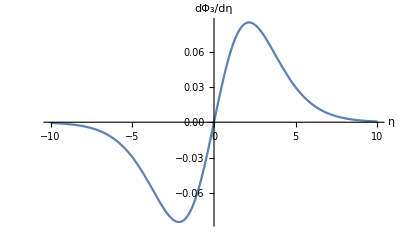

```mathematica
Clear[eq18pt115a]
eq18pt115a =
Plot[Evaluate[Simplify[Expand[D[eq18pt114[[1]][[2]],η]]]],{ η,-10,10},AxesLabel->{η ,Subscript[dΦ, 3]/dη}]
```

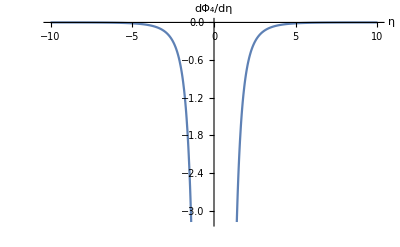

```mathematica
Clear[eq18pt115b]
eq18pt115b =
Plot[Evaluate[Simplify[Expand[D[eq18pt114[[2]][[2]],η]]]],{ η,-10,10},AxesLabel->{η ,Subscript[dΦ, 4]/dη}]
```

```mathematica
(* Since we have equations implicity defined we can't solve them explicitly for t if we have functions like R[t,r].  So we temporarily get rid of the function arguments , solve for t, then backsubtitute the arguments *) 
Clear[remtReplace]
remtReplace = { 
R[t,r] -> R  , 
M[r]-> M , 
ℰ[r]-> ℰ , 
tb[r]-> tb , 
η[t,r]-> η , 
R-> R[t,r] , 
M-> M[r] , 
ℰ-> ℰ[r] , 
tb-> tb[r] , 
η-> η[t,r]
} ;
remtReplace [[1;;5]] // TableForm
remtReplace [[6;;10]] // TableForm
```

R[t,r]→R
M[r]→M
ℰ[r]→ℰ
tb[r]→tb
η[t,r]→η

R→R[t,r]
M→M[r]
ℰ→ℰ[r]
tb→tb[r]
η→η[t,r]

```mathematica
eq18pt21 /. remtReplace [[1;;5]]
```

{R==(M (-1+Cosh[η]))/(2 ℰ),-η+Sinh[η]==(2 √2 (t-tb) ℰ^(3/2))/M}

```mathematica
Expand[Flatten[Solve[Eliminate[(eq18pt21 /. remtReplace [[1;;5]] ),η][[1]][[1]],tb]]]
Expand[Flatten[Solve[Eliminate[(eq18pt21 /. remtReplace [[1;;5]] ),η][[2]][[1]],tb]]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{tb→t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2)),tb→t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2))}

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{tb→t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2)),tb→t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2))}

```mathematica
(* Our second term RHS just looks different than theirs... *) 
Clear[eq18pt42a]
eq18pt42a = 
Expand[Flatten[Solve[Eliminate[(eq18pt21 /. remtReplace [[1;;5]] ),η][[1]][[1]],tb]]][[1]] /. Rule-> Equal
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

tb==t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2))

```mathematica
(* Our second term RHS just looks different than theirs... *) 
eq18pt42a[[2]][[2]]
```

-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)

```mathematica
(* To see that it's equivalent... *) 
(-M/(2 ℰ)^(3/2))√((1+(2 ℰ R)/M)^2-1) == eq18pt42a[[2]][[2]]
ApplySides[#^2&, (-M/(2 ℰ)^(3/2))√((1+(2 ℰ R)/M)^2-1) == eq18pt42a[[2]][[2]]] // Expand // Simplify
```

-(M √(-1+(1+(2 R ℰ)/M)^2))/(2 √2 ℰ^(3/2))==-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)

True

```mathematica
Clear[eq18pt42]
eq18pt42 = 
Collect[  ( eq18pt42a /. ( eq18pt42a[[2]][[2]]-> (-M/(2 ℰ)^(3/2))√((1+(2 ℰ R)/M)^2-1) ) )  ,-M/(2 √2 ℰ^(3/2))]
```

tb==t-(M (√(-1+(1+(2 R ℰ)/M)^2)+ArcCosh[1+(2 R ℰ)/M]))/(2 √2 ℰ^(3/2))

```mathematica
Eliminate[{( eq18pt42 /. t-> t2  /. R-> R2 ) ,( eq18pt42 /. t-> t1  /. R-> R1 ) },tb][[1]]
```

-(2 √2 t1 ℰ^(3/2))/M+(2 √2 t2 ℰ^(3/2))/M+2 √((R1 ℰ (M+R1 ℰ))/M^2)-2 √((R2 ℰ (M+R2 ℰ))/M^2)+ArcCosh[1+(2 R1 ℰ)/M]-ArcCosh[1+(2 R2 ℰ)/M]==0

```mathematica
(* Slight rearrangement gives what is in text *) 
Clear[eq18pt43]
eq18pt43 = 
SubtractSides[ ( eq18pt42 /. t-> t2  /. R-> R2 ) ,( eq18pt42 /. t-> t1  /. R-> R1 ) ]
```

0==-t1+t2+(M (√(-1+(1+(2 R1 ℰ)/M)^2)+ArcCosh[1+(2 R1 ℰ)/M]))/(2 √2 ℰ^(3/2))-(M (√(-1+(1+(2 R2 ℰ)/M)^2)+ArcCosh[1+(2 R2 ℰ)/M]))/(2 √2 ℰ^(3/2))

```mathematica
Clear[eq18pt44a]
eq18pt44a = { 
x == (2 ℰ)/M^(2/3) , 
a1 == R1/M^(1/3) , 
a2 == R2/M^(1/3) 

} ;
eq18pt44a // TableForm
```

x==(2 ℰ)/M^(2/3)
a1==R1/M^(1/3)
a2==R2/M^(1/3)

```mathematica
Clear[erReplace]
erReplace = 
Flatten[Solve[eq18pt44a,{ℰ,R1,R2}]] ;
erReplace  // TableForm
```

ℰ→1/2 M^(2/3) x
R1→a1 M^(1/3)
R2→a2 M^(1/3)

```mathematica
Clear[eq18pt44]
eq18pt44 = 
Subscript[ψ, H][x] == Collect[ ( (-x^(3/2))*eq18pt43[[2]]  /. erReplace  // PowerExpand  // Expand  ) , x^(3/2) ]
```

ψ_H[x]==(t1-t2) x^(3/2)-√(-1+(1+a1 x)^2)+√(-1+(1+a2 x)^2)-ArcCosh[1+a1 x]+ArcCosh[1+a2 x]

```mathematica
Clear[eq18pt44a]
eq18pt44a = { 
x == (-2 ℰ )/M^(2/3) , 
a1 == R1/M^(1/3) , 
a2 == R2/M^(1/3) 

} ;
eq18pt44a // TableForm
```

x==-(2 ℰ)/M^(2/3)
a1==R1/M^(1/3)
a2==R2/M^(1/3)

```mathematica
Clear[erReplaceEnegative]
erReplaceEnegative =
Flatten[Solve[eq18pt44a ,{ℰ,R1,R2}]] ;
erReplaceEnegative  // TableForm
```

ℰ→-1/2 M^(2/3) x
R1→a1 M^(1/3)
R2→a2 M^(1/3)

```mathematica
Expand[Flatten[Solve[Eliminate[(eq18pt19 /. remtReplace [[1;;5]] ),η][[1]][[1]],tb]]]
Expand[Flatten[Solve[Eliminate[(eq18pt19 /. remtReplace [[1;;5]] ),η][[2]][[1]],tb]]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{tb→t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2),tb→t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2)}

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{tb→t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2),tb→t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2)}

```mathematica
(* Our second term RHS just looks different than theirs... *) 
Clear[eq18pt46b]
eq18pt46b =
Expand[Flatten[Solve[Eliminate[(eq18pt19 /. remtReplace [[1;;5]] ),η][[1]][[1]],tb]]][[2]] /. Rule-> Equal
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

tb==t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2)

```mathematica
Clear[eq18pt46c]
eq18pt46c =
SubtractSides[ ( eq18pt46b  /. t-> t1 /. R-> R1  ),( eq18pt46b  /. t-> t2 /. R-> R2  ) ]
```

0==t1-t2+(M^2 √((8 R1 ℰ^4)/M^3+(8 R1^2 ℰ^5)/M^4))/(4 ℰ^3)-(M^2 √((8 R2 ℰ^4)/M^3+(8 R2^2 ℰ^5)/M^4))/(4 ℰ^3)+(M √-ℰ ArcCos[1+(2 R1 ℰ)/M])/(2 √2 ℰ^2)-(M √-ℰ ArcCos[1+(2 R2 ℰ)/M])/(2 √2 ℰ^2)

```mathematica
Clear[eq18pt46d]
eq18pt46d =
eq18pt46c /. erReplaceEnegative // PowerExpand
```

0==t1-t2-(2 √((a1 x^4)/2-(a1^2 x^5)/4))/x^3+(2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3+ArcCos[1-a1 x]/x^(3/2)-ArcCos[1-a2 x]/x^(3/2)

```mathematica
(* Our terms just look different... *)
```

```mathematica
(2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3== (√(1 - (1 - a2 x)^2))/x^(3/2)
ApplySides[#^2&,(2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3== (√(1 - (1 - a2 x)^2))/x^(3/2)] // Expand // Simplify
```

(2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3==(√(1-(1-a2 x)^2))/x^(3/2)

True

```mathematica
Clear[eq18pt46e]
eq18pt46e =
eq18pt46d  /. ((-1)*(2 √((a1 x^4)/2-(a1^2 x^5)/4))/x^3-> (-1)* (√(1 - (1 - a1 x)^2))/x^(3/2)) /.  ((2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3->  (√(1 - (1 - a2 x)^2))/x^(3/2))
```

0==t1-t2-(√(1-(1-a1 x)^2))/x^(3/2)+(√(1-(1-a2 x)^2))/x^(3/2)+ArcCos[1-a1 x]/x^(3/2)-ArcCos[1-a2 x]/x^(3/2)

```mathematica
(* Off by a few signs in places.... *) 
Clear[eq18pt46f]
eq18pt46f = 
Collect[ Expand[x^(3/2)*eq18pt46e[[2]]],x^(3/2)]
```

(t1-t2) x^(3/2)-√(1-(1-a1 x)^2)+√(1-(1-a2 x)^2)+ArcCos[1-a1 x]-ArcCos[1-a2 x]

```mathematica
(* Just typed in... go back and redo this derivaiton... *) 
Clear[eq18pt46]
eq18pt46 = 
Subscript[ψ, X][x] == ArcCos[1-a2 x]-√(1-(1-a2 x)^2) - ArcCos[1-a1 x] + √(1-(1-a1 x)^2) - (t2-t1) x^(3/2)
```

ψ_X[x]==-((-t1+t2) x^(3/2))+√(1-(1-a1 x)^2)-√(1-(1-a2 x)^2)-ArcCos[1-a1 x]+ArcCos[1-a2 x]

```mathematica
(* Just typed in... go back and redo this derivaiton... *) 
Clear[eq18pt49]
eq18pt49 = 
π +  ArcCos[-1+a2 x] + √(1-(1-a2 x)^2) - ArcCos[1-a1 x] + √(1-(1-a1 x)^2) - (t2-t1) x^(3/2)
```

π-(-t1+t2) x^(3/2)+√(1-(1-a1 x)^2)+√(1-(1-a2 x)^2)-ArcCos[1-a1 x]+ArcCos[-1+a2 x]

```mathematica
D[(Flatten[Solve[eq18pt15, ϵ[t,r]]][[1]] /. Rule-> Equal  ),r] // pdConv
Flatten[Solve[eq18pt15, ϵ[t,r]]][[1]] /. Rule-> Equal  // pdConv

Clear[eq18pt169]
eq18pt169= 
DivideSides[ D[(Flatten[Solve[eq18pt15, ϵ[t,r]]][[1]] /. Rule-> Equal  ),r],Flatten[Solve[eq18pt15, ϵ[t,r]]][[1]] /. Rule-> Equal][[1]][[1]][[1]] // Expand  ;
eq18pt169 // pdConv
```

(∂ϵ(t,r))/(∂r)==-(c^4 (∂M(r))/(∂r) (∂^2 R(t,r))/(∂r^2))/(4 π G (R(t,r))^2 ((∂R(t,r))/(∂r))^2)+(c^4 (∂^2 M(r))/(∂r^2))/(4 π G (R(t,r))^2 (∂R(t,r))/(∂r))-(c^4 (∂M(r))/(∂r))/(2 π G (R(t,r))^3)

ϵ(t,r)==(c^4 (∂M(r))/(∂r))/(4 π G (R(t,r))^2 (∂R(t,r))/(∂r))

((∂ϵ(t,r))/(∂r))/(ϵ(t,r))==-((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-(2 (∂R(t,r))/(∂r))/(R(t,r))+((∂^2 M(r))/(∂r^2))/((∂M(r))/(∂r))

```mathematica
(* This is our derivation... *) 
Clear[eq18pt170]
eq18pt170 = 
TensorValues[tensorList18pt16d3[[4]]] ;
eq18pt170  // pdConv
```

(4 (-((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))-ℰ(r)))/(R(t,r))^2

```mathematica
(* This is typed in directly ... *) 
Clear[eq18pt170a]
eq18pt170a = 
((-4)*Inactivate[D[R[t,r]ℰ[r],r],D])/(R[t,r]^2 D[R[t,r],r])  ;
eq18pt170a  // pdConv
```

-(4 (∂(R(t,r) ℰ(r)))/(∂r))/((R(t,r))^2 (∂R(t,r))/(∂r))

```mathematica
(* The two forms are equivalent... *) 
eq18pt170 == Activate[eq18pt170a] // Expand // Simplify
```

True

```mathematica
Clear[eq18pt171]
eq18pt171 = 
D[eq18pt170,r]/eq18pt170 // Expand // Simplify  // Expand  ;
eq18pt171  // pdConv
```

((∂^2 ℰ(r))/(∂r^2) R(t,r))/((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r))-((∂ℰ(r))/(∂r) R(t,r) (∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r)))-(2 ℰ(r) ((∂R(t,r))/(∂r))^2)/(R(t,r) ((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r)))

```mathematica
(* This is just typed in directly... *) 
Clear[eq18pt171a]
eq18pt171a = 
D[R[t,r]ℰ[r],{r,2}]/D[R[t,r]ℰ[r],r] - 2(D[R[t,r],r]/R[t,r]) - D[R[t,r],{r,2}]/D[R[t,r],r] ;
eq18pt171a // pdConv
```

((∂^2 ℰ(r))/(∂r^2) R(t,r)+ℰ(r) (∂^2 R(t,r))/(∂r^2)+2 (∂ℰ(r))/(∂r) (∂R(t,r))/(∂r))/((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r))-((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-(2 (∂R(t,r))/(∂r))/(R(t,r))

```mathematica
(* We see that the two forms are equivalent... *) 
eq18pt171  == eq18pt171a  // Expand // Simplify
```

True